```mathematica
?ScalarMixedSpins
```

package for scalar and mixed ...
Designations(7): d t it p pp collectPP pTimes
Symbolic(8): expandSigma expandSigTimes HBasis basisH coordinates matrixTransform fullCoordinates(...) fullTransform(...) 
Traces(4): fastTr1 fastTr gramMatrix symGramMatrix
RhoGen(16): lastKP firstKP nextKP listKPs compoze swapToPerm generateGroup normolizeKP KPToExpr invariantKPsets KPsetsToExpr rhoGen invariantKPTsets listKPTs allKPs depsGen
Linerear algebra(8): RowReduceUpTo RowReduceUpToShow RowReduceInfo LinDeps ApplyLinDeps LinDependent LinIndependent DeleteReduced
ExplicitMatrices(13): getSi getSz getSp getSm getSx getSy KP scalar scalarSparse mixed mixedSparse explicit explicitSparse
Utilities(5):  FE foundQ firstFound printTo plusToList

```mathematica
?ScalarMixedSpins`*
```

LinDeps[m] - RowReduceInfo[m][[2]] и показывает преобразования только для нулевых строк RowReduce[m]

```mathematica
doubleKrestGens={swapToPerm[{1->2},8],swapToPerm[{2->3},8],swapToPerm[{1->6,2->7,3->8,4->5},8]}
```

{{1→2,2→1,3→3,4→4,5→5,6→6,7→7,8→8},{1→1,2→3,3→2,4→4,5→5,6→6,7→7,8→8},{1→6,2→7,3→8,4→5,5→4,6→1,7→2,8→3}}

```mathematica
doubleKrestGroup=generateGroup[doubleKrestGens];
```

```mathematica
(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,doubleKrestGroup]
```

{d[1,2]+d[1,3]+d[2,3]+d[6,7]+d[6,8]+d[7,8],d[1,4]+d[2,4]+d[3,4]+d[5,6]+d[5,7]+d[5,8],d[1,5]+d[2,5]+d[3,5]+d[4,6]+d[4,7]+d[4,8],d[1,6]+d[1,7]+d[1,8]+d[2,6]+d[2,7]+d[2,8]+d[3,6]+d[3,7]+d[3,8],d[4,5]}

```mathematica
basis81={1};
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[4,8,doubleKrestGroup]];
basis81=basis81//Flatten;
```

```mathematica
H81=basis81[[3]]+basis81[[6]]
```

d[1,4]+d[2,4]+d[3,4]+d[4,5]+d[5,6]+d[5,7]+d[5,8]

```mathematica
Timing[vectors81=Hbasis[H81,basis81]][[1]]
```

16.3645

```mathematica
Timing[basis81GM=symGramMatrix[basis81]][[1]]
```

131.82084

```mathematica
Length[basis81]-MatrixRank[basis81GM]
```

0

```mathematica
Timing[{matrix81,rems81}=matrixTransform[vectors81,basis81]][[1]]
```

46.7223

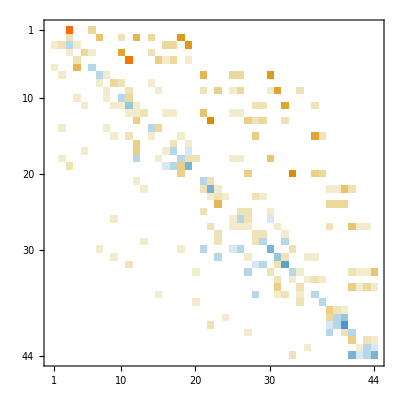

```mathematica
matrix81//MatrixPlot
```

```mathematica
Timing[{deps81,forbasis81}=RemBasis[rems81]][[1]]
```

10.70167

#### cycle

```mathematica
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{3},{6},{7}}

```mathematica
b=3;
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[b]]}];AppendTo[forbasis81,rems81[[b]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row[[1]]];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{7}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[7]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{4},{5},{8},{14},{18},{19},{33},{35},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[4]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{8},{14},{15},{18},{33},{35},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[8]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{9},{14},{15},{18},{30},{33},{34},{35},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[9]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{14},{18},{33},{34},{35},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[14]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{33},{34},{35},{37},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[33]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{34},{35},{44}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[34]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{10},{16},{17},{24},{38},{42},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[10]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{11},{16},{17},{24},{36},{38},{42},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[11]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{16},{24},{26},{36},{38},{42},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[16]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{24},{25},{26},{36},{38},{42},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[24]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{25},{26},{36},{38},{39},{42},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[25]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{26},{36},{38},{39},{43}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[26]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{31},{36},{38},{39}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[31]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{38},{39}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[38]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{12},{13},{21},{23},{27},{28},{29},{32},{40},{41}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[12]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{21},{22},{23},{28},{40},{41}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[21]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{23},{28}}

```mathematica
{deps81row,rems81tmp}=matrixTransform[rems81,{rems81[[23]]}];
AppendTo[forbasis81,rems81[[3]]];
rems81=rems81tmp;
AppendTo[deps81,deps81row];
list=(If[#===0,+Infinity,#//plusToList//Length]&)/@rems81;
Position[list,Min[list]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44}}

#### end cycle

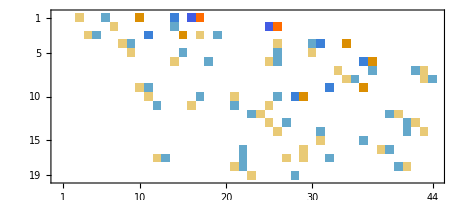

```mathematica
deps81//MatrixPlot
```

```mathematica
Timing[forbasis81GM=symGramMatrix[forbasis81/.it[a_,b_,c_]:>ⅈ t[a,b,c]]][[1]]
```

94.61461

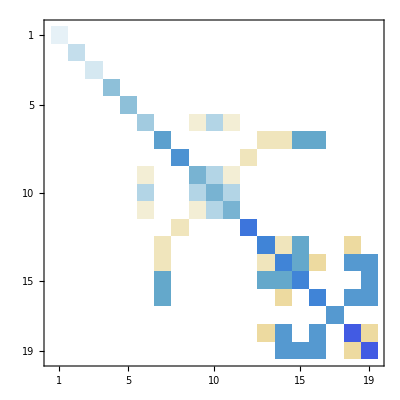

```mathematica
forbasis81GM//MatrixPlot
```

```mathematica
Length[forbasis81]
```

19

```mathematica
MatrixRank[forbasis81GM]
```

16

```mathematica
(depsdeps=LinDeps[forbasis81GM])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | 1 | 1)

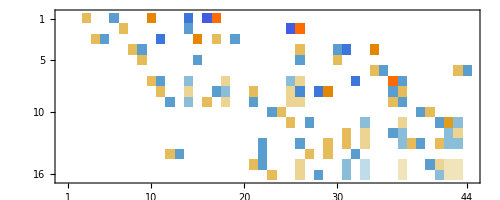

```mathematica
(realdeps=ApplyLinDeps[deps81,depsdeps][[1]])//MatrixPlot
```

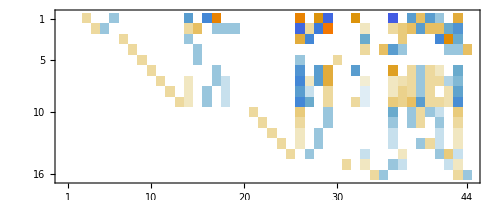

```mathematica
RowReduce[realdeps]//MatrixPlot
```

```mathematica
LinIndependent[RowReduce[realdeps]]
```

{1,2,5,6,14,15,16,17,18,19,20,26,27,28,29,30,32,33,35,36,37,38,39,40,41,42,43,44}

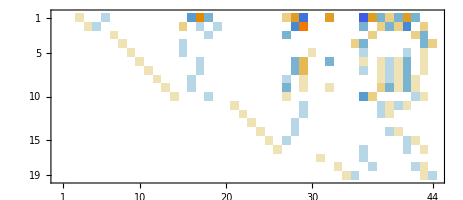

```mathematica
RowReduce[deps81]//MatrixPlot
```

```mathematica
LinIndependent[RowReduce[deps81]]
```

{1,2,5,6,15,16,17,18,19,20,27,28,29,30,32,35,36,37,38,39,40,41,42,43,44}

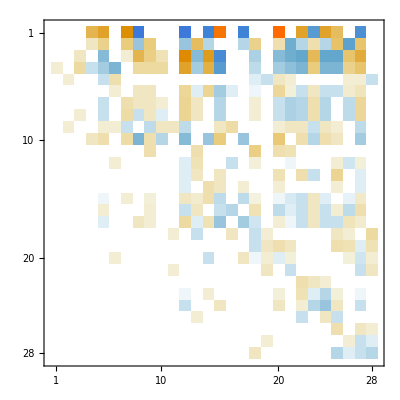

```mathematica
(realmatrix=Transpose[ApplyLinDeps[Transpose[matrix81],realdeps][[1]]][[LinIndependent[RowReduce[realdeps]]]])//MatrixPlot
```

```mathematica
Eigenvalues[realmatrix]//N
```

{-10.9733,-10.746,-10.5631,-8.01668,7.,-6.4641,5.84136,-5.03777,5.,4.74597,4.6334+0.321437 ⅈ,4.6334-0.321437 ⅈ,-4.61824,-3.82843,3.27721,-3.11236,-3.,3.,-2.36136,1.82843,1.38782+0.204859 ⅈ,1.38782-0.204859 ⅈ,-1.36427,-1.,-1.,-0.556993+0.187447 ⅈ,-0.556993-0.187447 ⅈ,0.464102}

```mathematica
Eigenvalues[matrix81]//N
```

{-10.746,-10.526,-10.026,-8.38799,7.,-6.4641,-6.31507,6.2915,-6.03932,-5.946,5.63014,-5.17226,5.07863,5.,4.74597,-4.2915,4.02827,-3.82843,-3.504,-3.,-3.,-3.,3.,2.89199,-2.748,-2.72369,-2.60419,-2.51414,-2.19791,2.08613,1.82843,1.763,-1.55263,1.51298,-1.,-1.,-1.,-1.,-1.,1.,-0.571993,0.464102,-0.306005,0.143987}

## Double crest

```mathematica
doubleKrestGens={swapToPerm[{1->2},8],swapToPerm[{2->3},8],swapToPerm[{1->6,2->7,3->8,4->5},8]}
```

{{1→2,2→1,3→3,4→4,5→5,6→6,7→7,8→8},{1→1,2→3,3→2,4→4,5→5,6→6,7→7,8→8},{1→6,2→7,3→8,4→5,5→4,6→1,7→2,8→3}}

```mathematica
doubleKrestGroup=generateGroup[doubleKrestGens];
```

```mathematica
(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,doubleKrestGroup]
```

{d[1,2]+d[1,3]+d[2,3]+d[6,7]+d[6,8]+d[7,8],d[1,4]+d[2,4]+d[3,4]+d[5,6]+d[5,7]+d[5,8],d[1,5]+d[2,5]+d[3,5]+d[4,6]+d[4,7]+d[4,8],d[1,6]+d[1,7]+d[1,8]+d[2,6]+d[2,7]+d[2,8]+d[3,6]+d[3,7]+d[3,8],d[4,5]}

```mathematica
basis81={1};
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,8,doubleKrestGroup]];
AppendTo[basis81,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[4,8,doubleKrestGroup]];
basis81=basis81//Flatten;
```

```mathematica
H81=basis81[[3]]+basis81[[6]]
```

d[1,4]+d[2,4]+d[3,4]+d[4,5]+d[5,6]+d[5,7]+d[5,8]

```mathematica
vectors81=Hbasis[H81,basis81];
```

```mathematica
coordinates[vectors81[[7]],basis81]
```

{{0,5,0,0,0,0,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-d[2,3] it[1,4,5]-d[1,3] it[2,4,5]-d[1,2] it[3,4,5]+d[7,8] it[4,5,6]+d[6,8] it[4,5,7]+d[6,7] it[4,5,8]}

```mathematica
collectPP[vectors81[[7]]]
```

5 pp[d[1,2]]+5 pp[d[1,3]]+5 pp[d[2,3]]+5 pp[d[6,7]]+5 pp[d[6,8]]+5 pp[d[7,8]]-2 pp[d[1,2],d[3,4]]+pp[d[1,2],d[3,5]]+ⅈ pp[d[1,2],t[3,4,5]]-2 pp[d[1,3],d[2,4]]+pp[d[1,3],d[2,5]]+ⅈ pp[d[1,3],t[2,4,5]]-2 pp[d[1,4],d[2,3]]+pp[d[1,5],d[2,3]]+ⅈ pp[d[2,3],t[1,4,5]]+pp[d[4,6],d[7,8]]+pp[d[4,7],d[6,8]]+pp[d[4,8],d[6,7]]-2 pp[d[5,6],d[7,8]]-2 pp[d[5,7],d[6,8]]-2 pp[d[5,8],d[6,7]]-ⅈ pp[d[6,7],t[4,5,8]]-ⅈ pp[d[6,8],t[4,5,7]]-ⅈ pp[d[7,8],t[4,5,6]]+pp[d[1,2],d[3,4],d[5,6]]+pp[d[1,2],d[3,4],d[5,7]]+pp[d[1,2],d[3,4],d[5,8]]+pp[d[1,3],d[2,4],d[5,6]]+pp[d[1,3],d[2,4],d[5,7]]+pp[d[1,3],d[2,4],d[5,8]]+pp[d[1,4],d[2,3],d[5,6]]+pp[d[1,4],d[2,3],d[5,7]]+pp[d[1,4],d[2,3],d[5,8]]+pp[d[1,4],d[5,6],d[7,8]]+pp[d[1,4],d[5,7],d[6,8]]+pp[d[1,4],d[5,8],d[6,7]]+pp[d[2,4],d[5,6],d[7,8]]+pp[d[2,4],d[5,7],d[6,8]]+pp[d[2,4],d[5,8],d[6,7]]+pp[d[3,4],d[5,6],d[7,8]]+pp[d[3,4],d[5,7],d[6,8]]+pp[d[3,4],d[5,8],d[6,7]]

```mathematica
Timing[{matrix81,excepts81}=matrixTransform[vectors81,basis81]]
```

3)

4)

5)

6)

7)

8)

9)

10)

11)

12)

13)

14)

15)

16)

17)

18)

19)

21)

22)

23)

24)

25)

26)

27)

28)

29)

30)

31)

32)

33)

34)

35)

36)

37)

38)

39)

40)

41)

42)

43)

44)

{49.99832,{{{0,0,18,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,5,0,0,2,0,6,0,3,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},41,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,-4,-1,-2,-4}},{0,0,40,1,1}}}
 |  |  |  |

```mathematica
MatrixPlot[matrix81]
```

-Graphics-

```mathematica
matrix81//TableForm
```

0 | 0 | 18 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 6 | 0 | 3 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 4 | 1 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 6 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 0 | 1 | 3 | 0 | 0 | 0 | 1 | 8 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | -3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 8 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 4 | 2 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 1 | -2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 1 | 0 | 0 | -2 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | 4 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 4 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 5 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 5 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | -2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -2 | 0 | 0 | 0 | -1 | -2 | 0 | 0 | 0 | -4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -3 | 2 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | 0 | 2 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 2 | 0 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 1 | 3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | -2 | -3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | -8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 2 | -2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -1 | -2 | -4

```mathematica
SparseArray[matrix81]
```

SparseArray[<237>, {44, 44}]

```mathematica
Timing[Union[Eigenvalues[explicit[1/2,8,H81]]]]
```

{7.17605,{-3,-1,3,5,7,-1-2 √2,-1+2 √2,-3-2 √3,-3+2 √3,1-2 √7,1+2 √7,-3-2 √15,-3+2 √15,Root[3-21 #1+#1^2+#1^3&,1],Root[3-21 #1+#1^2+#1^3&,2],Root[3-21 #1+#1^2+#1^3&,3],Root[-147-45 #1+7 #1^2+#1^3&,1],Root[-147-45 #1+7 #1^2+#1^3&,2],Root[-147-45 #1+7 #1^2+#1^3&,3],Root[-83-45 #1+7 #1^2+#1^3&,1],Root[-83-45 #1+7 #1^2+#1^3&,2],Root[-83-45 #1+7 #1^2+#1^3&,3],Root[-85-5 #1+9 #1^2+#1^3&,1],Root[-85-5 #1+9 #1^2+#1^3&,2],Root[-85-5 #1+9 #1^2+#1^3&,3]}}

```mathematica
SortBy[{-3,-1,3,5,7,-1-2 √2,-1+2 √2,-3-2 √3,-3+2 √3,1-2 √7,1+2 √7,-3-2 √15,-3+2 √15,Root[3-21 #1+#1^2+#1^3&,1],Root[3-21 #1+#1^2+#1^3&,2],Root[3-21 #1+#1^2+#1^3&,3],Root[-147-45 #1+7 #1^2+#1^3&,1],Root[-147-45 #1+7 #1^2+#1^3&,2],Root[-147-45 #1+7 #1^2+#1^3&,3],Root[-83-45 #1+7 #1^2+#1^3&,1],Root[-83-45 #1+7 #1^2+#1^3&,2],Root[-83-45 #1+7 #1^2+#1^3&,3],Root[-85-5 #1+9 #1^2+#1^3&,1],Root[-85-5 #1+9 #1^2+#1^3&,2],Root[-85-5 #1+9 #1^2+#1^3&,3]},N]
```

{-3-2 √15,Root[-83-45 #1+7 #1^2+#1^3&,1],Root[-147-45 #1+7 #1^2+#1^3&,1],Root[-85-5 #1+9 #1^2+#1^3&,1],-3-2 √3,Root[3-21 #1+#1^2+#1^3&,1],1-2 √7,-1-2 √2,Root[-85-5 #1+9 #1^2+#1^3&,2],-3,Root[-147-45 #1+7 #1^2+#1^3&,2],Root[-83-45 #1+7 #1^2+#1^3&,2],-1,Root[3-21 #1+#1^2+#1^3&,2],-3+2 √3,-1+2 √2,Root[-85-5 #1+9 #1^2+#1^3&,3],3,Root[3-21 #1+#1^2+#1^3&,3],-3+2 √15,5,Root[-83-45 #1+7 #1^2+#1^3&,3],Root[-147-45 #1+7 #1^2+#1^3&,3],1+2 √7,7}

```mathematica
%//Length
```

25

```mathematica
forbasis81={1,(*1*)it[1,4,5]+it[2,4,5]+it[3,4,5]-it[4,5,6]-it[4,5,7]-it[4,5,8],(*2*)d[2,3] it[1,4,5]+d[1,3] it[2,4,5]+d[1,2] it[3,4,5]-d[7,8] it[4,5,6]-d[6,8] it[4,5,7]-d[6,7] it[4,5,8],(*3*)it[1,4,6]+it[1,4,7]+it[1,4,8]-it[1,5,6]-it[1,5,7]-it[1,5,8]+it[2,4,6]+it[2,4,7]+it[2,4,8]-it[2,5,6]-it[2,5,7]-it[2,5,8]+it[3,4,6]+it[3,4,7]+it[3,4,8]-it[3,5,6]-it[3,5,7]-it[3,5,8],(*4*)-d[7,8] it[1,4,6]-d[6,8] it[1,4,7]-d[6,7] it[1,4,8]+d[2,3] t[1,5,6]+d[2,3] t[1,5,7]+d[2,3] t[1,5,8]-d[7,8] t[2,4,6]-d[6,8] t[2,4,7]-d[6,7] t[2,4,8]+d[1,3] t[2,5,6]+d[1,3] t[2,5,7]+d[1,3] it[2,5,8]-d[7,8] it[3,4,6]-d[6,8] it[3,4,7]-d[6,7] it[3,4,8]+d[1,2] it[3,5,6]+d[1,2] it[3,5,7]+d[1,2] it[3,5,8],(*5*)d[2,3] it[1,4,6]+d[2,3] it[1,4,7]+d[2,3] it[1,4,8]-d[7,8] it[1,5,6]-d[6,8] it[1,5,7]-d[6,7] it[1,5,8]+d[1,3] it[2,4,6]+d[1,3] it[2,4,7]+d[1,3] it[2,4,8]-d[7,8] it[2,5,6]-d[6,8] it[2,5,7]-d[6,7] it[2,5,8]+d[1,2] it[3,4,6]+d[1,2] it[3,4,7]+d[1,2] it[3,4,8]-d[7,8] it[3,5,6]-d[6,8] it[3,5,7]-d[6,7] it[3,5,8],(*6*)d[2,3] d[7,8] it[1,4,6]+d[2,3] d[6,8] it[1,4,7]+d[2,3] d[6,7] it[1,4,8]-d[2,3] d[7,8] it[1,5,6]-d[2,3] d[6,8] it[1,5,7]-d[2,3] d[6,7] it[1,5,8]+d[1,3] d[7,8] it[2,4,6]+d[1,3] d[6,8] it[2,4,7]+d[1,3] d[6,7] it[2,4,8]-d[1,3] d[7,8] it[2,5,6]-d[1,3] d[6,8] it[2,5,7]-d[1,3] d[6,7] it[2,5,8]+d[1,2] d[7,8] it[3,4,6]+d[1,2] d[6,8] it[3,4,7]+d[1,2] d[6,7] it[3,4,8]-d[1,2] d[7,8] it[3,5,6]-d[1,2] d[6,8] it[3,5,7]-d[1,2] d[6,7] it[3,5,8],(*7*)d[6,7] it[1,4,5]+d[6,8] it[1,4,5]+d[7,8] it[1,4,5]+d[6,7] it[2,4,5]+d[6,8] it[2,4,5]+d[7,8] it[2,4,5]+d[6,7] it[3,4,5]+d[6,8] it[3,4,5]+d[7,8] it[3,4,5]-d[1,2] it[4,5,6]-d[1,3] it[4,5,6]-d[2,3] it[4,5,6]-d[1,2] it[4,5,7]-d[1,3] it[4,5,7]-d[2,3] it[4,5,7]-d[1,2] it[4,5,8]-d[1,3] it[4,5,8]-d[2,3] it[4,5,8],(*8*)d[2,3] d[6,7] it[1,4,5]+d[2,3] d[6,8] it[1,4,5]+d[2,3] d[7,8] it[1,4,5]+d[1,3] d[6,7] it[2,4,5]+d[1,3] d[6,8] it[2,4,5]+d[1,3] d[7,8] it[2,4,5]+d[1,2] d[6,7] it[3,4,5]+d[1,2] d[6,8] it[3,4,5]+d[1,2] d[7,8] it[3,4,5]-d[1,2] d[7,8] it[4,5,6]-d[1,3] d[7,8] it[4,5,6]-d[2,3] d[7,8] it[4,5,6]-d[1,2] d[6,8] it[4,5,7]-d[1,3] d[6,8] it[4,5,7]-d[2,3] d[6,8] it[4,5,7]-d[1,2] d[6,7] it[4,5,8]-d[1,3] d[6,7] it[4,5,8]-d[2,3] d[6,7] it[4,5,8],(*9*)-d[5,7] it[1,4,6]-d[5,8] it[1,4,6]-d[5,6] it[1,4,7]-d[5,8] it[1,4,7]-d[5,6] it[1,4,8]-d[5,7] it[1,4,8]+d[2,4] it[1,5,6]+d[3,4] it[1,5,6]+d[2,4] it[1,5,7]+d[3,4] it[1,5,7]+d[2,4] it[1,5,8]+d[3,4] it[1,5,8]-d[5,7] it[2,4,6]-d[5,8] it[2,4,6]-d[5,6] it[2,4,7]-d[5,8] it[2,4,7]-d[5,6] it[2,4,8]-d[5,7] it[2,4,8]+d[1,4] it[2,5,6]+d[3,4] it[2,5,6]+d[1,4] it[2,5,7]+d[3,4] it[2,5,7]+d[1,4] it[2,5,8]+d[3,4] it[2,5,8]-d[5,7] it[3,4,6]-d[5,8] it[3,4,6]-d[5,6] it[3,4,7]-d[5,8] it[3,4,7]-d[5,6] it[3,4,8]-d[5,7] it[3,4,8]+d[1,4] it[3,5,6]+d[2,4] it[3,5,6]+d[1,4] it[3,5,7]+d[2,4] it[3,5,7]+d[1,4] it[3,5,8]+d[2,4] it[3,5,8],(*10*)d[2,8] d[3,7] it[1,4,6]+d[2,7] d[3,8] it[1,4,6]+d[2,8] d[3,6] it[1,4,7]+d[2,6] d[3,8] it[1,4,7]+d[2,7] d[3,6] it[1,4,8]+d[2,6] d[3,7] it[1,4,8]-d[2,8] d[3,7] it[1,5,6]-d[2,7] d[3,8] it[1,5,6]-d[2,8] d[3,6] it[1,5,7]-d[2,6] d[3,8] it[1,5,7]-d[2,7] d[3,6] it[1,5,8]-d[2,6] d[3,7] it[1,5,8]+d[1,8] d[3,7] it[2,4,6]+d[1,7] d[3,8] it[2,4,6]+d[1,8] d[3,6] it[2,4,7]+d[1,6] d[3,8] it[2,4,7]+d[1,7] d[3,6] it[2,4,8]+d[1,6] d[3,7] it[2,4,8]-d[1,8] d[3,7] it[2,5,6]-d[1,7] d[3,8] it[2,5,6]-d[1,8] d[3,6] it[2,5,7]-d[1,6] d[3,8] it[2,5,7]-d[1,7] d[3,6] it[2,5,8]-d[1,6] d[3,7] it[2,5,8]+d[1,8] d[2,7] it[3,4,6]+d[1,7] d[2,8] it[3,4,6]+d[1,8] d[2,6] it[3,4,7]+d[1,6] d[2,8] it[3,4,7]+d[1,7] d[2,6] it[3,4,8]+d[1,6] d[2,7] it[3,4,8]-d[1,8] d[2,7] it[3,5,6]-d[1,7] d[2,8] it[3,5,6]-d[1,8] d[2,6] it[3,5,7]-d[1,6] d[2,8] it[3,5,7]-d[1,7] d[2,6] it[3,5,8]-d[1,6] d[2,7] it[3,5,8],(*11*)-d[2,5] it[1,4,6]-d[3,5] it[1,4,6]-d[2,5] it[1,4,7]-d[3,5] it[1,4,7]-d[2,5] it[1,4,8]-d[3,5] it[1,4,8]+d[4,7] it[1,5,6]+d[4,8] it[1,5,6]+d[4,6] it[1,5,7]+d[4,8] it[1,5,7]+d[4,6] it[1,5,8]+d[4,7] it[1,5,8]-d[1,5] it[2,4,6]-d[3,5] it[2,4,6]-d[1,5] it[2,4,7]-d[3,5] it[2,4,7]-d[1,5] it[2,4,8]-d[3,5] it[2,4,8]+d[4,7] it[2,5,6]+d[4,8] it[2,5,6]+d[4,6] it[2,5,7]+d[4,8] it[2,5,7]+d[4,6] it[2,5,8]+d[4,7] it[2,5,8]-d[1,5] it[3,4,6]-d[2,5] it[3,4,6]-d[1,5] it[3,4,7]-d[2,5] it[3,4,7]-d[1,5] it[3,4,8]-d[2,5] it[3,4,8]+d[4,7] it[3,5,6]+d[4,8] it[3,5,6]+d[4,6] it[3,5,7]+d[4,8] it[3,5,7]+d[4,6] it[3,5,8]+d[4,7] it[3,5,8],(*12*)-d[2,5] d[7,8] it[1,4,6]-d[3,5] d[7,8] it[1,4,6]-d[2,5] d[6,8] it[1,4,7]-d[3,5] d[6,8] it[1,4,7]-d[2,5] d[6,7] it[1,4,8]-d[3,5] d[6,7] it[1,4,8]+d[2,3] d[4,7] it[1,5,6]+d[2,3] d[4,8] it[1,5,6]+d[2,3] d[4,6] it[1,5,7]+d[2,3] d[4,8] it[1,5,7]+d[2,3] d[4,6] it[1,5,8]+d[2,3] d[4,7] it[1,5,8]-d[1,5] d[7,8] it[2,4,6]-d[3,5] d[7,8] it[2,4,6]-d[1,5] d[6,8] it[2,4,7]-d[3,5] d[6,8] it[2,4,7]-d[1,5] d[6,7] it[2,4,8]-d[3,5] d[6,7] it[2,4,8]+d[1,3] d[4,7] it[2,5,6]+d[1,3] d[4,8] it[2,5,6]+d[1,3] d[4,6] it[2,5,7]+d[1,3] d[4,8] it[2,5,7]+d[1,3] d[4,6] it[2,5,8]+d[1,3] d[4,7] it[2,5,8]-d[1,5] d[7,8] it[3,4,6]-d[2,5] d[7,8] it[3,4,6]-d[1,5] d[6,8] it[3,4,7]-d[2,5] d[6,8] it[3,4,7]-d[1,5] d[6,7] it[3,4,8]-d[2,5] d[6,7] it[3,4,8]+d[1,2] d[4,7] it[3,5,6]+d[1,2] d[4,8] it[3,5,6]+d[1,2] d[4,6] it[3,5,7]+d[1,2] d[4,8] it[3,5,7]+d[1,2] d[4,6] it[3,5,8]+d[1,2] d[4,7] it[3,5,8],(*13*)-d[2,3] d[5,7] it[1,4,6]-d[2,3] d[5,8] it[1,4,6]-d[2,3] d[5,6] it[1,4,7]-d[2,3] d[5,8] it[1,4,7]-d[2,3] d[5,6] it[1,4,8]-d[2,3] d[5,7] it[1,4,8]+d[2,4] d[7,8] it[1,5,6]+d[3,4] d[7,8] it[1,5,6]+d[2,4] d[6,8] it[1,5,7]+d[3,4] d[6,8] it[1,5,7]+d[2,4] d[6,7] it[1,5,8]+d[3,4] d[6,7] it[1,5,8]-d[1,3] d[5,7] it[2,4,6]-d[1,3] d[5,8] it[2,4,6]-d[1,3] d[5,6] it[2,4,7]-d[1,3] d[5,8] it[2,4,7]-d[1,3] d[5,6] it[2,4,8]-d[1,3] d[5,7] it[2,4,8]+d[1,4] d[7,8] it[2,5,6]+d[3,4] d[7,8] it[2,5,6]+d[1,4] d[6,8] it[2,5,7]+d[3,4] d[6,8] it[2,5,7]+d[1,4] d[6,7] it[2,5,8]+d[3,4] d[6,7] it[2,5,8]-d[1,2] d[5,7] it[3,4,6]-d[1,2] d[5,8] it[3,4,6]-d[1,2] d[5,6] it[3,4,7]-d[1,2] d[5,8] it[3,4,7]-d[1,2] d[5,6] it[3,4,8]-d[1,2] d[5,7] it[3,4,8]+d[1,4] d[7,8] it[3,5,6]+d[2,4] d[7,8] it[3,5,6]+d[1,4] d[6,8] it[3,5,7]+d[2,4] d[6,8] it[3,5,7]+d[1,4] d[6,7] it[3,5,8]+d[2,4] d[6,7] it[3,5,8],(*14*)d[2,6] it[1,4,5]+d[2,7] it[1,4,5]+d[2,8] it[1,4,5]+d[3,6] it[1,4,5]+d[3,7] it[1,4,5]+d[3,8] it[1,4,5]+d[1,6] it[2,4,5]+d[1,7] it[2,4,5]+d[1,8] it[2,4,5]+d[3,6] it[2,4,5]+d[3,7] it[2,4,5]+d[3,8] it[2,4,5]+d[1,6] it[3,4,5]+d[1,7] it[3,4,5]+d[1,8] it[3,4,5]+d[2,6] it[3,4,5]+d[2,7] it[3,4,5]+d[2,8] it[3,4,5]-d[1,7] it[4,5,6]-d[1,8] it[4,5,6]-d[2,7] it[4,5,6]-d[2,8] it[4,5,6]-d[3,7] it[4,5,6]-d[3,8] it[4,5,6]-d[1,6] it[4,5,7]-d[1,8] it[4,5,7]-d[2,6] it[4,5,7]-d[2,8] it[4,5,7]-d[3,6] it[4,5,7]-d[3,8] it[4,5,7]-d[1,6] it[4,5,8]-d[1,7] it[4,5,8]-d[2,6] it[4,5,8]-d[2,7] it[4,5,8]-d[3,6] it[4,5,8]-d[3,7] it[4,5,8],(*15*)d[2,8] d[6,7] it[1,4,5]+d[3,8] d[6,7] it[1,4,5]+d[2,7] d[6,8] it[1,4,5]+d[3,7] d[6,8] it[1,4,5]+d[2,6] d[7,8] it[1,4,5]+d[3,6] d[7,8] it[1,4,5]+d[1,8] d[6,7] it[2,4,5]+d[3,8] d[6,7] it[2,4,5]+d[1,7] d[6,8] it[2,4,5]+d[3,7] d[6,8] it[2,4,5]+d[1,6] d[7,8] it[2,4,5]+d[3,6] d[7,8] it[2,4,5]+d[1,8] d[6,7] it[3,4,5]+d[2,8] d[6,7] it[3,4,5]+d[1,7] d[6,8] it[3,4,5]+d[2,7] d[6,8] it[3,4,5]+d[1,6] d[7,8] it[3,4,5]+d[2,6] d[7,8] it[3,4,5]-d[1,7] d[2,3] it[4,5,6]-d[1,8] d[2,3] it[4,5,6]-d[1,3] d[2,7] it[4,5,6]-d[1,3] d[2,8] it[4,5,6]-d[1,2] d[3,7] it[4,5,6]-d[1,2] d[3,8] it[4,5,6]-d[1,6] d[2,3] it[4,5,7]-d[1,8] d[2,3] it[4,5,7]-d[1,3] d[2,6] it[4,5,7]-d[1,3] d[2,8] it[4,5,7]-d[1,2] d[3,6] it[4,5,7]-d[1,2] d[3,8] it[4,5,7]-d[1,6] d[2,3] it[4,5,8]-d[1,7] d[2,3] it[4,5,8]-d[1,3] d[2,6] it[4,5,8]-d[1,3] d[2,7] it[4,5,8]-d[1,2] d[3,6] it[4,5,8]-d[1,2] d[3,7] it[4,5,8],(*16*)d[2,7] d[3,6] it[1,4,5]+d[2,8] d[3,6] it[1,4,5]+d[2,6] d[3,7] it[1,4,5]+d[2,8] d[3,7] it[1,4,5]+d[2,6] d[3,8] it[1,4,5]+d[2,7] d[3,8] it[1,4,5]+d[1,7] d[3,6] it[2,4,5]+d[1,8] d[3,6] it[2,4,5]+d[1,6] d[3,7] it[2,4,5]+d[1,8] d[3,7] it[2,4,5]+d[1,6] d[3,8] it[2,4,5]+d[1,7] d[3,8] it[2,4,5]+d[1,7] d[2,6] it[3,4,5]+d[1,8] d[2,6] it[3,4,5]+d[1,6] d[2,7] it[3,4,5]+d[1,8] d[2,7] it[3,4,5]+d[1,6] d[2,8] it[3,4,5]+d[1,7] d[2,8] it[3,4,5]-d[1,8] d[2,7] it[4,5,6]-d[1,7] d[2,8] it[4,5,6]-d[1,8] d[3,7] it[4,5,6]-d[2,8] d[3,7] it[4,5,6]-d[1,7] d[3,8] it[4,5,6]-d[2,7] d[3,8] it[4,5,6]-d[1,8] d[2,6] it[4,5,7]-d[1,6] d[2,8] it[4,5,7]-d[1,8] d[3,6] it[4,5,7]-d[2,8] d[3,6] it[4,5,7]-d[1,6] d[3,8] it[4,5,7]-d[2,6] d[3,8] it[4,5,7]-d[1,7] d[2,6] it[4,5,8]-d[1,6] d[2,7] it[4,5,8]-d[1,7] d[3,6] it[4,5,8]-d[2,7] d[3,6] it[4,5,8]-d[1,6] d[3,7] it[4,5,8]-d[2,6] d[3,7] it[4,5,8],(*17*)d[2,7] it[1,4,6]+d[2,8] it[1,4,6]+d[3,7] it[1,4,6]+d[3,8] it[1,4,6]+d[2,6] it[1,4,7]+d[2,8] it[1,4,7]+d[3,6] it[1,4,7]+d[3,8] it[1,4,7]+d[2,6] it[1,4,8]+d[2,7] it[1,4,8]+d[3,6] it[1,4,8]+d[3,7] it[1,4,8]-d[2,7] it[1,5,6]-d[2,8] it[1,5,6]-d[3,7] it[1,5,6]-d[3,8] it[1,5,6]-d[2,6] it[1,5,7]-d[2,8] it[1,5,7]-d[3,6] it[1,5,7]-d[3,8] it[1,5,7]-d[2,6] it[1,5,8]-d[2,7] it[1,5,8]-d[3,6] it[1,5,8]-d[3,7] it[1,5,8]+d[1,7] it[2,4,6]+d[1,8] it[2,4,6]+d[3,7] it[2,4,6]+d[3,8] it[2,4,6]+d[1,6] it[2,4,7]+d[1,8] it[2,4,7]+d[3,6] it[2,4,7]+d[3,8] it[2,4,7]+d[1,6] it[2,4,8]+d[1,7] it[2,4,8]+d[3,6] it[2,4,8]+d[3,7] it[2,4,8]-d[1,7] it[2,5,6]-d[1,8] it[2,5,6]-d[3,7] it[2,5,6]-d[3,8] it[2,5,6]-d[1,6] it[2,5,7]-d[1,8] it[2,5,7]-d[3,6] it[2,5,7]-d[3,8] it[2,5,7]-d[1,6] it[2,5,8]-d[1,7] it[2,5,8]-d[3,6] it[2,5,8]-d[3,7] it[2,5,8]+d[1,7] it[3,4,6]+d[1,8] it[3,4,6]+d[2,7] it[3,4,6]+d[2,8] it[3,4,6]+d[1,6] it[3,4,7]+d[1,8] it[3,4,7]+d[2,6] it[3,4,7]+d[2,8] it[3,4,7]+d[1,6] it[3,4,8]+d[1,7] it[3,4,8]+d[2,6] it[3,4,8]+d[2,7] it[3,4,8]-d[1,7] it[3,5,6]-d[1,8] it[3,5,6]-d[2,7] it[3,5,6]-d[2,8] it[3,5,6]-d[1,6] it[3,5,7]-d[1,8] it[3,5,7]-d[2,6] it[3,5,7]-d[2,8] it[3,5,7]-d[1,6] it[3,5,8]-d[1,7] it[3,5,8]-d[2,6] it[3,5,8]-d[2,7] it[3,5,8],(*18*)d[2,8] d[5,7] it[1,4,6]+d[3,8] d[5,7] it[1,4,6]+d[2,7] d[5,8] it[1,4,6]+d[3,7] d[5,8] it[1,4,6]+d[2,8] d[5,6] it[1,4,7]+d[3,8] d[5,6] it[1,4,7]+d[2,6] d[5,8] it[1,4,7]+d[3,6] d[5,8] it[1,4,7]+d[2,7] d[5,6] it[1,4,8]+d[3,7] d[5,6] it[1,4,8]+d[2,6] d[5,7] it[1,4,8]+d[3,6] d[5,7] it[1,4,8]-d[2,7] d[3,4] it[1,5,6]-d[2,8] d[3,4] it[1,5,6]-d[2,4] d[3,7] it[1,5,6]-d[2,4] d[3,8] it[1,5,6]-d[2,6] d[3,4] it[1,5,7]-d[2,8] d[3,4] it[1,5,7]-d[2,4] d[3,6] it[1,5,7]-d[2,4] d[3,8] it[1,5,7]-d[2,6] d[3,4] it[1,5,8]-d[2,7] d[3,4] it[1,5,8]-d[2,4] d[3,6] it[1,5,8]-d[2,4] d[3,7] it[1,5,8]+d[1,8] d[5,7] it[2,4,6]+d[3,8] d[5,7] it[2,4,6]+d[1,7] d[5,8] it[2,4,6]+d[3,7] d[5,8] it[2,4,6]+d[1,8] d[5,6] it[2,4,7]+d[3,8] d[5,6] it[2,4,7]+d[1,6] d[5,8] it[2,4,7]+d[3,6] d[5,8] it[2,4,7]+d[1,7] d[5,6] it[2,4,8]+d[3,7] d[5,6] it[2,4,8]+d[1,6] d[5,7] it[2,4,8]+d[3,6] d[5,7] it[2,4,8]-d[1,7] d[3,4] it[2,5,6]-d[1,8] d[3,4] it[2,5,6]-d[1,4] d[3,7] it[2,5,6]-d[1,4] d[3,8] it[2,5,6]-d[1,6] d[3,4] it[2,5,7]-d[1,8] d[3,4] it[2,5,7]-d[1,4] d[3,6] it[2,5,7]-d[1,4] d[3,8] it[2,5,7]-d[1,6] d[3,4] it[2,5,8]-d[1,7] d[3,4] it[2,5,8]-d[1,4] d[3,6] it[2,5,8]-d[1,4] d[3,7] it[2,5,8]+d[1,8] d[5,7] it[3,4,6]+d[2,8] d[5,7] it[3,4,6]+d[1,7] d[5,8] it[3,4,6]+d[2,7] d[5,8] it[3,4,6]+d[1,8] d[5,6] it[3,4,7]+d[2,8] d[5,6] it[3,4,7]+d[1,6] d[5,8] it[3,4,7]+d[2,6] d[5,8] it[3,4,7]+d[1,7] d[5,6] it[3,4,8]+d[2,7] d[5,6] it[3,4,8]+d[1,6] d[5,7] it[3,4,8]+d[2,6] d[5,7] it[3,4,8]-d[1,7] d[2,4] it[3,5,6]-d[1,8] d[2,4] it[3,5,6]-d[1,4] d[2,7] it[3,5,6]-d[1,4] d[2,8] it[3,5,6]-d[1,6] d[2,4] it[3,5,7]-d[1,8] d[2,4] it[3,5,7]-d[1,4] d[2,6] it[3,5,7]-d[1,4] d[2,8] it[3,5,7]-d[1,6] d[2,4] it[3,5,8]-d[1,7] d[2,4] it[3,5,8]-d[1,4] d[2,6] it[3,5,8]-d[1,4] d[2,7] it[3,5,8],d[2,7] d[3,5] it[1,4,6]+d[2,8] d[3,5] it[1,4,6]+d[2,5] d[3,7] it[1,4,6]+d[2,5] d[3,8] it[1,4,6]+d[2,6] d[3,5] it[1,4,7]+d[2,8] d[3,5] it[1,4,7]+d[2,5] d[3,6] it[1,4,7]+d[2,5] d[3,8] it[1,4,7]+d[2,6] d[3,5] it[1,4,8]+d[2,7] d[3,5] it[1,4,8]+d[2,5] d[3,6] it[1,4,8]+d[2,5] d[3,7] it[1,4,8]-d[2,8] d[4,7] it[1,5,6]-d[3,8] d[4,7] it[1,5,6]-d[2,7] d[4,8] it[1,5,6]-d[3,7] d[4,8] it[1,5,6]-d[2,8] d[4,6] it[1,5,7]-d[3,8] d[4,6] it[1,5,7]-d[2,6] d[4,8] it[1,5,7]-d[3,6] d[4,8] it[1,5,7]-d[2,7] d[4,6] it[1,5,8]-d[3,7] d[4,6] it[1,5,8]-d[2,6] d[4,7] it[1,5,8]-d[3,6] d[4,7] it[1,5,8]+d[1,7] d[3,5] it[2,4,6]+d[1,8] d[3,5] it[2,4,6]+d[1,5] d[3,7] it[2,4,6]+d[1,5] d[3,8] it[2,4,6]+d[1,6] d[3,5] it[2,4,7]+d[1,8] d[3,5] it[2,4,7]+d[1,5] d[3,6] it[2,4,7]+d[1,5] d[3,8] it[2,4,7]+d[1,6] d[3,5] it[2,4,8]+d[1,7] d[3,5] it[2,4,8]+d[1,5] d[3,6] it[2,4,8]+d[1,5] d[3,7] it[2,4,8]-d[1,8] d[4,7] it[2,5,6]-d[3,8] d[4,7] it[2,5,6]-d[1,7] d[4,8] it[2,5,6]-d[3,7] d[4,8] it[2,5,6]-d[1,8] d[4,6] it[2,5,7]-d[3,8] d[4,6] it[2,5,7]-d[1,6] d[4,8] it[2,5,7]-d[3,6] d[4,8] it[2,5,7]-d[1,7] d[4,6] it[2,5,8]-d[3,7] d[4,6] it[2,5,8]-d[1,6] d[4,7] it[2,5,8]-d[3,6] d[4,7] it[2,5,8]+d[1,7] d[2,5] it[3,4,6]+d[1,8] d[2,5] it[3,4,6]+d[1,5] d[2,7] it[3,4,6]+d[1,5] d[2,8] it[3,4,6]+d[1,6] d[2,5] it[3,4,7]+d[1,8] d[2,5] it[3,4,7]+d[1,5] d[2,6] it[3,4,7]+d[1,5] d[2,8] it[3,4,7]+d[1,6] d[2,5] it[3,4,8]+d[1,7] d[2,5] it[3,4,8]+d[1,5] d[2,6] it[3,4,8]+d[1,5] d[2,7] it[3,4,8]-d[1,8] d[4,7] it[3,5,6]-d[2,8] d[4,7] it[3,5,6]-d[1,7] d[4,8] it[3,5,6]-d[2,7] d[4,8] it[3,5,6]-d[1,8] d[4,6] it[3,5,7]-d[2,8] d[4,6] it[3,5,7]-d[1,6] d[4,8] it[3,5,7]-d[2,6] d[4,8] it[3,5,7]-d[1,7] d[4,6] it[3,5,8]-d[2,7] d[4,6] it[3,5,8]-d[1,6] d[4,7] it[3,5,8]-d[2,6] d[4,7] it[3,5,8]};
```

```mathematica
Timing[gm=symGramMatrix[forbasis81/.it[a_,b_,c_]:>ⅈ t[a,b,c]]][[1]]
```

94.77061

```mathematica
myRowReduce[gm][[2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/180 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/108 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5/732-ⅈ/122 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/540 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2520 | 0 | 0 | 0 | 1/15120 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/180 | 0 | -1/540 | 0 | -1/540 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17/7560 | 0 | 0 | 0 | -1/1080 | -1/1260 | 0 | 0 | 11/15120 | 0 | -1/3024 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/540 | 0 | -1/540 | 0 | -1/1080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/15120 | 0 | 0 | 0 | -1/6048 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/540 | 0 | -1/1080 | 0 | -1/540 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/1080 | 0 | 0 | 0 | -1/1512 | -1/2520 | 0 | 0 | 1/3024 | 0 | -1/5040 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/1260 | 0 | 0 | 0 | -1/2520 | -1/1890 | 0 | 0 | 1/3780 | 0 | -1/7560 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11/15120 | 0 | 0 | 0 | 1/3024 | 1/3780 | 0 | 0 | -1/2016 | 0 | 1/6048 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2160 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3024 | 0 | 0 | 0 | -1/5040 | -1/7560 | 0 | 0 | 1/6048 | 0 | -1/6048 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | -2 | 0 | 1 | 1)

```mathematica
ClearAttributes[RowReduce,Protected]
```

```mathematica
RowReduce[m_,n_]:=m+n
```

```mathematica
SetAttributes[RowReduce,Protected]
```

```mathematica
RowReduce[3,5]
```

8

```mathematica
RowReduce[{{3}}]
```

{{1}}

```mathematica
x={1,2,3}
```

{1,2,3}

```mathematica
x*=2
```

{2,4,6}

```mathematica
x
```

{2,4,6}

```mathematica
{{1, 2, 3}, {4, 5, 6}}[[;;,2]]
```

{2,5}

```mathematica
General::overflow="`1` overflow `2`"
```

`1` overflow `2`

```mathematica
tmpRowReduce[matr_,maxll_]:=Module[
{m=matr,maxl=maxll,h=Length[matr],l=Length[matr[[1]]],i,j,curi=1,tmp},
If[maxl>l,Message[General::overflow,maxl,l];maxl=l];
(*Monitor[*)
For[i=1;curi=1,i≤maxl&&curi≤h,i++,
For[j=curi,j≤h,j++,
If[m[[j,i]]=!=0,Break[]]
];
If[j>h,Continue[]];
If[j≠curi,tmp=m[[curi]]; m[[curi]]=m[[j]];m[[j]]=tmp];
m[[curi]]/=m[[curi,i]];
tmp=m[[;;,i]];
tmp[[curi]]=0;
For[j=1,j≤h,j++,
m[[j]]-=m[[curi]]*tmp[[j]];
];
curi++;
(*Pause[1];*)
(*],
m//MatrixPlot*)
];
m
]
```

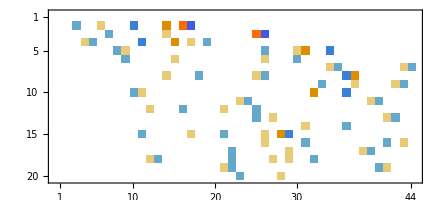

```mathematica
formatrix81//MatrixPlot
```

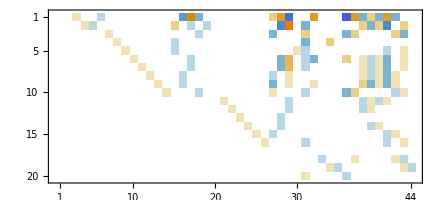

```mathematica
tmpRowReduce[formatrix81,30]//MatrixPlot
```

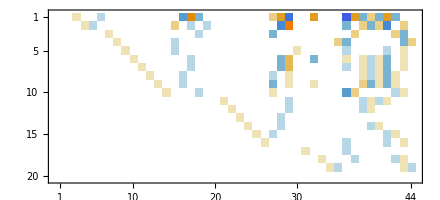

```mathematica
RowReduce[formatrix81]//MatrixPlot
```

```mathematica
Attributes[RowReduce]
```

{Protected}

```mathematica
{formatrix81,forexcepts81}=matrixTransform[excepts81,forbasis81];
```

```mathematica
formatrix81
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,1,0,0,0,-2,0,0,0,2,0,3,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,3,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-1,0,0,0,0,0,-2,0,0,0,2,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,2,0,0,-2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,-2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,1,-1,0},{0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,-2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,1,0,2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
RowReduce[formatrix81]//MatrixPlot
```

-Graphics-

```mathematica
basis82=Join[basis81,forbasis81[[2;;Length[forbasis81]]]];
```

```mathematica
vectors82=getVectors[H81,basis82];
```

```mathematica
Timing[{matrix82,excepts82}=matrixTransform[vectors82,basis82]][[1]]
```

can't decompose vector over basis

53)

can't decompose vector over basis

57)

can't decompose vector over basis

62)

424.9375

```mathematica
424.9375/60
```

7.08229

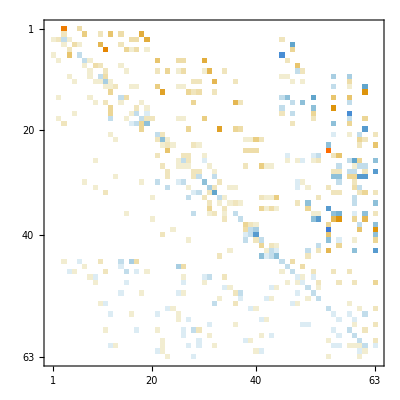

```mathematica
matrix82//MatrixPlot
```

```mathematica
matrix82
```

{{0,0,18,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,5,0,0,2,0,6,0,3,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,2,-2,1,0,0,0,0,0,0,0,0,0,0,0,3,3,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,3,1,0,0,0,8,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2,0,0,0,0,0,0,16,0,0,0,4,1,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,6,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,3,3,0,0,0,9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,3,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,2,0,0,0,1,0,0,0,0,0,2,0,4,0,1,3,0,0,0,1,8,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,-2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,-3,0,0,-3,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1,-3,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,8,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,2,0,0,1,1,0,0,0,5,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,1,0,0,-6,0,0},{0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,10,0,0,0,0,4,2,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,-2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-4,0,0,0,0,-6,0,0,0,6,0,0,6,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,2,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,8,2,0,0,0,0,0,0,0,0,0,-2,0,-4,0,0,0,0,0,0,0,0,-2,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,-4,0,0,0,12,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,4,0,0,0,1,-2,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,-2,0,0,0,4,0,0,0,0,0,0,-12,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,-2,0,0,1,0,0,-2,2,2,0,0,0,0,1,1,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,-2,0,0,4,0,0},{0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,-1,-2,4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,-4,0,0,4,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,4,0,0,0,0,0,10,0,0,4,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-8,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,-2,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,-4,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,5,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,1,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,0,0,0,0,2,0,0,6},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,-2,0,0,2,6,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-2,2,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,-1,0,1,2,0,0,0,0,0,-2,-6,4,0,0,-4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,1,0,0,0,1,0,0,0,0,0,0,2,0,0,5,1,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,1,-2,-2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,-2,-2,0,2,0,-8},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,-4,0,4,4,-8,-8,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,-2,0,0,0,-1,-2,0,0,0,-4,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,-2,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,1,0,0,0,-3,2,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,2,0,0,0,0,3,-2,0,0,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-2,0,2,-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,2,4,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-2,0,0,2,0,0,-2,1,0,0,0,0,0,0,2,1,1,5,0,0,0,0,0,0,0,2,0,0,0,0,0,0,-2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,1,2,1,0,0,0,0,0,0,0,0,0,0,2,0,-4,0,0,0,0,0,0,0,0,-2,0,0,0,-4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,2,0,0,0,0,0,0,4,1,3,1,0,0,0,0,0,4,0,0,0,-8,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,1,2,0,1,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,-4,-5,0,0,-1,0,-4,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,-4,-8,0,0,8,12,0,0,4,0,8,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,-2,0,0,-4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-2,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,-18,0,0,0,0,0,6,0,0,12},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-2,-8,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,-4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-2,0,2,-2,0,0,0,0,0,0,0,0,0,0,0,0,-4,0,-1,0,0,1,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,2,1,0,0,0,0,0,0,0,-2,0,0,0,4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,-2,-1,0,0,0,0,0,-2,0,2,0,8,0,0,0,0,-4,0,0,0,-8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,-4,-1,-2,-4,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,-1,0,0,0,2,0,0,0,-2,0,-3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,2,0,0,0,-2,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-2,0,0,0,2,0,0,0,2,0,0,2,0,0,0,0,0},{0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,-2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,-1,0,0,2,0,0,0,2,0,0,2,0,0,0,4},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,-2,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,2,-2,0,0,0,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,0,0,0,0,-1,1,0,0,0,0,0,0,1,0,-2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,0,0,0,0,0,1,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,-2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,1,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,-1,0,-2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-2,0,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-2,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,1,1,1,-2,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0}}

```mathematica
x=53;
vectors82[[x]]-Expand[matrix82[[x]].basis82]
```

ⅈ d[2,6] t[1,4,5]+ⅈ d[2,7] t[1,4,5]+ⅈ d[2,8] t[1,4,5]+ⅈ d[3,6] t[1,4,5]+ⅈ d[3,7] t[1,4,5]+ⅈ d[3,8] t[1,4,5]-2 ⅈ d[6,7] t[1,4,5]-2 ⅈ d[6,8] t[1,4,5]-2 ⅈ d[7,8] t[1,4,5]+4 ⅈ d[5,7] t[1,4,6]+4 ⅈ d[5,8] t[1,4,6]+4 ⅈ d[5,6] t[1,4,7]+4 ⅈ d[5,8] t[1,4,7]+4 ⅈ d[5,6] t[1,4,8]+4 ⅈ d[5,7] t[1,4,8]-3 ⅈ d[2,4] t[1,5,6]-3 ⅈ d[3,4] t[1,5,6]-ⅈ d[4,7] t[1,5,6]-ⅈ d[4,8] t[1,5,6]-3 ⅈ d[2,4] t[1,5,7]-3 ⅈ d[3,4] t[1,5,7]-ⅈ d[4,6] t[1,5,7]-ⅈ d[4,8] t[1,5,7]-3 ⅈ d[2,4] t[1,5,8]-3 ⅈ d[3,4] t[1,5,8]-ⅈ d[4,6] t[1,5,8]-ⅈ d[4,7] t[1,5,8]+ⅈ d[1,6] t[2,4,5]+ⅈ d[1,7] t[2,4,5]+ⅈ d[1,8] t[2,4,5]+ⅈ d[3,6] t[2,4,5]+ⅈ d[3,7] t[2,4,5]+ⅈ d[3,8] t[2,4,5]-2 ⅈ d[6,7] t[2,4,5]-2 ⅈ d[6,8] t[2,4,5]-2 ⅈ d[7,8] t[2,4,5]+4 ⅈ d[5,7] t[2,4,6]+4 ⅈ d[5,8] t[2,4,6]+4 ⅈ d[5,6] t[2,4,7]+4 ⅈ d[5,8] t[2,4,7]+4 ⅈ d[5,6] t[2,4,8]+4 ⅈ d[5,7] t[2,4,8]-3 ⅈ d[1,4] t[2,5,6]-3 ⅈ d[3,4] t[2,5,6]-ⅈ d[4,7] t[2,5,6]-ⅈ d[4,8] t[2,5,6]-3 ⅈ d[1,4] t[2,5,7]-3 ⅈ d[3,4] t[2,5,7]-ⅈ d[4,6] t[2,5,7]-ⅈ d[4,8] t[2,5,7]-3 ⅈ d[1,4] t[2,5,8]-3 ⅈ d[3,4] t[2,5,8]-ⅈ d[4,6] t[2,5,8]-ⅈ d[4,7] t[2,5,8]+ⅈ d[1,6] t[3,4,5]+ⅈ d[1,7] t[3,4,5]+ⅈ d[1,8] t[3,4,5]+ⅈ d[2,6] t[3,4,5]+ⅈ d[2,7] t[3,4,5]+ⅈ d[2,8] t[3,4,5]-2 ⅈ d[6,7] t[3,4,5]-2 ⅈ d[6,8] t[3,4,5]-2 ⅈ d[7,8] t[3,4,5]+4 ⅈ d[5,7] t[3,4,6]+4 ⅈ d[5,8] t[3,4,6]+4 ⅈ d[5,6] t[3,4,7]+4 ⅈ d[5,8] t[3,4,7]+4 ⅈ d[5,6] t[3,4,8]+4 ⅈ d[5,7] t[3,4,8]-3 ⅈ d[1,4] t[3,5,6]-3 ⅈ d[2,4] t[3,5,6]-ⅈ d[4,7] t[3,5,6]-ⅈ d[4,8] t[3,5,6]-3 ⅈ d[1,4] t[3,5,7]-3 ⅈ d[2,4] t[3,5,7]-ⅈ d[4,6] t[3,5,7]-ⅈ d[4,8] t[3,5,7]-3 ⅈ d[1,4] t[3,5,8]-3 ⅈ d[2,4] t[3,5,8]-ⅈ d[4,6] t[3,5,8]-ⅈ d[4,7] t[3,5,8]

```mathematica
x=57;
vectors82[[x]]-Expand[matrix82[[x]].basis82]
```

-2 ⅈ d[2,3] d[6,7] t[1,4,5]+ⅈ d[2,8] d[6,7] t[1,4,5]+ⅈ d[3,8] d[6,7] t[1,4,5]-2 ⅈ d[2,3] d[6,8] t[1,4,5]+ⅈ d[2,7] d[6,8] t[1,4,5]+ⅈ d[3,7] d[6,8] t[1,4,5]-2 ⅈ d[2,3] d[7,8] t[1,4,5]+ⅈ d[2,6] d[7,8] t[1,4,5]+ⅈ d[3,6] d[7,8] t[1,4,5]+4 ⅈ d[2,3] d[5,7] t[1,4,6]+4 ⅈ d[2,3] d[5,8] t[1,4,6]+4 ⅈ d[2,3] d[5,6] t[1,4,7]+4 ⅈ d[2,3] d[5,8] t[1,4,7]+4 ⅈ d[2,3] d[5,6] t[1,4,8]+4 ⅈ d[2,3] d[5,7] t[1,4,8]-ⅈ d[2,3] d[4,7] t[1,5,6]-ⅈ d[2,3] d[4,8] t[1,5,6]-3 ⅈ d[2,4] d[7,8] t[1,5,6]-3 ⅈ d[3,4] d[7,8] t[1,5,6]-ⅈ d[2,3] d[4,6] t[1,5,7]-ⅈ d[2,3] d[4,8] t[1,5,7]-3 ⅈ d[2,4] d[6,8] t[1,5,7]-3 ⅈ d[3,4] d[6,8] t[1,5,7]-ⅈ d[2,3] d[4,6] t[1,5,8]-ⅈ d[2,3] d[4,7] t[1,5,8]-3 ⅈ d[2,4] d[6,7] t[1,5,8]-3 ⅈ d[3,4] d[6,7] t[1,5,8]-2 ⅈ d[1,3] d[6,7] t[2,4,5]+ⅈ d[1,8] d[6,7] t[2,4,5]+ⅈ d[3,8] d[6,7] t[2,4,5]-2 ⅈ d[1,3] d[6,8] t[2,4,5]+ⅈ d[1,7] d[6,8] t[2,4,5]+ⅈ d[3,7] d[6,8] t[2,4,5]-2 ⅈ d[1,3] d[7,8] t[2,4,5]+ⅈ d[1,6] d[7,8] t[2,4,5]+ⅈ d[3,6] d[7,8] t[2,4,5]+4 ⅈ d[1,3] d[5,7] t[2,4,6]+4 ⅈ d[1,3] d[5,8] t[2,4,6]+4 ⅈ d[1,3] d[5,6] t[2,4,7]+4 ⅈ d[1,3] d[5,8] t[2,4,7]+4 ⅈ d[1,3] d[5,6] t[2,4,8]+4 ⅈ d[1,3] d[5,7] t[2,4,8]-ⅈ d[1,3] d[4,7] t[2,5,6]-ⅈ d[1,3] d[4,8] t[2,5,6]-3 ⅈ d[1,4] d[7,8] t[2,5,6]-3 ⅈ d[3,4] d[7,8] t[2,5,6]-ⅈ d[1,3] d[4,6] t[2,5,7]-ⅈ d[1,3] d[4,8] t[2,5,7]-3 ⅈ d[1,4] d[6,8] t[2,5,7]-3 ⅈ d[3,4] d[6,8] t[2,5,7]-ⅈ d[1,3] d[4,6] t[2,5,8]-ⅈ d[1,3] d[4,7] t[2,5,8]-3 ⅈ d[1,4] d[6,7] t[2,5,8]-3 ⅈ d[3,4] d[6,7] t[2,5,8]-2 ⅈ d[1,2] d[6,7] t[3,4,5]+ⅈ d[1,8] d[6,7] t[3,4,5]+ⅈ d[2,8] d[6,7] t[3,4,5]-2 ⅈ d[1,2] d[6,8] t[3,4,5]+ⅈ d[1,7] d[6,8] t[3,4,5]+ⅈ d[2,7] d[6,8] t[3,4,5]-2 ⅈ d[1,2] d[7,8] t[3,4,5]+ⅈ d[1,6] d[7,8] t[3,4,5]+ⅈ d[2,6] d[7,8] t[3,4,5]+4 ⅈ d[1,2] d[5,7] t[3,4,6]+4 ⅈ d[1,2] d[5,8] t[3,4,6]+4 ⅈ d[1,2] d[5,6] t[3,4,7]+4 ⅈ d[1,2] d[5,8] t[3,4,7]+4 ⅈ d[1,2] d[5,6] t[3,4,8]+4 ⅈ d[1,2] d[5,7] t[3,4,8]-ⅈ d[1,2] d[4,7] t[3,5,6]-ⅈ d[1,2] d[4,8] t[3,5,6]-3 ⅈ d[1,4] d[7,8] t[3,5,6]-3 ⅈ d[2,4] d[7,8] t[3,5,6]-ⅈ d[1,2] d[4,6] t[3,5,7]-ⅈ d[1,2] d[4,8] t[3,5,7]-3 ⅈ d[1,4] d[6,8] t[3,5,7]-3 ⅈ d[2,4] d[6,8] t[3,5,7]-ⅈ d[1,2] d[4,6] t[3,5,8]-ⅈ d[1,2] d[4,7] t[3,5,8]-3 ⅈ d[1,4] d[6,7] t[3,5,8]-3 ⅈ d[2,4] d[6,7] t[3,5,8]

```mathematica
x=62;
vectors82[[x]]-Expand[matrix82[[x]].basis82]
```

-2 ⅈ d[2,7] d[3,6] t[1,4,5]-2 ⅈ d[2,8] d[3,6] t[1,4,5]-2 ⅈ d[2,6] d[3,7] t[1,4,5]-2 ⅈ d[2,8] d[3,7] t[1,4,5]-2 ⅈ d[2,6] d[3,8] t[1,4,5]-2 ⅈ d[2,7] d[3,8] t[1,4,5]+2 ⅈ d[2,8] d[6,7] t[1,4,5]+2 ⅈ d[3,8] d[6,7] t[1,4,5]+2 ⅈ d[2,7] d[6,8] t[1,4,5]+2 ⅈ d[3,7] d[6,8] t[1,4,5]+2 ⅈ d[2,6] d[7,8] t[1,4,5]+2 ⅈ d[3,6] d[7,8] t[1,4,5]-5 ⅈ d[2,8] d[5,7] t[1,4,6]-5 ⅈ d[3,8] d[5,7] t[1,4,6]-5 ⅈ d[2,7] d[5,8] t[1,4,6]-5 ⅈ d[3,7] d[5,8] t[1,4,6]-5 ⅈ d[2,8] d[5,6] t[1,4,7]-5 ⅈ d[3,8] d[5,6] t[1,4,7]-5 ⅈ d[2,6] d[5,8] t[1,4,7]-5 ⅈ d[3,6] d[5,8] t[1,4,7]-5 ⅈ d[2,7] d[5,6] t[1,4,8]-5 ⅈ d[3,7] d[5,6] t[1,4,8]-5 ⅈ d[2,6] d[5,7] t[1,4,8]-5 ⅈ d[3,6] d[5,7] t[1,4,8]+4 ⅈ d[2,7] d[3,4] t[1,5,6]+4 ⅈ d[2,8] d[3,4] t[1,5,6]+4 ⅈ d[2,4] d[3,7] t[1,5,6]+4 ⅈ d[2,4] d[3,8] t[1,5,6]+ⅈ d[2,8] d[4,7] t[1,5,6]+ⅈ d[3,8] d[4,7] t[1,5,6]+ⅈ d[2,7] d[4,8] t[1,5,6]+ⅈ d[3,7] d[4,8] t[1,5,6]+4 ⅈ d[2,6] d[3,4] t[1,5,7]+4 ⅈ d[2,8] d[3,4] t[1,5,7]+4 ⅈ d[2,4] d[3,6] t[1,5,7]+4 ⅈ d[2,4] d[3,8] t[1,5,7]+ⅈ d[2,8] d[4,6] t[1,5,7]+ⅈ d[3,8] d[4,6] t[1,5,7]+ⅈ d[2,6] d[4,8] t[1,5,7]+ⅈ d[3,6] d[4,8] t[1,5,7]+4 ⅈ d[2,6] d[3,4] t[1,5,8]+4 ⅈ d[2,7] d[3,4] t[1,5,8]+4 ⅈ d[2,4] d[3,6] t[1,5,8]+4 ⅈ d[2,4] d[3,7] t[1,5,8]+ⅈ d[2,7] d[4,6] t[1,5,8]+ⅈ d[3,7] d[4,6] t[1,5,8]+ⅈ d[2,6] d[4,7] t[1,5,8]+ⅈ d[3,6] d[4,7] t[1,5,8]-2 ⅈ d[1,7] d[3,6] t[2,4,5]-2 ⅈ d[1,8] d[3,6] t[2,4,5]-2 ⅈ d[1,6] d[3,7] t[2,4,5]-2 ⅈ d[1,8] d[3,7] t[2,4,5]-2 ⅈ d[1,6] d[3,8] t[2,4,5]-2 ⅈ d[1,7] d[3,8] t[2,4,5]+2 ⅈ d[1,8] d[6,7] t[2,4,5]+2 ⅈ d[3,8] d[6,7] t[2,4,5]+2 ⅈ d[1,7] d[6,8] t[2,4,5]+2 ⅈ d[3,7] d[6,8] t[2,4,5]+2 ⅈ d[1,6] d[7,8] t[2,4,5]+2 ⅈ d[3,6] d[7,8] t[2,4,5]-5 ⅈ d[1,8] d[5,7] t[2,4,6]-5 ⅈ d[3,8] d[5,7] t[2,4,6]-5 ⅈ d[1,7] d[5,8] t[2,4,6]-5 ⅈ d[3,7] d[5,8] t[2,4,6]-5 ⅈ d[1,8] d[5,6] t[2,4,7]-5 ⅈ d[3,8] d[5,6] t[2,4,7]-5 ⅈ d[1,6] d[5,8] t[2,4,7]-5 ⅈ d[3,6] d[5,8] t[2,4,7]-5 ⅈ d[1,7] d[5,6] t[2,4,8]-5 ⅈ d[3,7] d[5,6] t[2,4,8]-5 ⅈ d[1,6] d[5,7] t[2,4,8]-5 ⅈ d[3,6] d[5,7] t[2,4,8]+4 ⅈ d[1,7] d[3,4] t[2,5,6]+4 ⅈ d[1,8] d[3,4] t[2,5,6]+4 ⅈ d[1,4] d[3,7] t[2,5,6]+4 ⅈ d[1,4] d[3,8] t[2,5,6]+ⅈ d[1,8] d[4,7] t[2,5,6]+ⅈ d[3,8] d[4,7] t[2,5,6]+ⅈ d[1,7] d[4,8] t[2,5,6]+ⅈ d[3,7] d[4,8] t[2,5,6]+4 ⅈ d[1,6] d[3,4] t[2,5,7]+4 ⅈ d[1,8] d[3,4] t[2,5,7]+4 ⅈ d[1,4] d[3,6] t[2,5,7]+4 ⅈ d[1,4] d[3,8] t[2,5,7]+ⅈ d[1,8] d[4,6] t[2,5,7]+ⅈ d[3,8] d[4,6] t[2,5,7]+ⅈ d[1,6] d[4,8] t[2,5,7]+ⅈ d[3,6] d[4,8] t[2,5,7]+4 ⅈ d[1,6] d[3,4] t[2,5,8]+4 ⅈ d[1,7] d[3,4] t[2,5,8]+4 ⅈ d[1,4] d[3,6] t[2,5,8]+4 ⅈ d[1,4] d[3,7] t[2,5,8]+ⅈ d[1,7] d[4,6] t[2,5,8]+ⅈ d[3,7] d[4,6] t[2,5,8]+ⅈ d[1,6] d[4,7] t[2,5,8]+ⅈ d[3,6] d[4,7] t[2,5,8]-2 ⅈ d[1,7] d[2,6] t[3,4,5]-2 ⅈ d[1,8] d[2,6] t[3,4,5]-2 ⅈ d[1,6] d[2,7] t[3,4,5]-2 ⅈ d[1,8] d[2,7] t[3,4,5]-2 ⅈ d[1,6] d[2,8] t[3,4,5]-2 ⅈ d[1,7] d[2,8] t[3,4,5]+2 ⅈ d[1,8] d[6,7] t[3,4,5]+2 ⅈ d[2,8] d[6,7] t[3,4,5]+2 ⅈ d[1,7] d[6,8] t[3,4,5]+2 ⅈ d[2,7] d[6,8] t[3,4,5]+2 ⅈ d[1,6] d[7,8] t[3,4,5]+2 ⅈ d[2,6] d[7,8] t[3,4,5]-5 ⅈ d[1,8] d[5,7] t[3,4,6]-5 ⅈ d[2,8] d[5,7] t[3,4,6]-5 ⅈ d[1,7] d[5,8] t[3,4,6]-5 ⅈ d[2,7] d[5,8] t[3,4,6]-5 ⅈ d[1,8] d[5,6] t[3,4,7]-5 ⅈ d[2,8] d[5,6] t[3,4,7]-5 ⅈ d[1,6] d[5,8] t[3,4,7]-5 ⅈ d[2,6] d[5,8] t[3,4,7]-5 ⅈ d[1,7] d[5,6] t[3,4,8]-5 ⅈ d[2,7] d[5,6] t[3,4,8]-5 ⅈ d[1,6] d[5,7] t[3,4,8]-5 ⅈ d[2,6] d[5,7] t[3,4,8]+4 ⅈ d[1,7] d[2,4] t[3,5,6]+4 ⅈ d[1,8] d[2,4] t[3,5,6]+4 ⅈ d[1,4] d[2,7] t[3,5,6]+4 ⅈ d[1,4] d[2,8] t[3,5,6]+ⅈ d[1,8] d[4,7] t[3,5,6]+ⅈ d[2,8] d[4,7] t[3,5,6]+ⅈ d[1,7] d[4,8] t[3,5,6]+ⅈ d[2,7] d[4,8] t[3,5,6]+4 ⅈ d[1,6] d[2,4] t[3,5,7]+4 ⅈ d[1,8] d[2,4] t[3,5,7]+4 ⅈ d[1,4] d[2,6] t[3,5,7]+4 ⅈ d[1,4] d[2,8] t[3,5,7]+ⅈ d[1,8] d[4,6] t[3,5,7]+ⅈ d[2,8] d[4,6] t[3,5,7]+ⅈ d[1,6] d[4,8] t[3,5,7]+ⅈ d[2,6] d[4,8] t[3,5,7]+4 ⅈ d[1,6] d[2,4] t[3,5,8]+4 ⅈ d[1,7] d[2,4] t[3,5,8]+4 ⅈ d[1,4] d[2,6] t[3,5,8]+4 ⅈ d[1,4] d[2,7] t[3,5,8]+ⅈ d[1,7] d[4,6] t[3,5,8]+ⅈ d[2,7] d[4,6] t[3,5,8]+ⅈ d[1,6] d[4,7] t[3,5,8]+ⅈ d[2,6] d[4,7] t[3,5,8]

```mathematica
basis82//TableForm
```

```mathematica
{{1}, {d[1,2]+d[1,3]+d[2,3]+d[6,7]+d[6,8]+d[7,8]}, {d[1,4]+d[2,4]+d[3,4]+d[5,6]+d[5,7]+d[5,8]}, {d[1,5]+d[2,5]+d[3,5]+d[4,6]+d[4,7]+d[4,8]}, {d[1,6]+d[1,7]+d[1,8]+d[2,6]+d[2,7]+d[2,8]+d[3,6]+d[3,7]+d[3,8]}, {d[4,5]}, {d[1,4] d[2,3]+d[1,3] d[2,4]+d[1,2] d[3,4]+d[5,8] d[6,7]+d[5,7] d[6,8]+d[5,6] d[7,8]}, {d[1,5] d[2,3]+d[1,3] d[2,5]+d[1,2] d[3,5]+d[4,8] d[6,7]+d[4,7] d[6,8]+d[4,6] d[7,8]}, {d[1,6] d[2,3]+d[1,7] d[2,3]+d[1,8] d[2,3]+d[1,3] d[2,6]+d[1,3] d[2,7]+d[1,3] d[2,8]+d[1,2] d[3,6]+d[1,2] d[3,7]+d[1,2] d[3,8]+d[1,8] d[6,7]+d[2,8] d[6,7]+d[3,8] d[6,7]+d[1,7] d[6,8]+d[2,7] d[6,8]+d[3,7] d[6,8]+d[1,6] d[7,8]+d[2,6] d[7,8]+d[3,6] d[7,8]}, {d[1,5] d[2,4]+d[1,4] d[2,5]+d[1,5] d[3,4]+d[2,5] d[3,4]+d[1,4] d[3,5]+d[2,4] d[3,5]+d[4,7] d[5,6]+d[4,8] d[5,6]+d[4,6] d[5,7]+d[4,8] d[5,7]+d[4,6] d[5,8]+d[4,7] d[5,8]}, {d[1,6] d[2,4]+d[1,7] d[2,4]+d[1,8] d[2,4]+d[1,4] d[2,6]+d[1,4] d[2,7]+d[1,4] d[2,8]+d[1,6] d[3,4]+d[1,7] d[3,4]+d[1,8] d[3,4]+d[2,6] d[3,4]+d[2,7] d[3,4]+d[2,8] d[3,4]+d[1,4] d[3,6]+d[2,4] d[3,6]+d[1,4] d[3,7]+d[2,4] d[3,7]+d[1,4] d[3,8]+d[2,4] d[3,8]+d[1,7] d[5,6]+d[1,8] d[5,6]+d[2,7] d[5,6]+d[2,8] d[5,6]+d[3,7] d[5,6]+d[3,8] d[5,6]+d[1,6] d[5,7]+d[1,8] d[5,7]+d[2,6] d[5,7]+d[2,8] d[5,7]+d[3,6] d[5,7]+d[3,8] d[5,7]+d[1,6] d[5,8]+d[1,7] d[5,8]+d[2,6] d[5,8]+d[2,7] d[5,8]+d[3,6] d[5,8]+d[3,7] d[5,8]}, {d[1,6] d[2,5]+d[1,7] d[2,5]+d[1,8] d[2,5]+d[1,5] d[2,6]+d[1,5] d[2,7]+d[1,5] d[2,8]+d[1,6] d[3,5]+d[1,7] d[3,5]+d[1,8] d[3,5]+d[2,6] d[3,5]+d[2,7] d[3,5]+d[2,8] d[3,5]+d[1,5] d[3,6]+d[2,5] d[3,6]+d[1,5] d[3,7]+d[2,5] d[3,7]+d[1,5] d[3,8]+d[2,5] d[3,8]+d[1,7] d[4,6]+d[1,8] d[4,6]+d[2,7] d[4,6]+d[2,8] d[4,6]+d[3,7] d[4,6]+d[3,8] d[4,6]+d[1,6] d[4,7]+d[1,8] d[4,7]+d[2,6] d[4,7]+d[2,8] d[4,7]+d[3,6] d[4,7]+d[3,8] d[4,7]+d[1,6] d[4,8]+d[1,7] d[4,8]+d[2,6] d[4,8]+d[2,7] d[4,8]+d[3,6] d[4,8]+d[3,7] d[4,8]}, {d[1,7] d[2,6]+d[1,8] d[2,6]+d[1,6] d[2,7]+d[1,8] d[2,7]+d[1,6] d[2,8]+d[1,7] d[2,8]+d[1,7] d[3,6]+d[1,8] d[3,6]+d[2,7] d[3,6]+d[2,8] d[3,6]+d[1,6] d[3,7]+d[1,8] d[3,7]+d[2,6] d[3,7]+d[2,8] d[3,7]+d[1,6] d[3,8]+d[1,7] d[3,8]+d[2,6] d[3,8]+d[2,7] d[3,8]}, {d[1,2] d[4,5]+d[1,3] d[4,5]+d[2,3] d[4,5]+d[4,5] d[6,7]+d[4,5] d[6,8]+d[4,5] d[7,8]}, {d[1,2] d[4,6]+d[1,3] d[4,6]+d[2,3] d[4,6]+d[1,2] d[4,7]+d[1,3] d[4,7]+d[2,3] d[4,7]+d[1,2] d[4,8]+d[1,3] d[4,8]+d[2,3] d[4,8]+d[1,5] d[6,7]+d[2,5] d[6,7]+d[3,5] d[6,7]+d[1,5] d[6,8]+d[2,5] d[6,8]+d[3,5] d[6,8]+d[1,5] d[7,8]+d[2,5] d[7,8]+d[3,5] d[7,8]}, {d[1,5] d[4,6]+d[2,5] d[4,6]+d[3,5] d[4,6]+d[1,5] d[4,7]+d[2,5] d[4,7]+d[3,5] d[4,7]+d[1,5] d[4,8]+d[2,5] d[4,8]+d[3,5] d[4,8]}, {d[1,6] d[4,5]+d[1,7] d[4,5]+d[1,8] d[4,5]+d[2,6] d[4,5]+d[2,7] d[4,5]+d[2,8] d[4,5]+d[3,6] d[4,5]+d[3,7] d[4,5]+d[3,8] d[4,5]}, {d[1,2] d[5,6]+d[1,3] d[5,6]+d[2,3] d[5,6]+d[1,2] d[5,7]+d[1,3] d[5,7]+d[2,3] d[5,7]+d[1,2] d[5,8]+d[1,3] d[5,8]+d[2,3] d[5,8]+d[1,4] d[6,7]+d[2,4] d[6,7]+d[3,4] d[6,7]+d[1,4] d[6,8]+d[2,4] d[6,8]+d[3,4] d[6,8]+d[1,4] d[7,8]+d[2,4] d[7,8]+d[3,4] d[7,8]}, {d[1,4] d[5,6]+d[2,4] d[5,6]+d[3,4] d[5,6]+d[1,4] d[5,7]+d[2,4] d[5,7]+d[3,4] d[5,7]+d[1,4] d[5,8]+d[2,4] d[5,8]+d[3,4] d[5,8]}, {d[1,2] d[6,7]+d[1,3] d[6,7]+d[2,3] d[6,7]+d[1,2] d[6,8]+d[1,3] d[6,8]+d[2,3] d[6,8]+d[1,2] d[7,8]+d[1,3] d[7,8]+d[2,3] d[7,8]}, {d[1,6] d[2,5] d[3,4]+d[1,7] d[2,5] d[3,4]+d[1,8] d[2,5] d[3,4]+d[1,5] d[2,6] d[3,4]+d[1,5] d[2,7] d[3,4]+d[1,5] d[2,8] d[3,4]+d[1,6] d[2,4] d[3,5]+d[1,7] d[2,4] d[3,5]+d[1,8] d[2,4] d[3,5]+d[1,4] d[2,6] d[3,5]+d[1,4] d[2,7] d[3,5]+d[1,4] d[2,8] d[3,5]+d[1,5] d[2,4] d[3,6]+d[1,4] d[2,5] d[3,6]+d[1,5] d[2,4] d[3,7]+d[1,4] d[2,5] d[3,7]+d[1,5] d[2,4] d[3,8]+d[1,4] d[2,5] d[3,8]+d[1,8] d[4,7] d[5,6]+d[2,8] d[4,7] d[5,6]+d[3,8] d[4,7] d[5,6]+d[1,7] d[4,8] d[5,6]+d[2,7] d[4,8] d[5,6]+d[3,7] d[4,8] d[5,6]+d[1,8] d[4,6] d[5,7]+d[2,8] d[4,6] d[5,7]+d[3,8] d[4,6] d[5,7]+d[1,6] d[4,8] d[5,7]+d[2,6] d[4,8] d[5,7]+d[3,6] d[4,8] d[5,7]+d[1,7] d[4,6] d[5,8]+d[2,7] d[4,6] d[5,8]+d[3,7] d[4,6] d[5,8]+d[1,6] d[4,7] d[5,8]+d[2,6] d[4,7] d[5,8]+d[3,6] d[4,7] d[5,8]}, {d[1,7] d[2,6] d[3,4]+d[1,8] d[2,6] d[3,4]+d[1,6] d[2,7] d[3,4]+d[1,8] d[2,7] d[3,4]+d[1,6] d[2,8] d[3,4]+d[1,7] d[2,8] d[3,4]+d[1,7] d[2,4] d[3,6]+d[1,8] d[2,4] d[3,6]+d[1,4] d[2,7] d[3,6]+d[1,4] d[2,8] d[3,6]+d[1,6] d[2,4] d[3,7]+d[1,8] d[2,4] d[3,7]+d[1,4] d[2,6] d[3,7]+d[1,4] d[2,8] d[3,7]+d[1,6] d[2,4] d[3,8]+d[1,7] d[2,4] d[3,8]+d[1,4] d[2,6] d[3,8]+d[1,4] d[2,7] d[3,8]+d[1,8] d[2,7] d[5,6]+d[1,7] d[2,8] d[5,6]+d[1,8] d[3,7] d[5,6]+d[2,8] d[3,7] d[5,6]+d[1,7] d[3,8] d[5,6]+d[2,7] d[3,8] d[5,6]+d[1,8] d[2,6] d[5,7]+d[1,6] d[2,8] d[5,7]+d[1,8] d[3,6] d[5,7]+d[2,8] d[3,6] d[5,7]+d[1,6] d[3,8] d[5,7]+d[2,6] d[3,8] d[5,7]+d[1,7] d[2,6] d[5,8]+d[1,6] d[2,7] d[5,8]+d[1,7] d[3,6] d[5,8]+d[2,7] d[3,6] d[5,8]+d[1,6] d[3,7] d[5,8]+d[2,6] d[3,7] d[5,8]}, {d[1,7] d[2,6] d[3,5]+d[1,8] d[2,6] d[3,5]+d[1,6] d[2,7] d[3,5]+d[1,8] d[2,7] d[3,5]+d[1,6] d[2,8] d[3,5]+d[1,7] d[2,8] d[3,5]+d[1,7] d[2,5] d[3,6]+d[1,8] d[2,5] d[3,6]+d[1,5] d[2,7] d[3,6]+d[1,5] d[2,8] d[3,6]+d[1,6] d[2,5] d[3,7]+d[1,8] d[2,5] d[3,7]+d[1,5] d[2,6] d[3,7]+d[1,5] d[2,8] d[3,7]+d[1,6] d[2,5] d[3,8]+d[1,7] d[2,5] d[3,8]+d[1,5] d[2,6] d[3,8]+d[1,5] d[2,7] d[3,8]+d[1,8] d[2,7] d[4,6]+d[1,7] d[2,8] d[4,6]+d[1,8] d[3,7] d[4,6]+d[2,8] d[3,7] d[4,6]+d[1,7] d[3,8] d[4,6]+d[2,7] d[3,8] d[4,6]+d[1,8] d[2,6] d[4,7]+d[1,6] d[2,8] d[4,7]+d[1,8] d[3,6] d[4,7]+d[2,8] d[3,6] d[4,7]+d[1,6] d[3,8] d[4,7]+d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[4,8]+d[1,6] d[2,7] d[4,8]+d[1,7] d[3,6] d[4,8]+d[2,7] d[3,6] d[4,8]+d[1,6] d[3,7] d[4,8]+d[2,6] d[3,7] d[4,8]}, {d[1,8] d[2,7] d[3,6]+d[1,7] d[2,8] d[3,6]+d[1,8] d[2,6] d[3,7]+d[1,6] d[2,8] d[3,7]+d[1,7] d[2,6] d[3,8]+d[1,6] d[2,7] d[3,8]}, {d[1,5] d[2,3] d[4,6]+d[1,3] d[2,5] d[4,6]+d[1,2] d[3,5] d[4,6]+d[1,5] d[2,3] d[4,7]+d[1,3] d[2,5] d[4,7]+d[1,2] d[3,5] d[4,7]+d[1,5] d[2,3] d[4,8]+d[1,3] d[2,5] d[4,8]+d[1,2] d[3,5] d[4,8]+d[1,5] d[4,8] d[6,7]+d[2,5] d[4,8] d[6,7]+d[3,5] d[4,8] d[6,7]+d[1,5] d[4,7] d[6,8]+d[2,5] d[4,7] d[6,8]+d[3,5] d[4,7] d[6,8]+d[1,5] d[4,6] d[7,8]+d[2,5] d[4,6] d[7,8]+d[3,5] d[4,6] d[7,8]}, {d[1,6] d[2,3] d[4,5]+d[1,7] d[2,3] d[4,5]+d[1,8] d[2,3] d[4,5]+d[1,3] d[2,6] d[4,5]+d[1,3] d[2,7] d[4,5]+d[1,3] d[2,8] d[4,5]+d[1,2] d[3,6] d[4,5]+d[1,2] d[3,7] d[4,5]+d[1,2] d[3,8] d[4,5]+d[1,8] d[4,5] d[6,7]+d[2,8] d[4,5] d[6,7]+d[3,8] d[4,5] d[6,7]+d[1,7] d[4,5] d[6,8]+d[2,7] d[4,5] d[6,8]+d[3,7] d[4,5] d[6,8]+d[1,6] d[4,5] d[7,8]+d[2,6] d[4,5] d[7,8]+d[3,6] d[4,5] d[7,8]}, {d[1,7] d[2,3] d[4,6]+d[1,8] d[2,3] d[4,6]+d[1,3] d[2,7] d[4,6]+d[1,3] d[2,8] d[4,6]+d[1,2] d[3,7] d[4,6]+d[1,2] d[3,8] d[4,6]+d[1,6] d[2,3] d[4,7]+d[1,8] d[2,3] d[4,7]+d[1,3] d[2,6] d[4,7]+d[1,3] d[2,8] d[4,7]+d[1,2] d[3,6] d[4,7]+d[1,2] d[3,8] d[4,7]+d[1,6] d[2,3] d[4,8]+d[1,7] d[2,3] d[4,8]+d[1,3] d[2,6] d[4,8]+d[1,3] d[2,7] d[4,8]+d[1,2] d[3,6] d[4,8]+d[1,2] d[3,7] d[4,8]+d[1,8] d[2,5] d[6,7]+d[1,5] d[2,8] d[6,7]+d[1,8] d[3,5] d[6,7]+d[2,8] d[3,5] d[6,7]+d[1,5] d[3,8] d[6,7]+d[2,5] d[3,8] d[6,7]+d[1,7] d[2,5] d[6,8]+d[1,5] d[2,7] d[6,8]+d[1,7] d[3,5] d[6,8]+d[2,7] d[3,5] d[6,8]+d[1,5] d[3,7] d[6,8]+d[2,5] d[3,7] d[6,8]+d[1,6] d[2,5] d[7,8]+d[1,5] d[2,6] d[7,8]+d[1,6] d[3,5] d[7,8]+d[2,6] d[3,5] d[7,8]+d[1,5] d[3,6] d[7,8]+d[2,5] d[3,6] d[7,8]}, {d[1,7] d[2,5] d[4,6]+d[1,8] d[2,5] d[4,6]+d[1,5] d[2,7] d[4,6]+d[1,5] d[2,8] d[4,6]+d[1,7] d[3,5] d[4,6]+d[1,8] d[3,5] d[4,6]+d[2,7] d[3,5] d[4,6]+d[2,8] d[3,5] d[4,6]+d[1,5] d[3,7] d[4,6]+d[2,5] d[3,7] d[4,6]+d[1,5] d[3,8] d[4,6]+d[2,5] d[3,8] d[4,6]+d[1,6] d[2,5] d[4,7]+d[1,8] d[2,5] d[4,7]+d[1,5] d[2,6] d[4,7]+d[1,5] d[2,8] d[4,7]+d[1,6] d[3,5] d[4,7]+d[1,8] d[3,5] d[4,7]+d[2,6] d[3,5] d[4,7]+d[2,8] d[3,5] d[4,7]+d[1,5] d[3,6] d[4,7]+d[2,5] d[3,6] d[4,7]+d[1,5] d[3,8] d[4,7]+d[2,5] d[3,8] d[4,7]+d[1,6] d[2,5] d[4,8]+d[1,7] d[2,5] d[4,8]+d[1,5] d[2,6] d[4,8]+d[1,5] d[2,7] d[4,8]+d[1,6] d[3,5] d[4,8]+d[1,7] d[3,5] d[4,8]+d[2,6] d[3,5] d[4,8]+d[2,7] d[3,5] d[4,8]+d[1,5] d[3,6] d[4,8]+d[2,5] d[3,6] d[4,8]+d[1,5] d[3,7] d[4,8]+d[2,5] d[3,7] d[4,8]}, {d[1,7] d[2,6] d[4,5]+d[1,8] d[2,6] d[4,5]+d[1,6] d[2,7] d[4,5]+d[1,8] d[2,7] d[4,5]+d[1,6] d[2,8] d[4,5]+d[1,7] d[2,8] d[4,5]+d[1,7] d[3,6] d[4,5]+d[1,8] d[3,6] d[4,5]+d[2,7] d[3,6] d[4,5]+d[2,8] d[3,6] d[4,5]+d[1,6] d[3,7] d[4,5]+d[1,8] d[3,7] d[4,5]+d[2,6] d[3,7] d[4,5]+d[2,8] d[3,7] d[4,5]+d[1,6] d[3,8] d[4,5]+d[1,7] d[3,8] d[4,5]+d[2,6] d[3,8] d[4,5]+d[2,7] d[3,8] d[4,5]}, {d[1,4] d[2,3] d[5,6]+d[1,3] d[2,4] d[5,6]+d[1,2] d[3,4] d[5,6]+d[1,4] d[2,3] d[5,7]+d[1,3] d[2,4] d[5,7]+d[1,2] d[3,4] d[5,7]+d[1,4] d[2,3] d[5,8]+d[1,3] d[2,4] d[5,8]+d[1,2] d[3,4] d[5,8]+d[1,4] d[5,8] d[6,7]+d[2,4] d[5,8] d[6,7]+d[3,4] d[5,8] d[6,7]+d[1,4] d[5,7] d[6,8]+d[2,4] d[5,7] d[6,8]+d[3,4] d[5,7] d[6,8]+d[1,4] d[5,6] d[7,8]+d[2,4] d[5,6] d[7,8]+d[3,4] d[5,6] d[7,8]}, {d[1,7] d[2,3] d[5,6]+d[1,8] d[2,3] d[5,6]+d[1,3] d[2,7] d[5,6]+d[1,3] d[2,8] d[5,6]+d[1,2] d[3,7] d[5,6]+d[1,2] d[3,8] d[5,6]+d[1,6] d[2,3] d[5,7]+d[1,8] d[2,3] d[5,7]+d[1,3] d[2,6] d[5,7]+d[1,3] d[2,8] d[5,7]+d[1,2] d[3,6] d[5,7]+d[1,2] d[3,8] d[5,7]+d[1,6] d[2,3] d[5,8]+d[1,7] d[2,3] d[5,8]+d[1,3] d[2,6] d[5,8]+d[1,3] d[2,7] d[5,8]+d[1,2] d[3,6] d[5,8]+d[1,2] d[3,7] d[5,8]+d[1,8] d[2,4] d[6,7]+d[1,4] d[2,8] d[6,7]+d[1,8] d[3,4] d[6,7]+d[2,8] d[3,4] d[6,7]+d[1,4] d[3,8] d[6,7]+d[2,4] d[3,8] d[6,7]+d[1,7] d[2,4] d[6,8]+d[1,4] d[2,7] d[6,8]+d[1,7] d[3,4] d[6,8]+d[2,7] d[3,4] d[6,8]+d[1,4] d[3,7] d[6,8]+d[2,4] d[3,7] d[6,8]+d[1,6] d[2,4] d[7,8]+d[1,4] d[2,6] d[7,8]+d[1,6] d[3,4] d[7,8]+d[2,6] d[3,4] d[7,8]+d[1,4] d[3,6] d[7,8]+d[2,4] d[3,6] d[7,8]}, {d[1,7] d[2,4] d[5,6]+d[1,8] d[2,4] d[5,6]+d[1,4] d[2,7] d[5,6]+d[1,4] d[2,8] d[5,6]+d[1,7] d[3,4] d[5,6]+d[1,8] d[3,4] d[5,6]+d[2,7] d[3,4] d[5,6]+d[2,8] d[3,4] d[5,6]+d[1,4] d[3,7] d[5,6]+d[2,4] d[3,7] d[5,6]+d[1,4] d[3,8] d[5,6]+d[2,4] d[3,8] d[5,6]+d[1,6] d[2,4] d[5,7]+d[1,8] d[2,4] d[5,7]+d[1,4] d[2,6] d[5,7]+d[1,4] d[2,8] d[5,7]+d[1,6] d[3,4] d[5,7]+d[1,8] d[3,4] d[5,7]+d[2,6] d[3,4] d[5,7]+d[2,8] d[3,4] d[5,7]+d[1,4] d[3,6] d[5,7]+d[2,4] d[3,6] d[5,7]+d[1,4] d[3,8] d[5,7]+d[2,4] d[3,8] d[5,7]+d[1,6] d[2,4] d[5,8]+d[1,7] d[2,4] d[5,8]+d[1,4] d[2,6] d[5,8]+d[1,4] d[2,7] d[5,8]+d[1,6] d[3,4] d[5,8]+d[1,7] d[3,4] d[5,8]+d[2,6] d[3,4] d[5,8]+d[2,7] d[3,4] d[5,8]+d[1,4] d[3,6] d[5,8]+d[2,4] d[3,6] d[5,8]+d[1,4] d[3,7] d[5,8]+d[2,4] d[3,7] d[5,8]}, {d[1,4] d[2,3] d[6,7]+d[1,3] d[2,4] d[6,7]+d[1,2] d[3,4] d[6,7]+d[1,2] d[5,8] d[6,7]+d[1,3] d[5,8] d[6,7]+d[2,3] d[5,8] d[6,7]+d[1,4] d[2,3] d[6,8]+d[1,3] d[2,4] d[6,8]+d[1,2] d[3,4] d[6,8]+d[1,2] d[5,7] d[6,8]+d[1,3] d[5,7] d[6,8]+d[2,3] d[5,7] d[6,8]+d[1,4] d[2,3] d[7,8]+d[1,3] d[2,4] d[7,8]+d[1,2] d[3,4] d[7,8]+d[1,2] d[5,6] d[7,8]+d[1,3] d[5,6] d[7,8]+d[2,3] d[5,6] d[7,8]}, {d[1,5] d[2,3] d[6,7]+d[1,3] d[2,5] d[6,7]+d[1,2] d[3,5] d[6,7]+d[1,2] d[4,8] d[6,7]+d[1,3] d[4,8] d[6,7]+d[2,3] d[4,8] d[6,7]+d[1,5] d[2,3] d[6,8]+d[1,3] d[2,5] d[6,8]+d[1,2] d[3,5] d[6,8]+d[1,2] d[4,7] d[6,8]+d[1,3] d[4,7] d[6,8]+d[2,3] d[4,7] d[6,8]+d[1,5] d[2,3] d[7,8]+d[1,3] d[2,5] d[7,8]+d[1,2] d[3,5] d[7,8]+d[1,2] d[4,6] d[7,8]+d[1,3] d[4,6] d[7,8]+d[2,3] d[4,6] d[7,8]}, {d[1,8] d[2,3] d[6,7]+d[1,3] d[2,8] d[6,7]+d[1,2] d[3,8] d[6,7]+d[1,7] d[2,3] d[6,8]+d[1,3] d[2,7] d[6,8]+d[1,2] d[3,7] d[6,8]+d[1,6] d[2,3] d[7,8]+d[1,3] d[2,6] d[7,8]+d[1,2] d[3,6] d[7,8]}, {d[1,2] d[4,7] d[5,6]+d[1,3] d[4,7] d[5,6]+d[2,3] d[4,7] d[5,6]+d[1,2] d[4,8] d[5,6]+d[1,3] d[4,8] d[5,6]+d[2,3] d[4,8] d[5,6]+d[1,2] d[4,6] d[5,7]+d[1,3] d[4,6] d[5,7]+d[2,3] d[4,6] d[5,7]+d[1,2] d[4,8] d[5,7]+d[1,3] d[4,8] d[5,7]+d[2,3] d[4,8] d[5,7]+d[1,2] d[4,6] d[5,8]+d[1,3] d[4,6] d[5,8]+d[2,3] d[4,6] d[5,8]+d[1,2] d[4,7] d[5,8]+d[1,3] d[4,7] d[5,8]+d[2,3] d[4,7] d[5,8]+d[1,5] d[2,4] d[6,7]+d[1,4] d[2,5] d[6,7]+d[1,5] d[3,4] d[6,7]+d[2,5] d[3,4] d[6,7]+d[1,4] d[3,5] d[6,7]+d[2,4] d[3,5] d[6,7]+d[1,5] d[2,4] d[6,8]+d[1,4] d[2,5] d[6,8]+d[1,5] d[3,4] d[6,8]+d[2,5] d[3,4] d[6,8]+d[1,4] d[3,5] d[6,8]+d[2,4] d[3,5] d[6,8]+d[1,5] d[2,4] d[7,8]+d[1,4] d[2,5] d[7,8]+d[1,5] d[3,4] d[7,8]+d[2,5] d[3,4] d[7,8]+d[1,4] d[3,5] d[7,8]+d[2,4] d[3,5] d[7,8]}, {d[1,2] d[4,5] d[6,7]+d[1,3] d[4,5] d[6,7]+d[2,3] d[4,5] d[6,7]+d[1,2] d[4,5] d[6,8]+d[1,3] d[4,5] d[6,8]+d[2,3] d[4,5] d[6,8]+d[1,2] d[4,5] d[7,8]+d[1,3] d[4,5] d[7,8]+d[2,3] d[4,5] d[7,8]}, {d[1,8] d[2,7] d[3,5] d[4,6]+d[1,7] d[2,8] d[3,5] d[4,6]+d[1,8] d[2,5] d[3,7] d[4,6]+d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,5] d[3,8] d[4,6]+d[1,5] d[2,7] d[3,8] d[4,6]+d[1,8] d[2,6] d[3,5] d[4,7]+d[1,6] d[2,8] d[3,5] d[4,7]+d[1,8] d[2,5] d[3,6] d[4,7]+d[1,5] d[2,8] d[3,6] d[4,7]+d[1,6] d[2,5] d[3,8] d[4,7]+d[1,5] d[2,6] d[3,8] d[4,7]+d[1,7] d[2,6] d[3,5] d[4,8]+d[1,6] d[2,7] d[3,5] d[4,8]+d[1,7] d[2,5] d[3,6] d[4,8]+d[1,5] d[2,7] d[3,6] d[4,8]+d[1,6] d[2,5] d[3,7] d[4,8]+d[1,5] d[2,6] d[3,7] d[4,8]}, {d[1,8] d[2,7] d[3,6] d[4,5]+d[1,7] d[2,8] d[3,6] d[4,5]+d[1,8] d[2,6] d[3,7] d[4,5]+d[1,6] d[2,8] d[3,7] d[4,5]+d[1,7] d[2,6] d[3,8] d[4,5]+d[1,6] d[2,7] d[3,8] d[4,5]}, {d[1,8] d[2,7] d[3,4] d[5,6]+d[1,7] d[2,8] d[3,4] d[5,6]+d[1,8] d[2,4] d[3,7] d[5,6]+d[1,4] d[2,8] d[3,7] d[5,6]+d[1,7] d[2,4] d[3,8] d[5,6]+d[1,4] d[2,7] d[3,8] d[5,6]+d[1,8] d[2,6] d[3,4] d[5,7]+d[1,6] d[2,8] d[3,4] d[5,7]+d[1,8] d[2,4] d[3,6] d[5,7]+d[1,4] d[2,8] d[3,6] d[5,7]+d[1,6] d[2,4] d[3,8] d[5,7]+d[1,4] d[2,6] d[3,8] d[5,7]+d[1,7] d[2,6] d[3,4] d[5,8]+d[1,6] d[2,7] d[3,4] d[5,8]+d[1,7] d[2,4] d[3,6] d[5,8]+d[1,4] d[2,7] d[3,6] d[5,8]+d[1,6] d[2,4] d[3,7] d[5,8]+d[1,4] d[2,6] d[3,7] d[5,8]}, {d[1,8] d[2,3] d[4,7] d[5,6]+d[1,3] d[2,8] d[4,7] d[5,6]+d[1,2] d[3,8] d[4,7] d[5,6]+d[1,7] d[2,3] d[4,8] d[5,6]+d[1,3] d[2,7] d[4,8] d[5,6]+d[1,2] d[3,7] d[4,8] d[5,6]+d[1,8] d[2,3] d[4,6] d[5,7]+d[1,3] d[2,8] d[4,6] d[5,7]+d[1,2] d[3,8] d[4,6] d[5,7]+d[1,6] d[2,3] d[4,8] d[5,7]+d[1,3] d[2,6] d[4,8] d[5,7]+d[1,2] d[3,6] d[4,8] d[5,7]+d[1,7] d[2,3] d[4,6] d[5,8]+d[1,3] d[2,7] d[4,6] d[5,8]+d[1,2] d[3,7] d[4,6] d[5,8]+d[1,6] d[2,3] d[4,7] d[5,8]+d[1,3] d[2,6] d[4,7] d[5,8]+d[1,2] d[3,6] d[4,7] d[5,8]+d[1,8] d[2,5] d[3,4] d[6,7]+d[1,5] d[2,8] d[3,4] d[6,7]+d[1,8] d[2,4] d[3,5] d[6,7]+d[1,4] d[2,8] d[3,5] d[6,7]+d[1,5] d[2,4] d[3,8] d[6,7]+d[1,4] d[2,5] d[3,8] d[6,7]+d[1,7] d[2,5] d[3,4] d[6,8]+d[1,5] d[2,7] d[3,4] d[6,8]+d[1,7] d[2,4] d[3,5] d[6,8]+d[1,4] d[2,7] d[3,5] d[6,8]+d[1,5] d[2,4] d[3,7] d[6,8]+d[1,4] d[2,5] d[3,7] d[6,8]+d[1,6] d[2,5] d[3,4] d[7,8]+d[1,5] d[2,6] d[3,4] d[7,8]+d[1,6] d[2,4] d[3,5] d[7,8]+d[1,4] d[2,6] d[3,5] d[7,8]+d[1,5] d[2,4] d[3,6] d[7,8]+d[1,4] d[2,5] d[3,6] d[7,8]}, {d[1,5] d[2,3] d[4,8] d[6,7]+d[1,3] d[2,5] d[4,8] d[6,7]+d[1,2] d[3,5] d[4,8] d[6,7]+d[1,5] d[2,3] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,7] d[6,8]+d[1,2] d[3,5] d[4,7] d[6,8]+d[1,5] d[2,3] d[4,6] d[7,8]+d[1,3] d[2,5] d[4,6] d[7,8]+d[1,2] d[3,5] d[4,6] d[7,8]}, {d[1,8] d[2,3] d[4,5] d[6,7]+d[1,3] d[2,8] d[4,5] d[6,7]+d[1,2] d[3,8] d[4,5] d[6,7]+d[1,7] d[2,3] d[4,5] d[6,8]+d[1,3] d[2,7] d[4,5] d[6,8]+d[1,2] d[3,7] d[4,5] d[6,8]+d[1,6] d[2,3] d[4,5] d[7,8]+d[1,3] d[2,6] d[4,5] d[7,8]+d[1,2] d[3,6] d[4,5] d[7,8]}, {d[1,4] d[2,3] d[5,8] d[6,7]+d[1,3] d[2,4] d[5,8] d[6,7]+d[1,2] d[3,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,7] d[6,8]+d[1,3] d[2,4] d[5,7] d[6,8]+d[1,2] d[3,4] d[5,7] d[6,8]+d[1,4] d[2,3] d[5,6] d[7,8]+d[1,3] d[2,4] d[5,6] d[7,8]+d[1,2] d[3,4] d[5,6] d[7,8]}, {it[1,4,5]+it[2,4,5]+it[3,4,5]-it[4,5,6]-it[4,5,7]-it[4,5,8]}, {ⅈ d[2,3] t[1,4,5]+ⅈ d[1,3] t[2,4,5]+ⅈ d[1,2] t[3,4,5]-ⅈ d[7,8] t[4,5,6]-ⅈ d[6,8] t[4,5,7]-ⅈ d[6,7] t[4,5,8]}, {it[1,4,6]+it[1,4,7]+it[1,4,8]-it[1,5,6]-it[1,5,7]-it[1,5,8]+it[2,4,6]+it[2,4,7]+it[2,4,8]-it[2,5,6]-it[2,5,7]-it[2,5,8]+it[3,4,6]+it[3,4,7]+it[3,4,8]-it[3,5,6]-it[3,5,7]-it[3,5,8]}, {-ⅈ d[7,8] t[1,4,6]-ⅈ d[6,8] t[1,4,7]-ⅈ d[6,7] t[1,4,8]+ⅈ d[2,3] t[1,5,6]+ⅈ d[2,3] t[1,5,7]+ⅈ d[2,3] t[1,5,8]-ⅈ d[7,8] t[2,4,6]-ⅈ d[6,8] t[2,4,7]-ⅈ d[6,7] t[2,4,8]+ⅈ d[1,3] t[2,5,6]+ⅈ d[1,3] t[2,5,7]+ⅈ d[1,3] t[2,5,8]-ⅈ d[7,8] t[3,4,6]-ⅈ d[6,8] t[3,4,7]-ⅈ d[6,7] t[3,4,8]+ⅈ d[1,2] t[3,5,6]+ⅈ d[1,2] t[3,5,7]+ⅈ d[1,2] t[3,5,8]}, {ⅈ d[2,3] t[1,4,6]+ⅈ d[2,3] t[1,4,7]+ⅈ d[2,3] t[1,4,8]-ⅈ d[7,8] t[1,5,6]-ⅈ d[6,8] t[1,5,7]-ⅈ d[6,7] t[1,5,8]+ⅈ d[1,3] t[2,4,6]+ⅈ d[1,3] t[2,4,7]+ⅈ d[1,3] t[2,4,8]-ⅈ d[7,8] t[2,5,6]-ⅈ d[6,8] t[2,5,7]-ⅈ d[6,7] t[2,5,8]+ⅈ d[1,2] t[3,4,6]+ⅈ d[1,2] t[3,4,7]+ⅈ d[1,2] t[3,4,8]-ⅈ d[7,8] t[3,5,6]-ⅈ d[6,8] t[3,5,7]-ⅈ d[6,7] t[3,5,8]}, {ⅈ d[2,3] d[7,8] t[1,4,6]+ⅈ d[2,3] d[6,8] t[1,4,7]+ⅈ d[2,3] d[6,7] t[1,4,8]-ⅈ d[2,3] d[7,8] t[1,5,6]-ⅈ d[2,3] d[6,8] t[1,5,7]-ⅈ d[2,3] d[6,7] t[1,5,8]+ⅈ d[1,3] d[7,8] t[2,4,6]+ⅈ d[1,3] d[6,8] t[2,4,7]+ⅈ d[1,3] d[6,7] t[2,4,8]-ⅈ d[1,3] d[7,8] t[2,5,6]-ⅈ d[1,3] d[6,8] t[2,5,7]-ⅈ d[1,3] d[6,7] t[2,5,8]+ⅈ d[1,2] d[7,8] t[3,4,6]+ⅈ d[1,2] d[6,8] t[3,4,7]+ⅈ d[1,2] d[6,7] t[3,4,8]-ⅈ d[1,2] d[7,8] t[3,5,6]-ⅈ d[1,2] d[6,8] t[3,5,7]-ⅈ d[1,2] d[6,7] t[3,5,8]}, {ⅈ d[6,7] t[1,4,5]+ⅈ d[6,8] t[1,4,5]+ⅈ d[7,8] t[1,4,5]+ⅈ d[6,7] t[2,4,5]+ⅈ d[6,8] t[2,4,5]+ⅈ d[7,8] t[2,4,5]+ⅈ d[6,7] t[3,4,5]+ⅈ d[6,8] t[3,4,5]+ⅈ d[7,8] t[3,4,5]-ⅈ d[1,2] t[4,5,6]-ⅈ d[1,3] t[4,5,6]-ⅈ d[2,3] t[4,5,6]-ⅈ d[1,2] t[4,5,7]-ⅈ d[1,3] t[4,5,7]-ⅈ d[2,3] t[4,5,7]-ⅈ d[1,2] t[4,5,8]-ⅈ d[1,3] t[4,5,8]-ⅈ d[2,3] t[4,5,8]}, {ⅈ d[2,3] d[6,7] t[1,4,5]+ⅈ d[2,3] d[6,8] t[1,4,5]+ⅈ d[2,3] d[7,8] t[1,4,5]+ⅈ d[1,3] d[6,7] t[2,4,5]+ⅈ d[1,3] d[6,8] t[2,4,5]+ⅈ d[1,3] d[7,8] t[2,4,5]+ⅈ d[1,2] d[6,7] t[3,4,5]+ⅈ d[1,2] d[6,8] t[3,4,5]+ⅈ d[1,2] d[7,8] t[3,4,5]-ⅈ d[1,2] d[7,8] t[4,5,6]-ⅈ d[1,3] d[7,8] t[4,5,6]-ⅈ d[2,3] d[7,8] t[4,5,6]-ⅈ d[1,2] d[6,8] t[4,5,7]-ⅈ d[1,3] d[6,8] t[4,5,7]-ⅈ d[2,3] d[6,8] t[4,5,7]-ⅈ d[1,2] d[6,7] t[4,5,8]-ⅈ d[1,3] d[6,7] t[4,5,8]-ⅈ d[2,3] d[6,7] t[4,5,8]}, {-ⅈ d[5,7] t[1,4,6]-ⅈ d[5,8] t[1,4,6]-ⅈ d[5,6] t[1,4,7]-ⅈ d[5,8] t[1,4,7]-ⅈ d[5,6] t[1,4,8]-ⅈ d[5,7] t[1,4,8]+ⅈ d[2,4] t[1,5,6]+ⅈ d[3,4] t[1,5,6]+ⅈ d[2,4] t[1,5,7]+ⅈ d[3,4] t[1,5,7]+ⅈ d[2,4] t[1,5,8]+ⅈ d[3,4] t[1,5,8]-ⅈ d[5,7] t[2,4,6]-ⅈ d[5,8] t[2,4,6]-ⅈ d[5,6] t[2,4,7]-ⅈ d[5,8] t[2,4,7]-ⅈ d[5,6] t[2,4,8]-ⅈ d[5,7] t[2,4,8]+ⅈ d[1,4] t[2,5,6]+ⅈ d[3,4] t[2,5,6]+ⅈ d[1,4] t[2,5,7]+ⅈ d[3,4] t[2,5,7]+ⅈ d[1,4] t[2,5,8]+ⅈ d[3,4] t[2,5,8]-ⅈ d[5,7] t[3,4,6]-ⅈ d[5,8] t[3,4,6]-ⅈ d[5,6] t[3,4,7]-ⅈ d[5,8] t[3,4,7]-ⅈ d[5,6] t[3,4,8]-ⅈ d[5,7] t[3,4,8]+ⅈ d[1,4] t[3,5,6]+ⅈ d[2,4] t[3,5,6]+ⅈ d[1,4] t[3,5,7]+ⅈ d[2,4] t[3,5,7]+ⅈ d[1,4] t[3,5,8]+ⅈ d[2,4] t[3,5,8]}, {ⅈ d[2,8] d[3,7] t[1,4,6]+ⅈ d[2,7] d[3,8] t[1,4,6]+ⅈ d[2,8] d[3,6] t[1,4,7]+ⅈ d[2,6] d[3,8] t[1,4,7]+ⅈ d[2,7] d[3,6] t[1,4,8]+ⅈ d[2,6] d[3,7] t[1,4,8]-ⅈ d[2,8] d[3,7] t[1,5,6]-ⅈ d[2,7] d[3,8] t[1,5,6]-ⅈ d[2,8] d[3,6] t[1,5,7]-ⅈ d[2,6] d[3,8] t[1,5,7]-ⅈ d[2,7] d[3,6] t[1,5,8]-ⅈ d[2,6] d[3,7] t[1,5,8]+ⅈ d[1,8] d[3,7] t[2,4,6]+ⅈ d[1,7] d[3,8] t[2,4,6]+ⅈ d[1,8] d[3,6] t[2,4,7]+ⅈ d[1,6] d[3,8] t[2,4,7]+ⅈ d[1,7] d[3,6] t[2,4,8]+ⅈ d[1,6] d[3,7] t[2,4,8]-ⅈ d[1,8] d[3,7] t[2,5,6]-ⅈ d[1,7] d[3,8] t[2,5,6]-ⅈ d[1,8] d[3,6] t[2,5,7]-ⅈ d[1,6] d[3,8] t[2,5,7]-ⅈ d[1,7] d[3,6] t[2,5,8]-ⅈ d[1,6] d[3,7] t[2,5,8]+ⅈ d[1,8] d[2,7] t[3,4,6]+ⅈ d[1,7] d[2,8] t[3,4,6]+ⅈ d[1,8] d[2,6] t[3,4,7]+ⅈ d[1,6] d[2,8] t[3,4,7]+ⅈ d[1,7] d[2,6] t[3,4,8]+ⅈ d[1,6] d[2,7] t[3,4,8]-ⅈ d[1,8] d[2,7] t[3,5,6]-ⅈ d[1,7] d[2,8] t[3,5,6]-ⅈ d[1,8] d[2,6] t[3,5,7]-ⅈ d[1,6] d[2,8] t[3,5,7]-ⅈ d[1,7] d[2,6] t[3,5,8]-ⅈ d[1,6] d[2,7] t[3,5,8]}, {-ⅈ d[2,5] t[1,4,6]-ⅈ d[3,5] t[1,4,6]-ⅈ d[2,5] t[1,4,7]-ⅈ d[3,5] t[1,4,7]-ⅈ d[2,5] t[1,4,8]-ⅈ d[3,5] t[1,4,8]+ⅈ d[4,7] t[1,5,6]+ⅈ d[4,8] t[1,5,6]+ⅈ d[4,6] t[1,5,7]+ⅈ d[4,8] t[1,5,7]+ⅈ d[4,6] t[1,5,8]+ⅈ d[4,7] t[1,5,8]-ⅈ d[1,5] t[2,4,6]-ⅈ d[3,5] t[2,4,6]-ⅈ d[1,5] t[2,4,7]-ⅈ d[3,5] t[2,4,7]-ⅈ d[1,5] t[2,4,8]-ⅈ d[3,5] t[2,4,8]+ⅈ d[4,7] t[2,5,6]+ⅈ d[4,8] t[2,5,6]+ⅈ d[4,6] t[2,5,7]+ⅈ d[4,8] t[2,5,7]+ⅈ d[4,6] t[2,5,8]+ⅈ d[4,7] t[2,5,8]-ⅈ d[1,5] t[3,4,6]-ⅈ d[2,5] t[3,4,6]-ⅈ d[1,5] t[3,4,7]-ⅈ d[2,5] t[3,4,7]-ⅈ d[1,5] t[3,4,8]-ⅈ d[2,5] t[3,4,8]+ⅈ d[4,7] t[3,5,6]+ⅈ d[4,8] t[3,5,6]+ⅈ d[4,6] t[3,5,7]+ⅈ d[4,8] t[3,5,7]+ⅈ d[4,6] t[3,5,8]+ⅈ d[4,7] t[3,5,8]}, {-ⅈ d[2,5] d[7,8] t[1,4,6]-ⅈ d[3,5] d[7,8] t[1,4,6]-ⅈ d[2,5] d[6,8] t[1,4,7]-ⅈ d[3,5] d[6,8] t[1,4,7]-ⅈ d[2,5] d[6,7] t[1,4,8]-ⅈ d[3,5] d[6,7] t[1,4,8]+ⅈ d[2,3] d[4,7] t[1,5,6]+ⅈ d[2,3] d[4,8] t[1,5,6]+ⅈ d[2,3] d[4,6] t[1,5,7]+ⅈ d[2,3] d[4,8] t[1,5,7]+ⅈ d[2,3] d[4,6] t[1,5,8]+ⅈ d[2,3] d[4,7] t[1,5,8]-ⅈ d[1,5] d[7,8] t[2,4,6]-ⅈ d[3,5] d[7,8] t[2,4,6]-ⅈ d[1,5] d[6,8] t[2,4,7]-ⅈ d[3,5] d[6,8] t[2,4,7]-ⅈ d[1,5] d[6,7] t[2,4,8]-ⅈ d[3,5] d[6,7] t[2,4,8]+ⅈ d[1,3] d[4,7] t[2,5,6]+ⅈ d[1,3] d[4,8] t[2,5,6]+ⅈ d[1,3] d[4,6] t[2,5,7]+ⅈ d[1,3] d[4,8] t[2,5,7]+ⅈ d[1,3] d[4,6] t[2,5,8]+ⅈ d[1,3] d[4,7] t[2,5,8]-ⅈ d[1,5] d[7,8] t[3,4,6]-ⅈ d[2,5] d[7,8] t[3,4,6]-ⅈ d[1,5] d[6,8] t[3,4,7]-ⅈ d[2,5] d[6,8] t[3,4,7]-ⅈ d[1,5] d[6,7] t[3,4,8]-ⅈ d[2,5] d[6,7] t[3,4,8]+ⅈ d[1,2] d[4,7] t[3,5,6]+ⅈ d[1,2] d[4,8] t[3,5,6]+ⅈ d[1,2] d[4,6] t[3,5,7]+ⅈ d[1,2] d[4,8] t[3,5,7]+ⅈ d[1,2] d[4,6] t[3,5,8]+ⅈ d[1,2] d[4,7] t[3,5,8]}, {-ⅈ d[2,3] d[5,7] t[1,4,6]-ⅈ d[2,3] d[5,8] t[1,4,6]-ⅈ d[2,3] d[5,6] t[1,4,7]-ⅈ d[2,3] d[5,8] t[1,4,7]-ⅈ d[2,3] d[5,6] t[1,4,8]-ⅈ d[2,3] d[5,7] t[1,4,8]+ⅈ d[2,4] d[7,8] t[1,5,6]+ⅈ d[3,4] d[7,8] t[1,5,6]+ⅈ d[2,4] d[6,8] t[1,5,7]+ⅈ d[3,4] d[6,8] t[1,5,7]+ⅈ d[2,4] d[6,7] t[1,5,8]+ⅈ d[3,4] d[6,7] t[1,5,8]-ⅈ d[1,3] d[5,7] t[2,4,6]-ⅈ d[1,3] d[5,8] t[2,4,6]-ⅈ d[1,3] d[5,6] t[2,4,7]-ⅈ d[1,3] d[5,8] t[2,4,7]-ⅈ d[1,3] d[5,6] t[2,4,8]-ⅈ d[1,3] d[5,7] t[2,4,8]+ⅈ d[1,4] d[7,8] t[2,5,6]+ⅈ d[3,4] d[7,8] t[2,5,6]+ⅈ d[1,4] d[6,8] t[2,5,7]+ⅈ d[3,4] d[6,8] t[2,5,7]+ⅈ d[1,4] d[6,7] t[2,5,8]+ⅈ d[3,4] d[6,7] t[2,5,8]-ⅈ d[1,2] d[5,7] t[3,4,6]-ⅈ d[1,2] d[5,8] t[3,4,6]-ⅈ d[1,2] d[5,6] t[3,4,7]-ⅈ d[1,2] d[5,8] t[3,4,7]-ⅈ d[1,2] d[5,6] t[3,4,8]-ⅈ d[1,2] d[5,7] t[3,4,8]+ⅈ d[1,4] d[7,8] t[3,5,6]+ⅈ d[2,4] d[7,8] t[3,5,6]+ⅈ d[1,4] d[6,8] t[3,5,7]+ⅈ d[2,4] d[6,8] t[3,5,7]+ⅈ d[1,4] d[6,7] t[3,5,8]+ⅈ d[2,4] d[6,7] t[3,5,8]}, {ⅈ d[2,6] t[1,4,5]+ⅈ d[2,7] t[1,4,5]+ⅈ d[2,8] t[1,4,5]+ⅈ d[3,6] t[1,4,5]+ⅈ d[3,7] t[1,4,5]+ⅈ d[3,8] t[1,4,5]+ⅈ d[1,6] t[2,4,5]+ⅈ d[1,7] t[2,4,5]+ⅈ d[1,8] t[2,4,5]+ⅈ d[3,6] t[2,4,5]+ⅈ d[3,7] t[2,4,5]+ⅈ d[3,8] t[2,4,5]+ⅈ d[1,6] t[3,4,5]+ⅈ d[1,7] t[3,4,5]+ⅈ d[1,8] t[3,4,5]+ⅈ d[2,6] t[3,4,5]+ⅈ d[2,7] t[3,4,5]+ⅈ d[2,8] t[3,4,5]-ⅈ d[1,7] t[4,5,6]-ⅈ d[1,8] t[4,5,6]-ⅈ d[2,7] t[4,5,6]-ⅈ d[2,8] t[4,5,6]-ⅈ d[3,7] t[4,5,6]-ⅈ d[3,8] t[4,5,6]-ⅈ d[1,6] t[4,5,7]-ⅈ d[1,8] t[4,5,7]-ⅈ d[2,6] t[4,5,7]-ⅈ d[2,8] t[4,5,7]-ⅈ d[3,6] t[4,5,7]-ⅈ d[3,8] t[4,5,7]-ⅈ d[1,6] t[4,5,8]-ⅈ d[1,7] t[4,5,8]-ⅈ d[2,6] t[4,5,8]-ⅈ d[2,7] t[4,5,8]-ⅈ d[3,6] t[4,5,8]-ⅈ d[3,7] t[4,5,8]}, {ⅈ d[2,8] d[6,7] t[1,4,5]+ⅈ d[3,8] d[6,7] t[1,4,5]+ⅈ d[2,7] d[6,8] t[1,4,5]+ⅈ d[3,7] d[6,8] t[1,4,5]+ⅈ d[2,6] d[7,8] t[1,4,5]+ⅈ d[3,6] d[7,8] t[1,4,5]+ⅈ d[1,8] d[6,7] t[2,4,5]+ⅈ d[3,8] d[6,7] t[2,4,5]+ⅈ d[1,7] d[6,8] t[2,4,5]+ⅈ d[3,7] d[6,8] t[2,4,5]+ⅈ d[1,6] d[7,8] t[2,4,5]+ⅈ d[3,6] d[7,8] t[2,4,5]+ⅈ d[1,8] d[6,7] t[3,4,5]+ⅈ d[2,8] d[6,7] t[3,4,5]+ⅈ d[1,7] d[6,8] t[3,4,5]+ⅈ d[2,7] d[6,8] t[3,4,5]+ⅈ d[1,6] d[7,8] t[3,4,5]+ⅈ d[2,6] d[7,8] t[3,4,5]-ⅈ d[1,7] d[2,3] t[4,5,6]-ⅈ d[1,8] d[2,3] t[4,5,6]-ⅈ d[1,3] d[2,7] t[4,5,6]-ⅈ d[1,3] d[2,8] t[4,5,6]-ⅈ d[1,2] d[3,7] t[4,5,6]-ⅈ d[1,2] d[3,8] t[4,5,6]-ⅈ d[1,6] d[2,3] t[4,5,7]-ⅈ d[1,8] d[2,3] t[4,5,7]-ⅈ d[1,3] d[2,6] t[4,5,7]-ⅈ d[1,3] d[2,8] t[4,5,7]-ⅈ d[1,2] d[3,6] t[4,5,7]-ⅈ d[1,2] d[3,8] t[4,5,7]-ⅈ d[1,6] d[2,3] t[4,5,8]-ⅈ d[1,7] d[2,3] t[4,5,8]-ⅈ d[1,3] d[2,6] t[4,5,8]-ⅈ d[1,3] d[2,7] t[4,5,8]-ⅈ d[1,2] d[3,6] t[4,5,8]-ⅈ d[1,2] d[3,7] t[4,5,8]}, {ⅈ d[2,7] d[3,6] t[1,4,5]+ⅈ d[2,8] d[3,6] t[1,4,5]+ⅈ d[2,6] d[3,7] t[1,4,5]+ⅈ d[2,8] d[3,7] t[1,4,5]+ⅈ d[2,6] d[3,8] t[1,4,5]+ⅈ d[2,7] d[3,8] t[1,4,5]+ⅈ d[1,7] d[3,6] t[2,4,5]+ⅈ d[1,8] d[3,6] t[2,4,5]+ⅈ d[1,6] d[3,7] t[2,4,5]+ⅈ d[1,8] d[3,7] t[2,4,5]+ⅈ d[1,6] d[3,8] t[2,4,5]+ⅈ d[1,7] d[3,8] t[2,4,5]+ⅈ d[1,7] d[2,6] t[3,4,5]+ⅈ d[1,8] d[2,6] t[3,4,5]+ⅈ d[1,6] d[2,7] t[3,4,5]+ⅈ d[1,8] d[2,7] t[3,4,5]+ⅈ d[1,6] d[2,8] t[3,4,5]+ⅈ d[1,7] d[2,8] t[3,4,5]-ⅈ d[1,8] d[2,7] t[4,5,6]-ⅈ d[1,7] d[2,8] t[4,5,6]-ⅈ d[1,8] d[3,7] t[4,5,6]-ⅈ d[2,8] d[3,7] t[4,5,6]-ⅈ d[1,7] d[3,8] t[4,5,6]-ⅈ d[2,7] d[3,8] t[4,5,6]-ⅈ d[1,8] d[2,6] t[4,5,7]-ⅈ d[1,6] d[2,8] t[4,5,7]-ⅈ d[1,8] d[3,6] t[4,5,7]-ⅈ d[2,8] d[3,6] t[4,5,7]-ⅈ d[1,6] d[3,8] t[4,5,7]-ⅈ d[2,6] d[3,8] t[4,5,7]-ⅈ d[1,7] d[2,6] t[4,5,8]-ⅈ d[1,6] d[2,7] t[4,5,8]-ⅈ d[1,7] d[3,6] t[4,5,8]-ⅈ d[2,7] d[3,6] t[4,5,8]-ⅈ d[1,6] d[3,7] t[4,5,8]-ⅈ d[2,6] d[3,7] t[4,5,8]}, {ⅈ d[2,7] t[1,4,6]+ⅈ d[2,8] t[1,4,6]+ⅈ d[3,7] t[1,4,6]+ⅈ d[3,8] t[1,4,6]+ⅈ d[2,6] t[1,4,7]+ⅈ d[2,8] t[1,4,7]+ⅈ d[3,6] t[1,4,7]+ⅈ d[3,8] t[1,4,7]+ⅈ d[2,6] t[1,4,8]+ⅈ d[2,7] t[1,4,8]+ⅈ d[3,6] t[1,4,8]+ⅈ d[3,7] t[1,4,8]-ⅈ d[2,7] t[1,5,6]-ⅈ d[2,8] t[1,5,6]-ⅈ d[3,7] t[1,5,6]-ⅈ d[3,8] t[1,5,6]-ⅈ d[2,6] t[1,5,7]-ⅈ d[2,8] t[1,5,7]-ⅈ d[3,6] t[1,5,7]-ⅈ d[3,8] t[1,5,7]-ⅈ d[2,6] t[1,5,8]-ⅈ d[2,7] t[1,5,8]-ⅈ d[3,6] t[1,5,8]-ⅈ d[3,7] t[1,5,8]+ⅈ d[1,7] t[2,4,6]+ⅈ d[1,8] t[2,4,6]+ⅈ d[3,7] t[2,4,6]+ⅈ d[3,8] t[2,4,6]+ⅈ d[1,6] t[2,4,7]+ⅈ d[1,8] t[2,4,7]+ⅈ d[3,6] t[2,4,7]+ⅈ d[3,8] t[2,4,7]+ⅈ d[1,6] t[2,4,8]+ⅈ d[1,7] t[2,4,8]+ⅈ d[3,6] t[2,4,8]+ⅈ d[3,7] t[2,4,8]-ⅈ d[1,7] t[2,5,6]-ⅈ d[1,8] t[2,5,6]-ⅈ d[3,7] t[2,5,6]-ⅈ d[3,8] t[2,5,6]-ⅈ d[1,6] t[2,5,7]-ⅈ d[1,8] t[2,5,7]-ⅈ d[3,6] t[2,5,7]-ⅈ d[3,8] t[2,5,7]-ⅈ d[1,6] t[2,5,8]-ⅈ d[1,7] t[2,5,8]-ⅈ d[3,6] t[2,5,8]-ⅈ d[3,7] t[2,5,8]+ⅈ d[1,7] t[3,4,6]+ⅈ d[1,8] t[3,4,6]+ⅈ d[2,7] t[3,4,6]+ⅈ d[2,8] t[3,4,6]+ⅈ d[1,6] t[3,4,7]+ⅈ d[1,8] t[3,4,7]+ⅈ d[2,6] t[3,4,7]+ⅈ d[2,8] t[3,4,7]+ⅈ d[1,6] t[3,4,8]+ⅈ d[1,7] t[3,4,8]+ⅈ d[2,6] t[3,4,8]+ⅈ d[2,7] t[3,4,8]-ⅈ d[1,7] t[3,5,6]-ⅈ d[1,8] t[3,5,6]-ⅈ d[2,7] t[3,5,6]-ⅈ d[2,8] t[3,5,6]-ⅈ d[1,6] t[3,5,7]-ⅈ d[1,8] t[3,5,7]-ⅈ d[2,6] t[3,5,7]-ⅈ d[2,8] t[3,5,7]-ⅈ d[1,6] t[3,5,8]-ⅈ d[1,7] t[3,5,8]-ⅈ d[2,6] t[3,5,8]-ⅈ d[2,7] t[3,5,8]}, {ⅈ d[2,8] d[5,7] t[1,4,6]+ⅈ d[3,8] d[5,7] t[1,4,6]+ⅈ d[2,7] d[5,8] t[1,4,6]+ⅈ d[3,7] d[5,8] t[1,4,6]+ⅈ d[2,8] d[5,6] t[1,4,7]+ⅈ d[3,8] d[5,6] t[1,4,7]+ⅈ d[2,6] d[5,8] t[1,4,7]+ⅈ d[3,6] d[5,8] t[1,4,7]+ⅈ d[2,7] d[5,6] t[1,4,8]+ⅈ d[3,7] d[5,6] t[1,4,8]+ⅈ d[2,6] d[5,7] t[1,4,8]+ⅈ d[3,6] d[5,7] t[1,4,8]-ⅈ d[2,7] d[3,4] t[1,5,6]-ⅈ d[2,8] d[3,4] t[1,5,6]-ⅈ d[2,4] d[3,7] t[1,5,6]-ⅈ d[2,4] d[3,8] t[1,5,6]-ⅈ d[2,6] d[3,4] t[1,5,7]-ⅈ d[2,8] d[3,4] t[1,5,7]-ⅈ d[2,4] d[3,6] t[1,5,7]-ⅈ d[2,4] d[3,8] t[1,5,7]-ⅈ d[2,6] d[3,4] t[1,5,8]-ⅈ d[2,7] d[3,4] t[1,5,8]-ⅈ d[2,4] d[3,6] t[1,5,8]-ⅈ d[2,4] d[3,7] t[1,5,8]+ⅈ d[1,8] d[5,7] t[2,4,6]+ⅈ d[3,8] d[5,7] t[2,4,6]+ⅈ d[1,7] d[5,8] t[2,4,6]+ⅈ d[3,7] d[5,8] t[2,4,6]+ⅈ d[1,8] d[5,6] t[2,4,7]+ⅈ d[3,8] d[5,6] t[2,4,7]+ⅈ d[1,6] d[5,8] t[2,4,7]+ⅈ d[3,6] d[5,8] t[2,4,7]+ⅈ d[1,7] d[5,6] t[2,4,8]+ⅈ d[3,7] d[5,6] t[2,4,8]+ⅈ d[1,6] d[5,7] t[2,4,8]+ⅈ d[3,6] d[5,7] t[2,4,8]-ⅈ d[1,7] d[3,4] t[2,5,6]-ⅈ d[1,8] d[3,4] t[2,5,6]-ⅈ d[1,4] d[3,7] t[2,5,6]-ⅈ d[1,4] d[3,8] t[2,5,6]-ⅈ d[1,6] d[3,4] t[2,5,7]-ⅈ d[1,8] d[3,4] t[2,5,7]-ⅈ d[1,4] d[3,6] t[2,5,7]-ⅈ d[1,4] d[3,8] t[2,5,7]-ⅈ d[1,6] d[3,4] t[2,5,8]-ⅈ d[1,7] d[3,4] t[2,5,8]-ⅈ d[1,4] d[3,6] t[2,5,8]-ⅈ d[1,4] d[3,7] t[2,5,8]+ⅈ d[1,8] d[5,7] t[3,4,6]+ⅈ d[2,8] d[5,7] t[3,4,6]+ⅈ d[1,7] d[5,8] t[3,4,6]+ⅈ d[2,7] d[5,8] t[3,4,6]+ⅈ d[1,8] d[5,6] t[3,4,7]+ⅈ d[2,8] d[5,6] t[3,4,7]+ⅈ d[1,6] d[5,8] t[3,4,7]+ⅈ d[2,6] d[5,8] t[3,4,7]+ⅈ d[1,7] d[5,6] t[3,4,8]+ⅈ d[2,7] d[5,6] t[3,4,8]+ⅈ d[1,6] d[5,7] t[3,4,8]+ⅈ d[2,6] d[5,7] t[3,4,8]-ⅈ d[1,7] d[2,4] t[3,5,6]-ⅈ d[1,8] d[2,4] t[3,5,6]-ⅈ d[1,4] d[2,7] t[3,5,6]-ⅈ d[1,4] d[2,8] t[3,5,6]-ⅈ d[1,6] d[2,4] t[3,5,7]-ⅈ d[1,8] d[2,4] t[3,5,7]-ⅈ d[1,4] d[2,6] t[3,5,7]-ⅈ d[1,4] d[2,8] t[3,5,7]-ⅈ d[1,6] d[2,4] t[3,5,8]-ⅈ d[1,7] d[2,4] t[3,5,8]-ⅈ d[1,4] d[2,6] t[3,5,8]-ⅈ d[1,4] d[2,7] t[3,5,8]}, {ⅈ d[2,7] d[3,5] t[1,4,6]+ⅈ d[2,8] d[3,5] t[1,4,6]+ⅈ d[2,5] d[3,7] t[1,4,6]+ⅈ d[2,5] d[3,8] t[1,4,6]+ⅈ d[2,6] d[3,5] t[1,4,7]+ⅈ d[2,8] d[3,5] t[1,4,7]+ⅈ d[2,5] d[3,6] t[1,4,7]+ⅈ d[2,5] d[3,8] t[1,4,7]+ⅈ d[2,6] d[3,5] t[1,4,8]+ⅈ d[2,7] d[3,5] t[1,4,8]+ⅈ d[2,5] d[3,6] t[1,4,8]+ⅈ d[2,5] d[3,7] t[1,4,8]-ⅈ d[2,8] d[4,7] t[1,5,6]-ⅈ d[3,8] d[4,7] t[1,5,6]-ⅈ d[2,7] d[4,8] t[1,5,6]-ⅈ d[3,7] d[4,8] t[1,5,6]-ⅈ d[2,8] d[4,6] t[1,5,7]-ⅈ d[3,8] d[4,6] t[1,5,7]-ⅈ d[2,6] d[4,8] t[1,5,7]-ⅈ d[3,6] d[4,8] t[1,5,7]-ⅈ d[2,7] d[4,6] t[1,5,8]-ⅈ d[3,7] d[4,6] t[1,5,8]-ⅈ d[2,6] d[4,7] t[1,5,8]-ⅈ d[3,6] d[4,7] t[1,5,8]+ⅈ d[1,7] d[3,5] t[2,4,6]+ⅈ d[1,8] d[3,5] t[2,4,6]+ⅈ d[1,5] d[3,7] t[2,4,6]+ⅈ d[1,5] d[3,8] t[2,4,6]+ⅈ d[1,6] d[3,5] t[2,4,7]+ⅈ d[1,8] d[3,5] t[2,4,7]+ⅈ d[1,5] d[3,6] t[2,4,7]+ⅈ d[1,5] d[3,8] t[2,4,7]+ⅈ d[1,6] d[3,5] t[2,4,8]+ⅈ d[1,7] d[3,5] t[2,4,8]+ⅈ d[1,5] d[3,6] t[2,4,8]+ⅈ d[1,5] d[3,7] t[2,4,8]-ⅈ d[1,8] d[4,7] t[2,5,6]-ⅈ d[3,8] d[4,7] t[2,5,6]-ⅈ d[1,7] d[4,8] t[2,5,6]-ⅈ d[3,7] d[4,8] t[2,5,6]-ⅈ d[1,8] d[4,6] t[2,5,7]-ⅈ d[3,8] d[4,6] t[2,5,7]-ⅈ d[1,6] d[4,8] t[2,5,7]-ⅈ d[3,6] d[4,8] t[2,5,7]-ⅈ d[1,7] d[4,6] t[2,5,8]-ⅈ d[3,7] d[4,6] t[2,5,8]-ⅈ d[1,6] d[4,7] t[2,5,8]-ⅈ d[3,6] d[4,7] t[2,5,8]+ⅈ d[1,7] d[2,5] t[3,4,6]+ⅈ d[1,8] d[2,5] t[3,4,6]+ⅈ d[1,5] d[2,7] t[3,4,6]+ⅈ d[1,5] d[2,8] t[3,4,6]+ⅈ d[1,6] d[2,5] t[3,4,7]+ⅈ d[1,8] d[2,5] t[3,4,7]+ⅈ d[1,5] d[2,6] t[3,4,7]+ⅈ d[1,5] d[2,8] t[3,4,7]+ⅈ d[1,6] d[2,5] t[3,4,8]+ⅈ d[1,7] d[2,5] t[3,4,8]+ⅈ d[1,5] d[2,6] t[3,4,8]+ⅈ d[1,5] d[2,7] t[3,4,8]-ⅈ d[1,8] d[4,7] t[3,5,6]-ⅈ d[2,8] d[4,7] t[3,5,6]-ⅈ d[1,7] d[4,8] t[3,5,6]-ⅈ d[2,7] d[4,8] t[3,5,6]-ⅈ d[1,8] d[4,6] t[3,5,7]-ⅈ d[2,8] d[4,6] t[3,5,7]-ⅈ d[1,6] d[4,8] t[3,5,7]-ⅈ d[2,6] d[4,8] t[3,5,7]-ⅈ d[1,7] d[4,6] t[3,5,8]-ⅈ d[2,7] d[4,6] t[3,5,8]-ⅈ d[1,6] d[4,7] t[3,5,8]-ⅈ d[2,6] d[4,7] t[3,5,8]}}
```

```mathematica
SparseArray[excepts82]
```

SparseArray[<3>, {63}]

```mathematica
excepts82[[56]]/.t[a_,b_,c_]t[k_,l_,m_]:>(Det[{{d[a,k], d[b,k], d[c,k]}, {d[a,l], d[b,l], d[c,l]}, {d[a,m], d[b,m], d[c,m]}}])//Expand
```

-4 d[1,7] d[2,6] d[4,5]-4 d[1,8] d[2,6] d[4,5]-4 d[1,6] d[2,7] d[4,5]-4 d[1,8] d[2,7] d[4,5]-4 d[1,6] d[2,8] d[4,5]-4 d[1,7] d[2,8] d[4,5]-4 d[1,7] d[3,6] d[4,5]-4 d[1,8] d[3,6] d[4,5]-4 d[2,7] d[3,6] d[4,5]-4 d[2,8] d[3,6] d[4,5]-4 d[1,6] d[3,7] d[4,5]-4 d[1,8] d[3,7] d[4,5]-4 d[2,6] d[3,7] d[4,5]-4 d[2,8] d[3,7] d[4,5]-4 d[1,6] d[3,8] d[4,5]-4 d[1,7] d[3,8] d[4,5]-4 d[2,6] d[3,8] d[4,5]-4 d[2,7] d[3,8] d[4,5]+2 d[1,7] d[2,5] d[4,6]+2 d[1,8] d[2,5] d[4,6]+2 d[1,5] d[2,7] d[4,6]+2 d[1,5] d[2,8] d[4,6]+2 d[1,7] d[3,5] d[4,6]+2 d[1,8] d[3,5] d[4,6]+2 d[2,7] d[3,5] d[4,6]+2 d[2,8] d[3,5] d[4,6]+2 d[1,5] d[3,7] d[4,6]+2 d[2,5] d[3,7] d[4,6]+2 d[1,5] d[3,8] d[4,6]+2 d[2,5] d[3,8] d[4,6]+2 d[1,6] d[2,5] d[4,7]+2 d[1,8] d[2,5] d[4,7]+2 d[1,5] d[2,6] d[4,7]+2 d[1,5] d[2,8] d[4,7]+2 d[1,6] d[3,5] d[4,7]+2 d[1,8] d[3,5] d[4,7]+2 d[2,6] d[3,5] d[4,7]+2 d[2,8] d[3,5] d[4,7]+2 d[1,5] d[3,6] d[4,7]+2 d[2,5] d[3,6] d[4,7]+2 d[1,5] d[3,8] d[4,7]+2 d[2,5] d[3,8] d[4,7]+2 d[1,6] d[2,5] d[4,8]+2 d[1,7] d[2,5] d[4,8]+2 d[1,5] d[2,6] d[4,8]+2 d[1,5] d[2,7] d[4,8]+2 d[1,6] d[3,5] d[4,8]+2 d[1,7] d[3,5] d[4,8]+2 d[2,6] d[3,5] d[4,8]+2 d[2,7] d[3,5] d[4,8]+2 d[1,5] d[3,6] d[4,8]+2 d[2,5] d[3,6] d[4,8]+2 d[1,5] d[3,7] d[4,8]+2 d[2,5] d[3,7] d[4,8]+2 d[1,7] d[2,4] d[5,6]+2 d[1,8] d[2,4] d[5,6]+2 d[1,4] d[2,7] d[5,6]+2 d[1,4] d[2,8] d[5,6]+2 d[1,7] d[3,4] d[5,6]+2 d[1,8] d[3,4] d[5,6]+2 d[2,7] d[3,4] d[5,6]+2 d[2,8] d[3,4] d[5,6]+2 d[1,4] d[3,7] d[5,6]+2 d[2,4] d[3,7] d[5,6]+2 d[1,4] d[3,8] d[5,6]+2 d[2,4] d[3,8] d[5,6]-4 d[1,2] d[4,7] d[5,6]-4 d[1,3] d[4,7] d[5,6]-4 d[2,3] d[4,7] d[5,6]-4 d[1,2] d[4,8] d[5,6]-4 d[1,3] d[4,8] d[5,6]-4 d[2,3] d[4,8] d[5,6]+2 d[1,6] d[2,4] d[5,7]+2 d[1,8] d[2,4] d[5,7]+2 d[1,4] d[2,6] d[5,7]+2 d[1,4] d[2,8] d[5,7]+2 d[1,6] d[3,4] d[5,7]+2 d[1,8] d[3,4] d[5,7]+2 d[2,6] d[3,4] d[5,7]+2 d[2,8] d[3,4] d[5,7]+2 d[1,4] d[3,6] d[5,7]+2 d[2,4] d[3,6] d[5,7]+2 d[1,4] d[3,8] d[5,7]+2 d[2,4] d[3,8] d[5,7]-4 d[1,2] d[4,6] d[5,7]-4 d[1,3] d[4,6] d[5,7]-4 d[2,3] d[4,6] d[5,7]-4 d[1,2] d[4,8] d[5,7]-4 d[1,3] d[4,8] d[5,7]-4 d[2,3] d[4,8] d[5,7]+2 d[1,6] d[2,4] d[5,8]+2 d[1,7] d[2,4] d[5,8]+2 d[1,4] d[2,6] d[5,8]+2 d[1,4] d[2,7] d[5,8]+2 d[1,6] d[3,4] d[5,8]+2 d[1,7] d[3,4] d[5,8]+2 d[2,6] d[3,4] d[5,8]+2 d[2,7] d[3,4] d[5,8]+2 d[1,4] d[3,6] d[5,8]+2 d[2,4] d[3,6] d[5,8]+2 d[1,4] d[3,7] d[5,8]+2 d[2,4] d[3,7] d[5,8]-4 d[1,2] d[4,6] d[5,8]-4 d[1,3] d[4,6] d[5,8]-4 d[2,3] d[4,6] d[5,8]-4 d[1,2] d[4,7] d[5,8]-4 d[1,3] d[4,7] d[5,8]-4 d[2,3] d[4,7] d[5,8]-4 d[1,5] d[2,4] d[6,7]-4 d[1,4] d[2,5] d[6,7]-4 d[1,5] d[3,4] d[6,7]-4 d[2,5] d[3,4] d[6,7]-4 d[1,4] d[3,5] d[6,7]-4 d[2,4] d[3,5] d[6,7]+8 d[1,2] d[4,5] d[6,7]+8 d[1,3] d[4,5] d[6,7]+8 d[2,3] d[4,5] d[6,7]-4 d[1,5] d[2,4] d[6,8]-4 d[1,4] d[2,5] d[6,8]-4 d[1,5] d[3,4] d[6,8]-4 d[2,5] d[3,4] d[6,8]-4 d[1,4] d[3,5] d[6,8]-4 d[2,4] d[3,5] d[6,8]+8 d[1,2] d[4,5] d[6,8]+8 d[1,3] d[4,5] d[6,8]+8 d[2,3] d[4,5] d[6,8]-4 d[1,5] d[2,4] d[7,8]-4 d[1,4] d[2,5] d[7,8]-4 d[1,5] d[3,4] d[7,8]-4 d[2,5] d[3,4] d[7,8]-4 d[1,4] d[3,5] d[7,8]-4 d[2,4] d[3,5] d[7,8]+8 d[1,2] d[4,5] d[7,8]+8 d[1,3] d[4,5] d[7,8]+8 d[2,3] d[4,5] d[7,8]

```mathematica
solveShredinger=Function[{ham,ρ,energ,params},Module[{tmp,tmp2,np=Append[params,energ],aa,bb,cc,dd,k,l,m,n,r,s,smth,a,b,c},
	tmp=List@@collectPP[expandSigTimes[ham,ρ]-energ ρ]//Union;                                                                           (*Print[tmp//TableForm];*)
	tmp=(#==0&)/@(tmp/.pp[___]->1//Union);
	Print[tmp//Length," уравнений"];                                                                           (*Print[tmp//TableForm];*)
	tmp2=Solve[tmp,np];
	If[(tmp2//Length) <(tmp//Length) ,Print[tmp//TableForm]];
	tmp2
]];
```

## old

```mathematica
rhoGen[8,{swapToPerm[{1->2},8],swapToPerm[{2->3},8],swapToPerm[{1->6,2->7,3->8,4->5},8]},{a,b,c,d,e,f}]
```

group generated

1 pairs completed

2 pairs completed

3 pairs completed

4 pairs completed

{(d[1,2]+d[1,3]+d[2,3]+d[6,7]+d[6,8]+d[7,8]) a_1+(d[1,4]+d[2,4]+d[3,4]+d[5,6]+d[5,7]+d[5,8]) a_2+40+(d[1,4] d[2,3] d[5,8] d[6,7]+d[1,3] d[2,4] d[5,8] d[6,7]+d[1,2] d[3,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,7] d[6,8]+d[1,3] d[2,4] d[5,7] d[6,8]+d[1,2] d[3,4] d[5,7] d[6,8]+d[1,4] d[2,3] d[5,6] d[7,8]+d[1,3] d[2,4] d[5,6] d[7,8]+d[1,2] d[3,4] d[5,6] d[7,8]) d_7,{a_1,a_2,a_3,a_4,a_5,b_1,b_2,b_3,b_4,b_5,b_6,b_7,b_8,b_9,b_10,b_11,b_12,b_13,b_14,c_1,c_2,c_3,c_4,c_5,c_6,c_7,c_8,c_9,c_10,c_11,c_12,c_13,c_14,c_15,c_16,c_17,d_1,d_2,d_3,d_4,d_5,d_6,d_7}}
 |  |  |  |

```mathematica
solveShredinger[d[1,5]+d[2,5]+d[3,5]+d[4,5],
(1+a1*(d[1,5]+d[2,5]+d[3,5]+d[4,5])+a2*(d[1,3]+d[2,4])+a2*(d[1,2]+d[2,3]+d[3,4]+d[4,1])+b1*(d[1,3]*d[2,4])+b1*(d[1,2]*d[3,4]+d[2,3]*d[1,4])+b3*(d[1,5]*d[2,4]+d[2,5]*d[1,3]+d[3,5]*d[2,4]+d[4,5]*d[1,3])+b3*(d[1,5]*d[3,4]+d[2,5]*d[4,1]+d[3,5]*d[1,2]+d[4,5]*d[3,2])+b3*(d[1,5]*d[2,3]+d[2,5]*d[3,4]+d[3,5]*d[4,1]+d[4,5]*d[1,2]))

,energ,{a1,a2,b1,b3}]//TableForm
```

(12 a1-energ) pp[]
(2 a1+10 b3-a2 energ) pp[d[1,2]]
(2 a1+10 b3-a2 energ) pp[d[1,3]]
(2 a1+10 b3-a2 energ) pp[d[1,4]]
(1-2 a1+3 a2-a1 energ) pp[d[1,5]]
(2 a1+10 b3-a2 energ) pp[d[2,3]]
(2 a1+10 b3-a2 energ) pp[d[2,4]]
(1-2 a1+3 a2-a1 energ) pp[d[2,5]]
(2 a1+10 b3-a2 energ) pp[d[3,4]]
(1-2 a1+3 a2-a1 energ) pp[d[3,5]]
(1-2 a1+3 a2-a1 energ) pp[d[4,5]]
(4 b3-b1 energ) pp[d[1,2],d[3,4]]
(a2+b1-2 b3-b3 energ) pp[d[1,2],d[3,5]]
(a2+b1-2 b3-b3 energ) pp[d[1,2],d[4,5]]
(4 b3-b1 energ) pp[d[1,3],d[2,4]]
(a2+b1-2 b3-b3 energ) pp[d[1,3],d[2,5]]
(a2+b1-2 b3-b3 energ) pp[d[1,3],d[4,5]]
(4 b3-b1 energ) pp[d[1,4],d[2,3]]
(a2+b1-2 b3-b3 energ) pp[d[1,4],d[2,5]]
(a2+b1-2 b3-b3 energ) pp[d[1,4],d[3,5]]
(a2+b1-2 b3-b3 energ) pp[d[1,5],d[2,3]]
(a2+b1-2 b3-b3 energ) pp[d[1,5],d[2,4]]
(a2+b1-2 b3-b3 energ) pp[d[1,5],d[3,4]]
(a2+b1-2 b3-b3 energ) pp[d[2,3],d[4,5]]
(a2+b1-2 b3-b3 energ) pp[d[2,4],d[3,5]]
(a2+b1-2 b3-b3 energ) pp[d[2,5],d[3,4]]

5 уравнений

12 a1-energ==0
1-2 a1+3 a2-a1 energ==0
2 a1+10 b3-a2 energ==0
4 b3-b1 energ==0
a2+b1-2 b3-b3 energ==0

a1→-1/2 | a2→1/3 | b1→1/15 | b3→-1/10 | energ→-6
a1→-1/3 | a2→-1/9 | b1→-1/9 | b3→1/9 | energ→-4
a1→0 | a2→-1/3 | b1→1/3 | b3→0 | energ→0
a1→1/6 | a2→-1/9 | b1→-1/9 | b3→-1/18 | energ→2
a1→1/3 | a2→1/3 | b1→1/15 | b3→1/15 | energ→4

```mathematica
rho=rhoGen[5,{swapToPerm[{1->2},5],swapToPerm[{2->3},5],swapToPerm[{3->4},5]},{a,b,c,d,e,f}]
```

group generated

1 pairs completed

2 pairs completed

{(d[1,2]+d[1,3]+d[1,4]+d[2,3]+d[2,4]+d[3,4]) a_1+(d[1,5]+d[2,5]+d[3,5]+d[4,5]) a_2+(d[1,4] d[2,3]+d[1,3] d[2,4]+d[1,2] d[3,4]) b_1+(d[1,5] d[2,3]+d[1,5] d[2,4]+d[1,3] d[2,5]+d[1,4] d[2,5]+d[1,5] d[3,4]+d[2,5] d[3,4]+d[1,2] d[3,5]+d[1,4] d[3,5]+d[2,4] d[3,5]+d[1,2] d[4,5]+d[1,3] d[4,5]+d[2,3] d[4,5]) b_2,{a_1,a_2,b_1,b_2}}

```mathematica
solveShredinger[d[1,5]+d[2,5]+d[3,5]+d[4,5],1+rho[[1]],energ,rho[[2]]]//TableForm
```

pp[] (-energ+12 a_2)
pp[d[1,5]] (1+3 a_1-2 a_2-energ a_2)
pp[d[2,5]] (1+3 a_1-2 a_2-energ a_2)
pp[d[3,5]] (1+3 a_1-2 a_2-energ a_2)
pp[d[4,5]] (1+3 a_1-2 a_2-energ a_2)
pp[d[1,2],d[3,4]] (-energ b_1+4 b_2)
pp[d[1,3],d[2,4]] (-energ b_1+4 b_2)
pp[d[1,4],d[2,3]] (-energ b_1+4 b_2)
pp[d[1,2]] (-energ a_1+2 a_2+10 b_2)
pp[d[1,3]] (-energ a_1+2 a_2+10 b_2)
pp[d[1,4]] (-energ a_1+2 a_2+10 b_2)
pp[d[2,3]] (-energ a_1+2 a_2+10 b_2)
pp[d[2,4]] (-energ a_1+2 a_2+10 b_2)
pp[d[3,4]] (-energ a_1+2 a_2+10 b_2)
pp[d[1,2],d[3,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,2],d[4,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,3],d[2,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,3],d[4,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,4],d[2,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,4],d[3,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,5],d[2,3]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,5],d[2,4]] (a_1+b_1-2 b_2-energ b_2)
pp[d[1,5],d[3,4]] (a_1+b_1-2 b_2-energ b_2)
pp[d[2,3],d[4,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[2,4],d[3,5]] (a_1+b_1-2 b_2-energ b_2)
pp[d[2,5],d[3,4]] (a_1+b_1-2 b_2-energ b_2)

5 уравнений

-energ+12 a_2==0
1+3 a_1-2 a_2-energ a_2==0
-energ b_1+4 b_2==0
-energ a_1+2 a_2+10 b_2==0
a_1+b_1-2 b_2-energ b_2==0

a_1→1/3 | a_2→-1/2 | b_1→1/15 | b_2→-1/10 | energ→-6
a_1→-1/9 | a_2→-1/3 | b_1→-1/9 | b_2→1/9 | energ→-4
a_1→-1/3 | a_2→0 | b_1→1/3 | b_2→0 | energ→0
a_1→-1/9 | a_2→1/6 | b_1→-1/9 | b_2→-1/18 | energ→2
a_1→1/3 | a_2→1/3 | b_1→1/15 | b_2→1/15 | energ→4

```mathematica
rho8=rhoGen[8,{swapToPerm[{1->2},8],swapToPerm[{2->3},8],swapToPerm[{1->6,2->7,3->8,4->5},8]},{a,b,c,d,e,f}]
```

group generated

1 pairs completed

2 pairs completed

3 pairs completed

4 pairs completed

{(d[1,2]+d[1,3]+d[2,3]+d[6,7]+d[6,8]+d[7,8]) a_1+(d[1,4]+d[2,4]+d[3,4]+d[5,6]+d[5,7]+d[5,8]) a_2+40+(d[1,4] d[2,3] d[5,8] d[6,7]+d[1,3] d[2,4] d[5,8] d[6,7]+d[1,2] d[3,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,7] d[6,8]+d[1,3] d[2,4] d[5,7] d[6,8]+d[1,2] d[3,4] d[5,7] d[6,8]+d[1,4] d[2,3] d[5,6] d[7,8]+d[1,3] d[2,4] d[5,6] d[7,8]+d[1,2] d[3,4] d[5,6] d[7,8]) d_7,{a_1,a_2,a_3,a_4,a_5,b_1,b_2,b_3,b_4,b_5,b_6,b_7,b_8,b_9,b_10,b_11,b_12,b_13,b_14,c_1,c_2,c_3,c_4,c_5,c_6,c_7,c_8,c_9,c_10,c_11,c_12,c_13,c_14,c_15,c_16,c_17,d_1,d_2,d_3,d_4,d_5,d_6,d_7}}
 |  |  |  |

```mathematica
solveShredinger[d[1,4]+d[2,4]+d[3,4]+d[4,5]+d[5,6]+d[5,7]+d[5,8]
,1+rho8[[1]],energ,rho8[[2]]]//TableForm
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

pp[] (-energ+18 a_2+3 a_5)
pp[d[4,5]] (1+6 a_3-2 a_5-energ a_5)
pp[d[1,4],d[2,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,4],d[3,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,5],d[2,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,5],d[3,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[2,4],d[3,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[2,5],d[3,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,6],d[5,7]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,6],d[5,8]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,7],d[5,6]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,7],d[5,8]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,8],d[5,6]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,8],d[5,7]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,2],d[3,5]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,3],d[2,5]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,5],d[2,3]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,6],d[7,8]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,7],d[6,8]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,8],d[6,7]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[2,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[3,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,6]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,7]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,8]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[1,2],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[1,3],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[2,3],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[6,7]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[6,8]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[7,8]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[t[4,5,6]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[4,5,7]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[4,5,8]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[1,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[t[2,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[t[3,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[d[1,2]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[1,3]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[2,3]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[6,7]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[6,8]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[7,8]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[1,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[1,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[1,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[t[1,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[1,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[1,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[d[1,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[2,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[3,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,6]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,7]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,8]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[1,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[2,5],d[3,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,5],d[3,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,5],d[3,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,6],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,7],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,8],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,6],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,7],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,8],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],t[2,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[2,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[2,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[4,6],t[1,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[1,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[2,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[2,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[3,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[3,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[1,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[1,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[2,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[2,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[3,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[3,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[1,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[1,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[2,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[2,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[3,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[3,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[6,7],t[4,5,8]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[6,8],t[4,5,7]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[7,8],t[4,5,6]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[1,2],t[3,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[1,3],t[2,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[2,3],t[1,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[1,5],d[2,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,6],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,6],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,7],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,7],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,8],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,8],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,6],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,6],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,7],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,7],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,8],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,8],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[2,5],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[2,5],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[3,5],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[3,5],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[2,5],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[2,5],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[3,5],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[3,5],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[2,5],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[2,5],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[3,5],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[3,5],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,6],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,6],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,7],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,7],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,8],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,8],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,6],d[3,5],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,6],d[3,5],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,7],d[3,5],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,7],d[3,5],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,8],d[3,5],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,8],d[3,5],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[4,7],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,7],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,8],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,8],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,6],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,6],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,8],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,8],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,6],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,6],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,7],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,7],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,7],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,7],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,8],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,8],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,6],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,6],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,8],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,8],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,6],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,6],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,7],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,7],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,7],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,7],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,8],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,8],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,6],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,6],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,8],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,8],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,6],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,6],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,7],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,7],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,6],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,6],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,7],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,7],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,8],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,8],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,6],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,6],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,7],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,7],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,8],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,8],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,6],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,6],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,7],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,7],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,8],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,8],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,5],d[2,6],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,6],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,7],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,7],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,8],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,8],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,5],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,5],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,7],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,8],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[3,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[3,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,5],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,5],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,6],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,8],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[3,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[3,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,5],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,5],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,6],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,7],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[3,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[3,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,6],d[3,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,6],d[3,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,7],d[3,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,7],d[3,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,8],d[3,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,8],d[3,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,2],d[3,6],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,2],d[3,7],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,2],d[3,8],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,6],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,7],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,8],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,6],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,7],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,8],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[6,7],t[1,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,7],t[2,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,7],t[3,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[1,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[2,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[3,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[1,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[2,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[3,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[1,2],t[3,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],t[3,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],t[3,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],d[3,5],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[3,5],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[3,5],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[3,4]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,3],d[2,4]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,4],d[2,3]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,6],d[7,8]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,7],d[6,8]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,8],d[6,7]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,6],d[2,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[2,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[2,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[2,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[2,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[2,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,6],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,6],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,7],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,7],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,8],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,8],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,5],d[2,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[2,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[2,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[2,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[2,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,6],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,6],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,7],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,7],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,8],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,8],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[2,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[2,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[2,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[2,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[2,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,6],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,6],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,7],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,7],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,8],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,8],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,4],d[2,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[2,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[2,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[2,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[2,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[2,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[2,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,6],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,6],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,7],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,7],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,8],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,8],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,2],d[3,4],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,2],d[3,4],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,2],d[3,4],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[6,7],t[1,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,7],t[2,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,7],t[3,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[1,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[2,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[3,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[1,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[2,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[3,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[1,2],t[3,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],t[3,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],t[3,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],d[3,6]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[3,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[3,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,6]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,6],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,7],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,8],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[5,6],t[3,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,6],t[3,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,7],t[3,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,7],t[3,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,8],t[3,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,8],t[3,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,6],t[2,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,6],t[2,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,7],t[2,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,7],t[2,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,8],t[2,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,8],t[2,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,6],t[1,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,6],t[1,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,7],t[1,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,7],t[1,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,8],t[1,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,8],t[1,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,4],d[6,7],t[2,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,7],t[3,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,8],t[2,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,8],t[3,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[7,8],t[2,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[7,8],t[3,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,7],t[1,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,7],t[3,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,8],t[1,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,8],t[3,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[7,8],t[1,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[7,8],t[3,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,7],t[1,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,7],t[2,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,8],t[1,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,8],t[2,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[7,8],t[1,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[7,8],t[2,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[5,6],t[1,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[1,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[2,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[2,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[3,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[3,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[1,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[1,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[2,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[2,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[3,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[3,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[1,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[1,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[2,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[2,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[3,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[3,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[1,4],t[2,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[2,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[2,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,2],d[3,6],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,6],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,7],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,7],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,8],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,8],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,6],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,6],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,7],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,7],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,8],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,8],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,3],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,3],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[3,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,3],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,3],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[3,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,3],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,3],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[3,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,6],d[3,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,7],d[3,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,8],d[3,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[2,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[2,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,2],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[6,7],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,7],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,7],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[1,2],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],d[3,5],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[3,5],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[3,5],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,2],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,2],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,6],d[2,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[2,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[3,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[3,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[2,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[2,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[3,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[3,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[2,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[2,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[3,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[3,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,6],d[3,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,6],d[3,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,7],d[3,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,7],d[3,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,8],d[3,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,8],d[3,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[2,7],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[2,8],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[3,7],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[3,8],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[2,6],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[2,8],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[3,6],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[3,8],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[2,6],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[2,7],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[3,6],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[3,7],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,6],d[3,7],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,6],d[3,8],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,7],d[3,6],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,7],d[3,8],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,8],d[3,6],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,8],d[3,7],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[2,7],d[3,8],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,6],d[2,8],d[3,7],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,7],d[2,6],d[3,8],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,7],d[2,8],d[3,6],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,8],d[2,6],d[3,7],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,8],d[2,7],d[3,6],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,6],d[2,7],t[3,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[2,8],t[3,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[3,7],t[2,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[3,8],t[2,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[2,6],t[3,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[2,8],t[3,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[3,6],t[2,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[3,8],t[2,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[2,6],t[3,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[2,7],t[3,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[3,6],t[2,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[3,7],t[2,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,6],d[3,7],t[1,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,6],d[3,8],t[1,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,7],d[3,6],t[1,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,7],d[3,8],t[1,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,8],d[3,6],t[1,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,8],d[3,7],t[1,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[2,7],t[3,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[2,8],t[3,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[3,7],t[2,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[3,8],t[2,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[2,6],t[3,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[2,8],t[3,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[3,6],t[2,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[3,8],t[2,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[2,6],t[3,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[2,7],t[3,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[3,6],t[2,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[3,7],t[2,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,6],d[3,7],t[1,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,6],d[3,8],t[1,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,7],d[3,6],t[1,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,7],d[3,8],t[1,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,8],d[3,6],t[1,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,8],d[3,7],t[1,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,5],d[2,6],d[3,7],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,6],d[3,8],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,7],d[3,6],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,7],d[3,8],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,8],d[3,6],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,8],d[3,7],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,5],d[3,7],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,5],d[3,8],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,7],d[3,5],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,8],d[3,5],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,5],d[3,6],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,5],d[3,8],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,6],d[3,5],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,8],d[3,5],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,5],d[3,6],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,5],d[3,7],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,6],d[3,5],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,7],d[3,5],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,7],d[3,8]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,6],d[2,8],d[3,7]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,7],d[2,6],d[3,8]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,7],d[2,8],d[3,6]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,8],d[2,6],d[3,7]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,8],d[2,7],d[3,6]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,4],d[2,6],d[3,7],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,6],d[3,8],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,7],d[3,6],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,7],d[3,8],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,8],d[3,6],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,8],d[3,7],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,4],d[3,7],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,4],d[3,8],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,7],d[3,4],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,8],d[3,4],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,4],d[3,6],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,4],d[3,8],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,6],d[3,4],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,8],d[3,4],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,4],d[3,6],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,4],d[3,7],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,6],d[3,4],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,7],d[3,4],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[5,7],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,7],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,8],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,8],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,6],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,6],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,8],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,8],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,6],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,6],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,7],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,7],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,7],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,7],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,8],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,8],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,6],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,6],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,8],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,8],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,6],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,6],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,7],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,7],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,7],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,7],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,8],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,8],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,6],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,6],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,8],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,8],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,6],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,6],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,7],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,7],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,4],d[2,6],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,6],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,7],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,7],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,8],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,8],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,6],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,6],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,7],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,7],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,8],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,8],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[2,4],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[2,4],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[3,4],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[3,4],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[2,4],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[2,4],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[3,4],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[3,4],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[2,4],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[2,4],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[3,4],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[3,4],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,6],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,6],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,7],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,7],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,8],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,8],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,6],d[3,4],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,6],d[3,4],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,7],d[3,4],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,7],d[3,4],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,8],d[3,4],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,8],d[3,4],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,6],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,6],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,7],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,7],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,8],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,8],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,4],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,4],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,7],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,8],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[3,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[3,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,4],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,4],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,6],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,8],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[3,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[3,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,4],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,4],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,6],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,7],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[3,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[3,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,6],d[3,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,6],d[3,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,7],d[3,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,7],d[3,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,8],d[3,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,8],d[3,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,2],d[3,6],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,6],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,7],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,7],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,8],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,8],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,6],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,6],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,7],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,7],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,8],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,8],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,6],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,7],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,8],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,6],d[3,5],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,7],d[3,5],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,8],d[3,5],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,6],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,7],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,8],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,6],d[3,4],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,7],d[3,4],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,8],d[3,4],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,3],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,3],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,4],d[3,5],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,5],d[3,4],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,3],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,3],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,4],d[3,5],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,5],d[3,4],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,3],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,3],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,4],d[3,5],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,5],d[3,4],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[6,7],t[2,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,7],t[3,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,8],t[2,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,8],t[3,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[7,8],t[2,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[7,8],t[3,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,7],t[1,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,7],t[3,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,8],t[1,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,8],t[3,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[7,8],t[1,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[7,8],t[3,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,7],t[1,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,7],t[2,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,8],t[1,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,8],t[2,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[7,8],t[1,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[7,8],t[2,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,2],d[4,6],t[3,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,6],t[3,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,7],t[3,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,7],t[3,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,8],t[3,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,8],t[3,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,6],t[2,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,6],t[2,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,7],t[2,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,7],t[2,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,8],t[2,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,8],t[2,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,6],t[1,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,6],t[1,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,7],t[1,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,7],t[1,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,8],t[1,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,8],t[1,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,6],d[7,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,6],d[7,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,7],d[6,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,7],d[6,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,8],d[6,7],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,8],d[6,7],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,6],d[7,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,6],d[7,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,7],d[6,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,7],d[6,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,8],d[6,7],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,8],d[6,7],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,6],d[7,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,6],d[7,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,7],d[6,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,7],d[6,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,8],d[6,7],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,8],d[6,7],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,2],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[3,6],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,6],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,7],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,7],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,8],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,8],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,6],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,6],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,7],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,7],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,8],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,8],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,6],d[2,3],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,6],d[2,3],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,7],d[2,3],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,7],d[2,3],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,8],d[2,3],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,8],d[2,3],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[6,7],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[6,8],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[7,8],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[6,7],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[6,8],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[7,8],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[6,7],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[6,8],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[7,8],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[3,6],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,6],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,7],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,7],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,8],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,8],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,6],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,6],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,7],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,7],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,8],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,8],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,3],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,3],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[3,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,3],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,3],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[3,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,3],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,3],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[3,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,6],d[3,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,7],d[3,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,8],d[3,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,6],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[3,7],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[3,8],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,6],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,7],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,8],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,6],d[2,3],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,7],d[2,3],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,8],d[2,3],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[6,7],t[3,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[6,8],t[3,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[7,8],t[3,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[6,7],t[2,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[6,8],t[2,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[7,8],t[2,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[6,7],t[1,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[6,8],t[1,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[7,8],t[1,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[6,7],t[3,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[6,8],t[3,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[7,8],t[3,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[6,7],t[2,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[6,8],t[2,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[7,8],t[2,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[6,7],t[1,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[6,8],t[1,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[7,8],t[1,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[3,5],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,5],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,5],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,6],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,7],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,8],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,6],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,7],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,8],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,6],d[2,3],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,7],d[2,3],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,8],d[2,3],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,4],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,2],d[3,4],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,2],d[3,4],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)

82 уравнений

-energ+18 a_2+3 a_5==0
1+6 a_3-2 a_5-energ a_5==0
a_3+b_2-2 b_4-energ b_4+3 b_5==0
b_1-energ b_2+3 b_3+2 b_4+b_8==0
a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8==0
a_1+b_2-2 b_8-energ b_8+3 b_9==0
-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11==0
ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11==0
-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12==0
a_4+4 b_6+b_10-2 b_11-energ b_11-b_13==0
ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13==0
-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13==0
4 b_6-energ b_10+2 b_11+b_13==0
2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13==0
1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13==0
2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13==0
b_6-2 c_1-energ c_1+2 c_2==0
ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5==0
-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5==0
-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6==0
ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6==0
b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6==0
ⅈ c_3-ⅈ c_8==0
-ⅈ c_3+ⅈ c_8==0
-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9==0
ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9==0
c_2+2 c_3-energ c_3+c_4+2 c_8+c_9==0
b_3+c_5-2 c_6-energ c_6+2 c_7-c_10==0
-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10==0
ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10==0
2 c_1-energ c_5+2 c_6+2 c_7+c_10==0
a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10==0
a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10==0
b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12==0
ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12==0
-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12==0
2 c_3+2 c_8-energ c_8+2 c_9+c_12==0
4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12==0
2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12==0
b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13==0
-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14==0
ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14==0
b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14==0
ⅈ c_11-ⅈ c_16==0
-ⅈ c_11+ⅈ c_16==0
-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16==0
ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16==0
b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16==0
a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16==0
b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16==0
-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17==0
ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17==0
2 c_11+c_13-energ c_14+c_15+2 c_16+c_17==0
b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17==0
4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17==0
b_14+2 c_14-2 c_17-energ c_17==0
-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2==0
ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2==0
c_4+3 d_1-2 d_2-energ d_2-3 d_3==0
ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3==0
-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3==0
4 d_1-energ d_1+2 d_2+d_3==0
6 c_3-energ c_4+3 d_1+3 d_2+3 d_3==0
2 c_2-d_1-2 d_2-8 d_3-energ d_3==0
-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4==0
ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4==0
b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4==0
c_7-2 d_1+2 d_3-2 d_4-energ d_4==0
-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5==0
ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5==0
-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6==0
-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6==0
ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6==0
ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6==0
2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6==0
c_15+d_5-2 d_6-energ d_6-d_7==0
ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7==0
-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7==0
4 d_4-energ d_5+2 d_6+d_7==0
4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7==0
b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7==0
2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7==0

Solve::svars: Equations may not give solutions for all "solve" variables.

-energ+18 a_2+3 a_5==0
1+6 a_3-2 a_5-energ a_5==0
a_3+b_2-2 b_4-energ b_4+3 b_5==0
b_1-energ b_2+3 b_3+2 b_4+b_8==0
a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8==0
a_1+b_2-2 b_8-energ b_8+3 b_9==0
-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11==0
ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11==0
-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12==0
a_4+4 b_6+b_10-2 b_11-energ b_11-b_13==0
ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13==0
-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13==0
4 b_6-energ b_10+2 b_11+b_13==0
2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13==0
1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13==0
2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13==0
b_6-2 c_1-energ c_1+2 c_2==0
ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5==0
-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5==0
-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6==0
ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6==0
b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6==0
ⅈ c_3-ⅈ c_8==0
-ⅈ c_3+ⅈ c_8==0
-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9==0
ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9==0
c_2+2 c_3-energ c_3+c_4+2 c_8+c_9==0
b_3+c_5-2 c_6-energ c_6+2 c_7-c_10==0
-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10==0
ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10==0
2 c_1-energ c_5+2 c_6+2 c_7+c_10==0
a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10==0
a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10==0
b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12==0
ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12==0
-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12==0
2 c_3+2 c_8-energ c_8+2 c_9+c_12==0
4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12==0
2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12==0
b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13==0
-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14==0
ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14==0
b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14==0
ⅈ c_11-ⅈ c_16==0
-ⅈ c_11+ⅈ c_16==0
-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16==0
ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16==0
b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16==0
a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16==0
b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16==0
-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17==0
ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17==0
2 c_11+c_13-energ c_14+c_15+2 c_16+c_17==0
b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17==0
4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17==0
b_14+2 c_14-2 c_17-energ c_17==0
-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2==0
ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2==0
c_4+3 d_1-2 d_2-energ d_2-3 d_3==0
ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3==0
-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3==0
4 d_1-energ d_1+2 d_2+d_3==0
6 c_3-energ c_4+3 d_1+3 d_2+3 d_3==0
2 c_2-d_1-2 d_2-8 d_3-energ d_3==0
-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4==0
ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4==0
b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4==0
c_7-2 d_1+2 d_3-2 d_4-energ d_4==0
-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5==0
ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5==0
-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6==0
-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6==0
ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6==0
ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6==0
2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6==0
c_15+d_5-2 d_6-energ d_6-d_7==0
ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7==0
-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7==0
4 d_4-energ d_5+2 d_6+d_7==0
4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7==0
b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7==0
2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7==0

a_1→1/6 (-1+27 c_6) | a_2→-1/9 | a_3→-1/9 | a_4→1/9 (1+18 c_6) | a_5→1/3 | b_1→1/90 (7-81 c_6) | b_2→1/90 (7-81 c_6) | b_3→1/90 (-1+63 c_6) | b_4→1/20 (-1-27 c_6) | b_5→1/180 (-1-27 c_6) | b_6→1/180 (-1-27 c_6) | b_7→1/12 (1+27 c_6) | b_8→1/45 (-1+108 c_6) | b_9→1/45 (1-18 c_6) | b_10→1/90 (-7-99 c_6) | b_11→1/45 (4+63 c_6) | b_12→1/45 (1-18 c_6) | b_13→1/90 (-7-99 c_6) | b_14→1/18 (1-27 c_6) | c_1→-7/180 (1+27 c_6) | c_2→1/60 (-1-27 c_6) | c_3→1/60 (-1-27 c_6) | c_4→1/20 (1+27 c_6) | c_5→1/30 (1-3 c_6) | c_7→1/180 (1+27 c_6) | c_8→1/60 (-1-27 c_6) | c_9→1/20 (1+27 c_6) | c_10→1/30 (1-3 c_6) | c_11→1/180 (1+27 c_6) | c_12→1/60 (-1-27 c_6) | c_13→1/45 (-1+18 c_6) | c_14→1/45 (-1+18 c_6) | c_15→1/90 (1-63 c_6) | c_16→1/180 (1+27 c_6) | c_17→1/90 (1-63 c_6) | d_1→1/60 (-1-27 c_6) | d_2→1/20 (1+27 c_6) | d_3→1/60 (-1-27 c_6) | d_4→1/180 (1+27 c_6) | d_5→1/45 (-1+18 c_6) | d_6→1/90 (1-63 c_6) | d_7→1/45 (-1+18 c_6) | energ→-1 | 
a_1→0 | a_2→-2/9 | a_3→-2/9 | a_4→-5/27 | a_5→1/3 | b_1→-1/9 | b_2→-1/9 | b_3→2/27 | b_4→1/6 | b_5→1/18 | b_6→1/18 | b_7→0 | b_8→-1/9 | b_9→2/27 | b_10→-1/27 | b_11→-1/27 | b_12→2/27 | b_13→-1/27 | b_14→-1/9 | c_1→-1/18 | c_2→0 | c_3→0 | c_4→0 | c_5→1/27 | c_6→1/27 | c_7→-1/18 | c_8→0 | c_9→0 | c_10→1/27 | c_11→-1/18 | c_12→0 | c_13→1/27 | c_14→1/27 | c_15→1/27 | c_16→-1/18 | c_17→1/27 | d_1→0 | d_2→0 | d_3→0 | d_4→1/18 | d_5→-1/27 | d_6→-1/27 | d_7→-1/27 | energ→-3
a_1→-1/3 | a_2→1/9 | a_3→1/9 | a_4→1/27 | a_5→1/3 | b_1→-1/9 | b_2→-1/9 | b_3→-1/27 | b_4→0 | b_5→0 | b_6→0 | b_7→0 | b_8→-1/9 | b_9→-1/27 | b_10→1/135 | b_11→1/135 | b_12→-1/27 | b_13→1/135 | b_14→1/9 | c_1→0 | c_2→0 | c_3→0 | c_4→0 | c_5→-1/135 | c_6→-1/135 | c_7→0 | c_8→0 | c_9→0 | c_10→-1/135 | c_11→0 | c_12→0 | c_13→1/27 | c_14→1/27 | c_15→1/27 | c_16→0 | c_17→1/27 | d_1→0 | d_2→0 | d_3→0 | d_4→0 | d_5→1/135 | d_6→1/135 | d_7→1/135 | energ→3
a_1→0 | a_2→2/9 | a_3→2/9 | a_4→1/9 | a_5→1/3 | b_1→-1/45 | b_2→-1/45 | b_3→-2/45 | b_4→1/30 | b_5→1/90 | b_6→1/90 | b_7→0 | b_8→-1/45 | b_9→-2/45 | b_10→1/45 | b_11→1/45 | b_12→-2/45 | b_13→1/45 | b_14→-1/9 | c_1→1/630 | c_2→0 | c_3→0 | c_4→0 | c_5→-1/105 | c_6→-1/105 | c_7→-1/90 | c_8→0 | c_9→0 | c_10→-1/105 | c_11→-1/90 | c_12→0 | c_13→-1/45 | c_14→-1/45 | c_15→-1/45 | c_16→-1/90 | c_17→-1/45 | d_1→0 | d_2→0 | d_3→0 | d_4→-1/630 | d_5→-1/315 | d_6→-1/315 | d_7→-1/315 | energ→5
a_1→1/3 | a_2→1/3 | a_3→1/3 | a_4→1/3 | a_5→1/3 | b_1→1/15 | b_2→1/15 | b_3→1/15 | b_4→1/15 | b_5→1/15 | b_6→1/15 | b_7→1/15 | b_8→1/15 | b_9→1/15 | b_10→1/15 | b_11→1/15 | b_12→1/15 | b_13→1/15 | b_14→1/15 | c_1→1/105 | c_2→1/105 | c_3→1/105 | c_4→1/105 | c_5→1/105 | c_6→1/105 | c_7→1/105 | c_8→1/105 | c_9→1/105 | c_10→1/105 | c_11→1/105 | c_12→1/105 | c_13→1/105 | c_14→1/105 | c_15→1/105 | c_16→1/105 | c_17→1/105 | d_1→1/945 | d_2→1/945 | d_3→1/945 | d_4→1/945 | d_5→1/945 | d_6→1/945 | d_7→1/945 | energ→7
a_1→-1/3 | a_2→-1/(9 √2) | a_3→1/(9 √2) | a_4→1/27 (-1+√2) | a_5→1/3 (-1-√2) | b_1→1/(9 √2) | b_2→-1/(9 √2) | b_3→1/27 (1-√2) | b_4→0 | b_5→0 | b_6→0 | b_7→0 | b_8→1/9 (1+√2) | b_9→-1/(27 √2) | b_10→1/(27 √2) | b_11→-1/27 | b_12→1/(27 √2) | b_13→-1/(27 √2) | b_14→1/9 | c_1→0 | c_2→0 | c_3→0 | c_4→0 | c_5→-1/(27 √2) | c_6→1/27 | c_7→0 | c_8→0 | c_9→0 | c_10→1/(27 √2) | c_11→0 | c_12→0 | c_13→-1/(27 √2) | c_14→1/(27 √2) | c_15→1/27 (-1+√2) | c_16→0 | c_17→1/27 (-1-√2) | d_1→0 | d_2→0 | d_3→0 | d_4→0 | d_5→1/(27 √2) | d_6→-1/27 | d_7→-1/(27 √2) | energ→-1-2 √2
a_1→-1/3 | a_2→1/(9 √2) | a_3→-1/(9 √2) | a_4→1/27 (-1-√2) | a_5→1/3 (-1+√2) | b_1→-1/(9 √2) | b_2→1/(9 √2) | b_3→1/27 (1+√2) | b_4→0 | b_5→0 | b_6→0 | b_7→0 | b_8→1/9 (1-√2) | b_9→1/(27 √2) | b_10→-1/(27 √2) | b_11→-1/27 | b_12→-1/(27 √2) | b_13→1/(27 √2) | b_14→1/9 | c_1→0 | c_2→0 | c_3→0 | c_4→0 | c_5→1/(27 √2) | c_6→1/27 | c_7→0 | c_8→0 | c_9→0 | c_10→-1/(27 √2) | c_11→0 | c_12→0 | c_13→1/(27 √2) | c_14→-1/(27 √2) | c_15→1/27 (-1-√2) | c_16→0 | c_17→1/27 (-1+√2) | d_1→0 | d_2→0 | d_3→0 | d_4→0 | d_5→-1/(27 √2) | d_6→-1/27 | d_7→1/(27 √2) | energ→-1+2 √2
a_1→-1/3 | a_2→1/9 (-1-√3) | a_3→1/9 (-1+√3) | a_4→-1/27 | a_5→-1/3 | b_1→1/9 (1+√3) | b_2→1/9 (1-√3) | b_3→1/27 | b_4→0 | b_5→0 | b_6→0 | b_7→0 | b_8→1/9 | b_9→1/27 (1-√3) | b_10→1/27 (1-√3) | b_11→1/27 | b_12→1/27 (1+√3) | b_13→1/27 (1+√3) | b_14→1/9 | c_1→0 | c_2→0 | c_3→0 | c_4→0 | c_5→1/27 (-1+√3) | c_6→-1/27 | c_7→0 | c_8→0 | c_9→0 | c_10→1/27 (-1-√3) | c_11→0 | c_12→0 | c_13→1/27 (-1-√3) | c_14→1/27 (-1+√3) | c_15→-1/27 | c_16→0 | c_17→-1/27 | d_1→0 | d_2→0 | d_3→0 | d_4→0 | d_5→1/27 (1-√3) | d_6→1/27 | d_7→1/27 (1+√3) | energ→-3-2 √3
a_1→-1/3 | a_2→1/9 (-1+√3) | a_3→1/9 (-1-√3) | a_4→-1/27 | a_5→-1/3 | b_1→1/9 (1-√3) | b_2→1/9 (1+√3) | b_3→1/27 | b_4→0 | b_5→0 | b_6→0 | b_7→0 | b_8→1/9 | b_9→1/27 (1+√3) | b_10→1/27 (1+√3) | b_11→1/27 | b_12→1/27 (1-√3) | b_13→1/27 (1-√3) | b_14→1/9 | c_1→0 | c_2→0 | c_3→0 | c_4→0 | c_5→1/27 (-1-√3) | c_6→-1/27 | c_7→0 | c_8→0 | c_9→0 | c_10→1/27 (-1+√3) | c_11→0 | c_12→0 | c_13→1/27 (-1+√3) | c_14→1/27 (-1-√3) | c_15→-1/27 | c_16→0 | c_17→-1/27 | d_1→0 | d_2→0 | d_3→0 | d_4→0 | d_5→1/27 (1+√3) | d_6→1/27 | d_7→1/27 (1-√3) | energ→-3+2 √3
a_1→1/3 | a_2→1/9 (-1-√15) | a_3→1/9 (-1+√15) | a_4→-13/27 | a_5→-1/3 | b_1→1/45 (-1-√15) | b_2→1/45 (-1+√15) | b_3→-13/135 | b_4→-2/15 | b_5→2/45 (2+√15) | b_6→2/45 (2-√15) | b_7→1/5 | b_8→-1/45 | b_9→1/135 (-13+√15) | b_10→1/135 (17-5 √15) | b_11→17/135 | b_12→1/135 (-13-√15) | b_13→1/135 (17+5 √15) | b_14→-1/45 | c_1→2/45 | c_2→1/45 (-3-√15) | c_3→1/45 (-3+√15) | c_4→-1/15 | c_5→1/135 (1-√15) | c_6→1/135 | c_7→2/45 | c_8→1/45 (-3+√15) | c_9→-1/15 | c_10→1/135 (1+√15) | c_11→2/45 | c_12→1/45 (-3-√15) | c_13→1/135 (1+√15) | c_14→1/135 (1-√15) | c_15→1/135 | c_16→2/45 | c_17→1/135 | d_1→1/45 (3-√15) | d_2→1/15 | d_3→1/45 (3+√15) | d_4→-2/45 | d_5→1/135 (-1+√15) | d_6→-1/135 | d_7→1/135 (-1-√15) | energ→-3-2 √15
a_1→1/3 | a_2→1/9 (-1+√15) | a_3→1/9 (-1-√15) | a_4→-13/27 | a_5→-1/3 | b_1→1/45 (-1+√15) | b_2→1/45 (-1-√15) | b_3→-13/135 | b_4→-2/15 | b_5→2/45 (2-√15) | b_6→2/45 (2+√15) | b_7→1/5 | b_8→-1/45 | b_9→1/135 (-13-√15) | b_10→1/135 (17+5 √15) | b_11→17/135 | b_12→1/135 (-13+√15) | b_13→1/135 (17-5 √15) | b_14→-1/45 | c_1→2/45 | c_2→1/45 (-3+√15) | c_3→1/45 (-3-√15) | c_4→-1/15 | c_5→1/135 (1+√15) | c_6→1/135 | c_7→2/45 | c_8→1/45 (-3-√15) | c_9→-1/15 | c_10→1/135 (1-√15) | c_11→2/45 | c_12→1/45 (-3+√15) | c_13→1/135 (1-√15) | c_14→1/135 (1+√15) | c_15→1/135 | c_16→2/45 | c_17→1/135 | d_1→1/45 (3+√15) | d_2→1/15 | d_3→1/45 (3-√15) | d_4→-2/45 | d_5→1/135 (-1-√15) | d_6→-1/135 | d_7→1/135 (-1+√15) | energ→-3+2 √15

```mathematica
solveShredingerN=Function[{ham,ρ,energ,params},Module[{tmp,tmp2,np=Append[params,energ],aa,bb,cc,dd,k,l,m,n,r,s,smth,a,b,c},
	tmp=List@@collectPP[expandSigTimes[ham,ρ]-energ ρ]//Union;                                                                           Print[tmp//TableForm];
	tmp=(#==0&)/@(tmp/.pp[___]->1//Union);
	Print[tmp//Length," уравнений"];                                                                           Print[tmp//TableForm];
	tmp2=NSolve[tmp,np];
	If[(tmp2//Length) <(tmp//Length) ,Print[tmp//TableForm]];
	tmp2
]];
```

```mathematica
solveShredingerN[d[1,4]+d[2,4]+d[3,4]+d[4,5]+d[5,6]+d[5,7]+d[5,8]
,1+rho8[[1]],energ,rho8[[2]]]//TableForm
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

pp[] (-energ+18 a_2+3 a_5)
pp[d[4,5]] (1+6 a_3-2 a_5-energ a_5)
pp[d[1,4],d[2,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,4],d[3,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,5],d[2,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,5],d[3,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[2,4],d[3,5]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[2,5],d[3,4]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,6],d[5,7]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,6],d[5,8]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,7],d[5,6]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,7],d[5,8]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,8],d[5,6]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[4,8],d[5,7]] (a_3+b_2-2 b_4-energ b_4+3 b_5)
pp[d[1,2],d[3,5]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,3],d[2,5]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,5],d[2,3]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,6],d[7,8]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,7],d[6,8]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[4,8],d[6,7]] (b_1-energ b_2+3 b_3+2 b_4+b_8)
pp[d[1,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[2,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[3,5]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,6]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,7]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[4,8]] (a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8)
pp[d[1,2],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[1,3],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[2,3],d[4,5]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[6,7]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[6,8]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[d[4,5],d[7,8]] (a_1+b_2-2 b_8-energ b_8+3 b_9)
pp[t[4,5,6]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[4,5,7]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[4,5,8]] (-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11)
pp[t[1,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[t[2,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[t[3,4,5]] (ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11)
pp[d[1,2]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[1,3]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[2,3]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[6,7]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[6,8]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[7,8]] (-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12)
pp[d[1,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[1,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[1,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[2,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,6],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,7],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[d[3,8],d[4,5]] (a_4+4 b_6+b_10-2 b_11-energ b_11-b_13)
pp[t[1,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[2,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,6]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,7]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[3,5,8]] (ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13)
pp[t[1,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[1,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[1,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[2,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,6]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,7]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[t[3,4,8]] (-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13)
pp[d[1,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[2,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,6]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,7]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[3,5],d[4,8]] (4 b_6-energ b_10+2 b_11+b_13)
pp[d[1,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[2,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,6]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,7]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[3,8]] (2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13)
pp[d[1,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[2,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[3,4]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,6]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,7]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[5,8]] (1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13)
pp[d[1,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[2,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,6]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,7]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[3,4],d[5,8]] (2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13)
pp[d[1,4],d[2,5],d[3,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,5],d[3,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,5],d[3,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,6],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,7],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,4],d[2,8],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,4],d[3,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,6],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,7],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],d[2,8],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[2,4],d[3,5]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[2,5],d[3,4]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[2,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,6],d[4,7],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,6],d[4,8],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,7],d[4,6],d[5,8]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,7],d[4,8],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,8],d[4,6],d[5,7]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[3,8],d[4,7],d[5,6]] (b_6-2 c_1-energ c_1+2 c_2)
pp[d[1,5],t[2,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[2,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[2,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[1,5],t[3,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[1,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[2,5],t[3,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[1,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,6]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,7]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[3,5],t[2,4,8]] (ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5)
pp[d[4,6],t[1,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[1,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[2,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[2,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[3,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,6],t[3,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[1,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[1,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[2,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[2,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[3,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,7],t[3,5,8]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[1,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[1,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[2,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[2,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[3,5,6]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[4,8],t[3,5,7]] (-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5)
pp[d[6,7],t[4,5,8]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[6,8],t[4,5,7]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[7,8],t[4,5,6]] (-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6)
pp[d[1,2],t[3,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[1,3],t[2,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[2,3],t[1,4,5]] (ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6)
pp[d[1,5],d[2,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[3,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[2,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,5],d[3,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[3,5]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[2,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,6],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,6],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,7],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,7],d[4,8]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,8],d[4,6]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[3,8],d[4,7]] (b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6)
pp[d[1,5],d[2,6],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,6],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,7],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,7],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,8],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[2,8],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,6],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,6],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,7],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,7],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,8],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,5],d[3,8],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[2,5],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[2,5],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[3,5],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[3,5],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[2,5],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[2,5],t[3,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[3,5],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,7],d[3,5],t[2,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[2,5],t[3,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[2,5],t[3,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[3,5],t[2,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[1,8],d[3,5],t[2,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,6],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,6],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,7],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,7],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,8],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,5],d[3,8],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,6],d[3,5],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[2,6],d[3,5],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,7],d[3,5],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,7],d[3,5],t[1,4,8]] (ⅈ c_3-ⅈ c_8)
pp[d[2,8],d[3,5],t[1,4,6]] (ⅈ c_3-ⅈ c_8)
pp[d[2,8],d[3,5],t[1,4,7]] (ⅈ c_3-ⅈ c_8)
pp[d[1,6],d[4,7],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,7],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,8],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],d[4,8],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,6],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,6],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,8],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,7],d[4,8],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,6],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,6],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,7],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,8],d[4,7],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,7],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,7],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,8],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,6],d[4,8],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,6],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,6],t[3,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,8],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,7],d[4,8],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,6],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,6],t[3,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,7],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[2,8],d[4,7],t[3,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,7],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,7],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,8],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,6],d[4,8],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,6],t[1,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,6],t[2,5,8]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,8],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,7],d[4,8],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,6],t[1,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,6],t[2,5,7]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,7],t[1,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[3,8],d[4,7],t[2,5,6]] (-ⅈ c_3+ⅈ c_8)
pp[d[1,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[2,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,6],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,6],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,7],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,7],t[4,5,8]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,8],t[4,5,6]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[3,8],t[4,5,7]] (-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9)
pp[d[1,6],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,6],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,7],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,7],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,8],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,8],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,6],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,6],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,7],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,7],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,8],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[2,8],t[3,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,6],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,6],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,7],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,7],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,8],t[1,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[3,8],t[2,4,5]] (ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9)
pp[d[1,5],d[2,6],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,6],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,7],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,7],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,8],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,5],d[2,8],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,5],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,5],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,7],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,8],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[2,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[3,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,6],d[3,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,5],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,5],d[3,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,6],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,8],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[2,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[3,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,7],d[3,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,5],d[3,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,5],d[3,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,6],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,7],d[3,5]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[2,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[3,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,8],d[3,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,6],d[3,7],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,6],d[3,8],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,7],d[3,6],d[4,8]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,7],d[3,8],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,8],d[3,6],d[4,7]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[2,8],d[3,7],d[4,6]] (c_2+2 c_3-energ c_3+c_4+2 c_8+c_9)
pp[d[1,2],d[3,6],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,2],d[3,7],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,2],d[3,8],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,6],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,7],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,3],d[2,8],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,6],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,7],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,8],d[2,3],d[4,5]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[1,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[2,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,6],d[4,5],d[7,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,7],d[4,5],d[6,8]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[3,8],d[4,5],d[6,7]] (b_3+c_5-2 c_6-energ c_6+2 c_7-c_10)
pp[d[6,7],t[1,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,7],t[2,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,7],t[3,5,8]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[1,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[2,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[6,8],t[3,5,7]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[1,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[2,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[7,8],t[3,5,6]] (-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10)
pp[d[1,2],t[3,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],t[3,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],t[3,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,3],t[2,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,6]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,7]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[2,3],t[1,4,8]] (ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10)
pp[d[1,2],d[3,5],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[3,5],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[3,5],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,3],d[2,5],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,6]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[2,3],d[4,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[2,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,6],d[7,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,7],d[6,8]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[3,5],d[4,8],d[6,7]] (2 c_1-energ c_5+2 c_6+2 c_7+c_10)
pp[d[1,2],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,3],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,6]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,3],d[5,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[2,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[6,7]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[6,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[3,4],d[7,8]] (a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10)
pp[d[1,2],d[3,4]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,3],d[2,4]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,4],d[2,3]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,6],d[7,8]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,7],d[6,8]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[5,8],d[6,7]] (a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10)
pp[d[1,6],d[2,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[2,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[2,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[2,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,7],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[2,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[2,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,8],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,6],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,6],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,7],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,7],d[3,8],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,8],d[3,6],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[2,8],d[3,7],d[4,5]] (b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12)
pp[d[1,6],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,7],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,8],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,6],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,7],t[3,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[3,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[2,8],t[3,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,6],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[1,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,7],t[2,5,8]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[1,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[1,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[2,5,6]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[3,8],t[2,5,7]] (ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12)
pp[d[1,6],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,6],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,7],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,8],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,6],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,7],t[3,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[3,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[2,8],t[3,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,6],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[1,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,7],t[2,4,8]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[1,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[1,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[2,4,6]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[3,8],t[2,4,7]] (-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12)
pp[d[1,5],d[2,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[2,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,5],d[3,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[2,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[2,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,7],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[2,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[2,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,8],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,6],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,6],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,7],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,7],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,8],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,5],d[3,8],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,6],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,6],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,7],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,7],d[3,5],d[4,8]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,8],d[3,5],d[4,6]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[2,8],d[3,5],d[4,7]] (2 c_3+2 c_8-energ c_8+2 c_9+c_12)
pp[d[1,6],d[2,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[2,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,6],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[2,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[2,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,7],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[2,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[2,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,8],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,6],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,6],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,7],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,7],d[3,8]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,8],d[3,6]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[2,8],d[3,7]] (4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12)
pp[d[1,4],d[2,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[2,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,4],d[3,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[2,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[2,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,6],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[2,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[2,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,7],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[2,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[2,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,8],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,6],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,6],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,7],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,7],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,8],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,4],d[3,8],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,6],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,6],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,7],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,7],d[3,4],d[5,8]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,8],d[3,4],d[5,6]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[2,8],d[3,4],d[5,7]] (2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12)
pp[d[1,2],d[3,4],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,2],d[3,4],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,2],d[3,4],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,3],d[2,4],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,6]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[2,3],d[5,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[1,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[2,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,6],d[7,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,7],d[6,8]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[3,4],d[5,8],d[6,7]] (b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13)
pp[d[6,7],t[1,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,7],t[2,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,7],t[3,4,8]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[1,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[2,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[6,8],t[3,4,7]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[1,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[2,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[7,8],t[3,4,6]] (-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14)
pp[d[1,2],t[3,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],t[3,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],t[3,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,3],t[2,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,6]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,7]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[2,3],t[1,5,8]] (ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14)
pp[d[1,2],d[3,6]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[3,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[3,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,6]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,3],d[2,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,6],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,7],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,8],d[2,3]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[2,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,6],d[7,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,7],d[6,8]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[3,8],d[6,7]] (b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14)
pp[d[1,2],d[5,6],t[3,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,6],t[3,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,7],t[3,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,7],t[3,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,8],t[3,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,2],d[5,8],t[3,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,6],t[2,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,6],t[2,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,7],t[2,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,7],t[2,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,8],t[2,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[1,3],d[5,8],t[2,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,6],t[1,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,6],t[1,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,7],t[1,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,7],t[1,4,8]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,8],t[1,4,6]] (ⅈ c_11-ⅈ c_16)
pp[d[2,3],d[5,8],t[1,4,7]] (ⅈ c_11-ⅈ c_16)
pp[d[1,4],d[6,7],t[2,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,7],t[3,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,8],t[2,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[6,8],t[3,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[7,8],t[2,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[1,4],d[7,8],t[3,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,7],t[1,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,7],t[3,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,8],t[1,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[6,8],t[3,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[7,8],t[1,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[2,4],d[7,8],t[3,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,7],t[1,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,7],t[2,5,8]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,8],t[1,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[6,8],t[2,5,7]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[7,8],t[1,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[3,4],d[7,8],t[2,5,6]] (-ⅈ c_11+ⅈ c_16)
pp[d[5,6],t[1,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[1,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[2,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[2,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[3,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,6],t[3,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[1,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[1,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[2,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[2,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[3,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,7],t[3,4,8]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[1,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[1,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[2,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[2,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[3,4,6]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[5,8],t[3,4,7]] (-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16)
pp[d[1,4],t[2,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[2,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[2,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,4],t[3,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[1,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[2,4],t[3,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[1,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,6]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,7]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[3,4],t[2,5,8]] (ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16)
pp[d[1,2],d[3,6],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,6],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,7],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,7],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,8],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,2],d[3,8],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,6],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,6],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,7],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,7],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,8],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,3],d[2,8],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[3,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,3],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,3],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[2,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,6],d[3,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,3],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,3],d[5,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[2,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,7],d[3,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,3],d[5,6]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,3],d[5,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[2,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,8],d[3,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,6],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,7],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,4],d[3,8],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,6],d[3,4],d[7,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,7],d[3,4],d[6,8]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[2,8],d[3,4],d[6,7]] (b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16)
pp[d[1,4],d[2,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[2,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[2,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,4],d[3,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[2,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,4],d[3,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[3,4]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[2,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,6],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,6],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,7],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,7],d[5,8]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,8],d[5,6]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[3,8],d[5,7]] (a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16)
pp[d[1,2],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,2],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,3],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[2,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,4],d[3,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[2,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[1,5],d[3,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,6],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,6],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,7],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,7],d[5,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,8],d[5,6]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,3],d[4,8],d[5,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,4],d[3,5],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[6,7]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[6,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[2,5],d[3,4],d[7,8]] (b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16)
pp[d[6,7],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,7],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,7],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[6,8],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[1,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[2,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[7,8],t[3,4,5]] (-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17)
pp[d[1,2],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,3],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,6]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,7]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[2,3],t[4,5,8]] (ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17)
pp[d[1,2],d[3,5],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[3,5],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[3,5],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[2,5],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,3],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,5],d[2,3],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,6],d[7,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,7],d[6,8]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[2,3],d[4,8],d[6,7]] (2 c_11+c_13-energ c_14+c_15+2 c_16+c_17)
pp[d[1,2],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,3],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,6]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,3],d[4,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[2,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[6,7]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[6,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[3,5],d[7,8]] (b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17)
pp[d[1,2],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,3],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[6,7]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[6,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[2,3],d[7,8]] (4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17)
pp[d[1,2],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,2],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,2],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,3],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[6,7]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[6,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[2,3],d[4,5],d[7,8]] (b_14+2 c_14-2 c_17-energ c_17)
pp[d[1,6],d[2,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[2,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[3,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[3,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[2,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[2,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[3,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,7],d[3,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[2,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[2,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[3,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,8],d[3,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,6],d[3,7],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,6],d[3,8],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,7],d[3,6],t[4,5,8]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,7],d[3,8],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,8],d[3,6],t[4,5,7]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[2,8],d[3,7],t[4,5,6]] (-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2)
pp[d[1,6],d[2,7],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[2,8],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[3,7],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[3,8],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[2,6],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[2,8],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[3,6],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,7],d[3,8],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[2,6],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[2,7],t[3,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[3,6],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,8],d[3,7],t[2,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,6],d[3,7],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,6],d[3,8],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,7],d[3,6],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,7],d[3,8],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,8],d[3,6],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[2,8],d[3,7],t[1,4,5]] (ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2)
pp[d[1,6],d[2,7],d[3,8],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,6],d[2,8],d[3,7],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,7],d[2,6],d[3,8],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,7],d[2,8],d[3,6],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,8],d[2,6],d[3,7],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,8],d[2,7],d[3,6],d[4,5]] (c_4+3 d_1-2 d_2-energ d_2-3 d_3)
pp[d[1,6],d[2,7],t[3,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[2,8],t[3,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[3,7],t[2,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[3,8],t[2,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[2,6],t[3,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[2,8],t[3,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[3,6],t[2,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,7],d[3,8],t[2,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[2,6],t[3,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[2,7],t[3,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[3,6],t[2,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,8],d[3,7],t[2,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,6],d[3,7],t[1,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,6],d[3,8],t[1,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,7],d[3,6],t[1,5,8]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,7],d[3,8],t[1,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,8],d[3,6],t[1,5,7]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[2,8],d[3,7],t[1,5,6]] (ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3)
pp[d[1,6],d[2,7],t[3,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[2,8],t[3,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[3,7],t[2,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,6],d[3,8],t[2,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[2,6],t[3,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[2,8],t[3,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[3,6],t[2,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,7],d[3,8],t[2,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[2,6],t[3,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[2,7],t[3,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[3,6],t[2,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,8],d[3,7],t[2,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,6],d[3,7],t[1,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,6],d[3,8],t[1,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,7],d[3,6],t[1,4,8]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,7],d[3,8],t[1,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,8],d[3,6],t[1,4,7]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[2,8],d[3,7],t[1,4,6]] (-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3)
pp[d[1,5],d[2,6],d[3,7],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,6],d[3,8],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,7],d[3,6],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,7],d[3,8],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,8],d[3,6],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,5],d[2,8],d[3,7],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,5],d[3,7],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,5],d[3,8],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,7],d[3,5],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,8],d[3,5],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,5],d[3,6],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,5],d[3,8],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,6],d[3,5],d[4,8]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,7],d[2,8],d[3,5],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,5],d[3,6],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,5],d[3,7],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,6],d[3,5],d[4,7]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,8],d[2,7],d[3,5],d[4,6]] (4 d_1-energ d_1+2 d_2+d_3)
pp[d[1,6],d[2,7],d[3,8]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,6],d[2,8],d[3,7]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,7],d[2,6],d[3,8]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,7],d[2,8],d[3,6]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,8],d[2,6],d[3,7]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,8],d[2,7],d[3,6]] (6 c_3-energ c_4+3 d_1+3 d_2+3 d_3)
pp[d[1,4],d[2,6],d[3,7],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,6],d[3,8],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,7],d[3,6],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,7],d[3,8],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,8],d[3,6],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,4],d[2,8],d[3,7],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,4],d[3,7],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,4],d[3,8],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,7],d[3,4],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[2,8],d[3,4],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,4],d[3,6],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,4],d[3,8],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,6],d[3,4],d[5,8]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,7],d[2,8],d[3,4],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,4],d[3,6],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,4],d[3,7],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,6],d[3,4],d[5,7]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,8],d[2,7],d[3,4],d[5,6]] (2 c_2-d_1-2 d_2-8 d_3-energ d_3)
pp[d[1,6],d[5,7],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,7],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,8],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,6],d[5,8],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,6],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,6],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,8],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,7],d[5,8],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,6],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,6],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,7],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,8],d[5,7],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,7],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,7],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,8],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,6],d[5,8],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,6],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,6],t[3,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,8],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,7],d[5,8],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,6],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,6],t[3,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,7],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[2,8],d[5,7],t[3,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,7],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,7],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,8],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,6],d[5,8],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,6],t[1,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,6],t[2,4,8]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,8],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,7],d[5,8],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,6],t[1,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,6],t[2,4,7]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,7],t[1,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[3,8],d[5,7],t[2,4,6]] (-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4)
pp[d[1,4],d[2,6],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,6],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,7],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,7],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,8],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,8],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,6],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,6],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,7],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,7],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,8],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[3,8],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[2,4],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[2,4],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[3,4],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,6],d[3,4],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[2,4],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[2,4],t[3,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[3,4],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,7],d[3,4],t[2,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[2,4],t[3,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[2,4],t[3,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[3,4],t[2,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,8],d[3,4],t[2,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,6],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,6],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,7],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,7],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,8],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,4],d[3,8],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,6],d[3,4],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,6],d[3,4],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,7],d[3,4],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,7],d[3,4],t[1,5,8]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,8],d[3,4],t[1,5,6]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[2,8],d[3,4],t[1,5,7]] (ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4)
pp[d[1,4],d[2,6],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,6],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,7],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,7],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,8],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,4],d[2,8],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,4],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,4],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,7],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,8],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[2,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[3,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,6],d[3,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,4],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,4],d[3,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,6],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,8],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[2,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[3,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,7],d[3,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,4],d[3,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,4],d[3,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,6],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,7],d[3,4]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[2,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[3,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,8],d[3,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,6],d[3,7],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,6],d[3,8],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,7],d[3,6],d[5,8]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,7],d[3,8],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,8],d[3,6],d[5,7]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[2,8],d[3,7],d[5,6]] (b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4)
pp[d[1,2],d[3,6],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,6],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,7],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,7],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,8],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,2],d[3,8],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,6],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,6],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,7],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,7],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,8],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,3],d[2,8],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,6],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,7],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,5],d[3,8],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,6],d[3,5],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,7],d[3,5],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,4],d[2,8],d[3,5],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,6],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,7],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,4],d[3,8],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,6],d[3,4],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,7],d[3,4],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[2,8],d[3,4],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,3],d[4,7],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,3],d[4,8],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,4],d[3,5],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,6],d[2,5],d[3,4],d[7,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,3],d[4,6],d[5,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,3],d[4,8],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,4],d[3,5],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,7],d[2,5],d[3,4],d[6,8]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,3],d[4,6],d[5,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,3],d[4,7],d[5,6]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,4],d[3,5],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,8],d[2,5],d[3,4],d[6,7]] (c_7-2 d_1+2 d_3-2 d_4-energ d_4)
pp[d[1,5],d[6,7],t[2,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,7],t[3,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,8],t[2,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[6,8],t[3,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[7,8],t[2,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,5],d[7,8],t[3,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,7],t[1,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,7],t[3,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,8],t[1,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[6,8],t[3,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[7,8],t[1,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[2,5],d[7,8],t[3,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,7],t[1,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,7],t[2,4,8]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,8],t[1,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[6,8],t[2,4,7]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[7,8],t[1,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[3,5],d[7,8],t[2,4,6]] (-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5)
pp[d[1,2],d[4,6],t[3,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,6],t[3,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,7],t[3,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,7],t[3,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,8],t[3,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,2],d[4,8],t[3,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,6],t[2,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,6],t[2,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,7],t[2,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,7],t[2,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,8],t[2,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,3],d[4,8],t[2,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,6],t[1,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,6],t[1,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,7],t[1,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,7],t[1,5,8]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,8],t[1,5,6]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[2,3],d[4,8],t[1,5,7]] (ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5)
pp[d[1,6],d[7,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,6],d[7,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,7],d[6,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,7],d[6,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,8],d[6,7],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,8],d[6,7],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,6],d[7,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,6],d[7,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,7],d[6,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,7],d[6,8],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,8],d[6,7],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[2,8],d[6,7],t[3,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,6],d[7,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,6],d[7,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,7],d[6,8],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,7],d[6,8],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,8],d[6,7],t[1,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[3,8],d[6,7],t[2,4,5]] (-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6)
pp[d[1,2],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,3],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[6,7],t[4,5,8]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[6,8],t[4,5,7]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[2,3],d[7,8],t[4,5,6]] (-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6)
pp[d[1,2],d[3,6],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,6],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,7],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,7],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,8],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[3,8],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,6],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,6],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,7],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,7],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,8],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,3],d[2,8],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,6],d[2,3],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,6],d[2,3],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,7],d[2,3],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,7],d[2,3],t[4,5,8]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,8],d[2,3],t[4,5,6]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,8],d[2,3],t[4,5,7]] (ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6)
pp[d[1,2],d[6,7],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[6,8],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[7,8],t[3,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[6,7],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[6,8],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,3],d[7,8],t[2,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[6,7],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[6,8],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[2,3],d[7,8],t[1,4,5]] (ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6)
pp[d[1,2],d[3,6],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,6],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,7],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,7],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,8],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,8],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,6],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,6],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,7],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,7],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,8],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,3],d[2,8],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[2,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,5],d[3,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,3],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,3],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[2,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,6],d[3,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,3],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,3],d[4,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[2,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,7],d[3,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,3],d[4,6]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,3],d[4,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[2,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,8],d[3,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,6],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,7],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,5],d[3,8],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,6],d[3,5],d[7,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,7],d[3,5],d[6,8]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[2,8],d[3,5],d[6,7]] (2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6)
pp[d[1,2],d[3,6],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[3,7],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[3,8],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,6],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,7],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,3],d[2,8],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,6],d[2,3],d[4,5],d[7,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,7],d[2,3],d[4,5],d[6,8]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,8],d[2,3],d[4,5],d[6,7]] (c_15+d_5-2 d_6-energ d_6-d_7)
pp[d[1,2],d[6,7],t[3,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[6,8],t[3,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[7,8],t[3,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[6,7],t[2,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[6,8],t[2,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,3],d[7,8],t[2,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[6,7],t[1,5,8]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[6,8],t[1,5,7]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[2,3],d[7,8],t[1,5,6]] (ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7)
pp[d[1,2],d[6,7],t[3,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[6,8],t[3,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[7,8],t[3,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[6,7],t[2,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[6,8],t[2,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,3],d[7,8],t[2,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[6,7],t[1,4,8]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[6,8],t[1,4,7]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[2,3],d[7,8],t[1,4,6]] (-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7)
pp[d[1,2],d[3,5],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,5],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,5],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,3],d[2,5],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,6],d[7,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,7],d[6,8]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,5],d[2,3],d[4,8],d[6,7]] (4 d_4-energ d_5+2 d_6+d_7)
pp[d[1,2],d[3,6],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,7],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,8],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,6],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,7],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,3],d[2,8],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,6],d[2,3],d[7,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,7],d[2,3],d[6,8]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,8],d[2,3],d[6,7]] (4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7)
pp[d[1,2],d[3,4],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[2,4],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,3],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,4],d[2,3],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,6],d[7,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,7],d[6,8]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[2,3],d[5,8],d[6,7]] (b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7)
pp[d[1,2],d[3,4],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,2],d[3,4],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,2],d[3,4],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,3],d[2,4],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,6],d[7,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,7],d[6,8]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)
pp[d[1,4],d[2,3],d[5,8],d[6,7]] (2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7)

82 уравнений

-energ+18 a_2+3 a_5==0
1+6 a_3-2 a_5-energ a_5==0
a_3+b_2-2 b_4-energ b_4+3 b_5==0
b_1-energ b_2+3 b_3+2 b_4+b_8==0
a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8==0
a_1+b_2-2 b_8-energ b_8+3 b_9==0
-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11==0
ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11==0
-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12==0
a_4+4 b_6+b_10-2 b_11-energ b_11-b_13==0
ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13==0
-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13==0
4 b_6-energ b_10+2 b_11+b_13==0
2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13==0
1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13==0
2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13==0
b_6-2 c_1-energ c_1+2 c_2==0
ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5==0
-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5==0
-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6==0
ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6==0
b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6==0
ⅈ c_3-ⅈ c_8==0
-ⅈ c_3+ⅈ c_8==0
-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9==0
ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9==0
c_2+2 c_3-energ c_3+c_4+2 c_8+c_9==0
b_3+c_5-2 c_6-energ c_6+2 c_7-c_10==0
-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10==0
ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10==0
2 c_1-energ c_5+2 c_6+2 c_7+c_10==0
a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10==0
a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10==0
b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12==0
ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12==0
-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12==0
2 c_3+2 c_8-energ c_8+2 c_9+c_12==0
4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12==0
2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12==0
b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13==0
-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14==0
ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14==0
b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14==0
ⅈ c_11-ⅈ c_16==0
-ⅈ c_11+ⅈ c_16==0
-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16==0
ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16==0
b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16==0
a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16==0
b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16==0
-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17==0
ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17==0
2 c_11+c_13-energ c_14+c_15+2 c_16+c_17==0
b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17==0
4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17==0
b_14+2 c_14-2 c_17-energ c_17==0
-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2==0
ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2==0
c_4+3 d_1-2 d_2-energ d_2-3 d_3==0
ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3==0
-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3==0
4 d_1-energ d_1+2 d_2+d_3==0
6 c_3-energ c_4+3 d_1+3 d_2+3 d_3==0
2 c_2-d_1-2 d_2-8 d_3-energ d_3==0
-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4==0
ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4==0
b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4==0
c_7-2 d_1+2 d_3-2 d_4-energ d_4==0
-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5==0
ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5==0
-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6==0
-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6==0
ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6==0
ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6==0
2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6==0
c_15+d_5-2 d_6-energ d_6-d_7==0
ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7==0
-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7==0
4 d_4-energ d_5+2 d_6+d_7==0
4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7==0
b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7==0
2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7==0

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with 45979\ energ/62003 - 47135\ a_1/62003 + 114731\ a_2/186009 - 182176\ a_3/186009 + 59090\ a_4/62003 + 50735\ a_5/62003 + 137011\ b_1/186009 + 123517\ b_2/186009 - 52162\ b_3/62003 + 128150\ b_4/186009 - 148933\ b_5/186009 - 51515\ b_6/62003 - 125395\ b_7/186009 + 131420\ b_8/186009 + 189125\ b_9/186009 - 36677\ b_10/62003 + « 18 » + 150010\ c_8/186009 + 181049\ c_9/186009 - 143018\ c_10/186009 - 193846\ c_11/186009 - 117842\ c_12/186009 + 124007\ c_13/186009 - 142364\ c_14/186009 - 139604\ c_15/186009 + 46562\ c_16/62003 - 137653\ c_17/186009 + 156211\ d_1/186009 + 170075\ d_2/186009 + 180941\ d_3/186009 + 132649\ d_4/186009 - 142220\ d_5/186009 - 44720\ d_6/62003 + 63401\ d_7/62003 == 1.

-energ+18 a_2+3 a_5==0
1+6 a_3-2 a_5-energ a_5==0
a_3+b_2-2 b_4-energ b_4+3 b_5==0
b_1-energ b_2+3 b_3+2 b_4+b_8==0
a_2-energ a_3+3 a_4+a_5+8 b_4+2 b_8==0
a_1+b_2-2 b_8-energ b_8+3 b_9==0
-ⅈ a_2+ⅈ a_5-2 ⅈ b_4+2 ⅈ b_8+3 ⅈ b_10-3 ⅈ b_11==0
ⅈ a_2-ⅈ a_5+2 ⅈ b_4-2 ⅈ b_8-3 ⅈ b_10+3 ⅈ b_11==0
-energ a_1+2 a_2+5 b_1+2 b_4+6 b_6+3 b_8+9 b_12==0
a_4+4 b_6+b_10-2 b_11-energ b_11-b_13==0
ⅈ a_3-ⅈ a_4-2 ⅈ b_5+2 ⅈ b_9+ⅈ b_11-ⅈ b_13==0
-ⅈ a_3+ⅈ a_4+2 ⅈ b_5-2 ⅈ b_9-ⅈ b_11+ⅈ b_13==0
4 b_6-energ b_10+2 b_11+b_13==0
2 a_3-energ a_4+16 b_5+4 b_9+b_10+3 b_11+b_13==0
1+2 a_1-2 a_2-energ a_2+a_3+3 b_10+3 b_11+9 b_13==0
2 a_2-b_10-2 b_11+4 b_12-4 b_13-energ b_13==0
b_6-2 c_1-energ c_1+2 c_2==0
ⅈ b_6-ⅈ b_10+ⅈ c_1-ⅈ c_5==0
-ⅈ b_6+ⅈ b_10-ⅈ c_1+ⅈ c_5==0
-ⅈ b_1+ⅈ b_8+3 ⅈ c_5-3 ⅈ c_6==0
ⅈ b_1-ⅈ b_8-3 ⅈ c_5+3 ⅈ c_6==0
b_5+b_6-energ b_6+2 b_7+b_10+b_11+5 c_1+c_5+c_6==0
ⅈ c_3-ⅈ c_8==0
-ⅈ c_3+ⅈ c_8==0
-ⅈ b_5+ⅈ b_11-ⅈ c_1+ⅈ c_6+2 ⅈ c_8-2 ⅈ c_9==0
ⅈ b_5-ⅈ b_11+ⅈ c_1-ⅈ c_6-2 ⅈ c_8+2 ⅈ c_9==0
c_2+2 c_3-energ c_3+c_4+2 c_8+c_9==0
b_3+c_5-2 c_6-energ c_6+2 c_7-c_10==0
-ⅈ b_3+ⅈ b_9+ⅈ c_6-ⅈ c_10==0
ⅈ b_3-ⅈ b_9-ⅈ c_6+ⅈ c_10==0
2 c_1-energ c_5+2 c_6+2 c_7+c_10==0
a_1-2 b_6+b_9-2 b_12-energ b_12+2 b_13+2 b_14+c_5+c_6+5 c_10==0
a_1-2 b_1-energ b_1+b_2+6 c_1+3 c_5+3 c_6+9 c_10==0
b_7+2 c_3+2 c_8-2 c_9-energ c_9-2 c_12==0
ⅈ b_6-ⅈ b_7-ⅈ c_2+ⅈ c_7+ⅈ c_9-ⅈ c_12==0
-ⅈ b_6+ⅈ b_7+ⅈ c_2-ⅈ c_7-ⅈ c_9+ⅈ c_12==0
2 c_3+2 c_8-energ c_8+2 c_9+c_12==0
4 b_6-energ b_7+10 c_2+4 c_7+2 c_8+3 c_9+2 c_12==0
2 b_5-c_8-2 c_9+2 c_11-6 c_12-energ c_12==0
b_1+b_12-2 c_1-c_5-2 c_6-4 c_10-energ c_10+2 c_13==0
-ⅈ b_2+ⅈ b_3-ⅈ c_6+ⅈ c_10+2 ⅈ c_11-2 ⅈ c_14==0
ⅈ b_2-ⅈ b_3+ⅈ c_6-ⅈ c_10-2 ⅈ c_11+2 ⅈ c_14==0
b_2-energ b_3+2 b_5+b_9+2 c_1+4 c_3+c_5+3 c_6+c_10+8 c_11+2 c_14==0
ⅈ c_11-ⅈ c_16==0
-ⅈ c_11+ⅈ c_16==0
-ⅈ b_4+ⅈ b_5+2 ⅈ c_12-2 ⅈ c_16==0
ⅈ b_4-ⅈ b_5-2 ⅈ c_12+2 ⅈ c_16==0
b_3-2 c_3+c_7-3 c_11-energ c_11+2 c_12+c_15+c_16==0
a_4+b_3+b_4-3 b_5-energ b_5+b_6+2 c_8+2 c_9+8 c_12+2 c_16==0
b_9-2 c_8+c_11+2 c_12+c_14-2 c_16-energ c_16==0
-ⅈ b_8+ⅈ b_12-ⅈ c_5+ⅈ c_6+2 ⅈ c_16-2 ⅈ c_17==0
ⅈ b_8-ⅈ b_12+ⅈ c_5-ⅈ c_6-2 ⅈ c_16+2 ⅈ c_17==0
2 c_11+c_13-energ c_14+c_15+2 c_16+c_17==0
b_3+2 b_5+b_8-energ b_9+b_12+4 c_8+8 c_16+2 c_17==0
4 b_12-energ b_14+4 c_7+10 c_13+4 c_16+3 c_17==0
b_14+2 c_14-2 c_17-energ c_17==0
-ⅈ c_2+ⅈ c_9+ⅈ d_1-ⅈ d_2==0
ⅈ c_2-ⅈ c_9-ⅈ d_1+ⅈ d_2==0
c_4+3 d_1-2 d_2-energ d_2-3 d_3==0
ⅈ c_3-ⅈ c_4+ⅈ d_2-ⅈ d_3==0
-ⅈ c_3+ⅈ c_4-ⅈ d_2+ⅈ d_3==0
4 d_1-energ d_1+2 d_2+d_3==0
6 c_3-energ c_4+3 d_1+3 d_2+3 d_3==0
2 c_2-d_1-2 d_2-8 d_3-energ d_3==0
-ⅈ c_1+ⅈ c_2+ⅈ d_3-ⅈ d_4==0
ⅈ c_1-ⅈ c_2-ⅈ d_3+ⅈ d_4==0
b_7+2 c_1-4 c_2-energ c_2+c_3+d_1+d_2+5 d_3+2 d_4==0
c_7-2 d_1+2 d_3-2 d_4-energ d_4==0
-ⅈ c_5+ⅈ c_7+ⅈ d_4-ⅈ d_5==0
ⅈ c_5-ⅈ c_7-ⅈ d_4+ⅈ d_5==0
-ⅈ c_6+ⅈ c_11+ⅈ d_4-ⅈ d_6==0
-ⅈ c_13+ⅈ c_17+ⅈ d_5-ⅈ d_6==0
ⅈ c_6-ⅈ c_11-ⅈ d_4+ⅈ d_6==0
ⅈ c_13-ⅈ c_17-ⅈ d_5+ⅈ d_6==0
2 c_2+c_5+c_6+c_7-energ c_7+c_11+2 d_1+5 d_4+d_5+d_6==0
c_15+d_5-2 d_6-energ d_6-d_7==0
ⅈ c_14-ⅈ c_15+ⅈ d_6-ⅈ d_7==0
-ⅈ c_14+ⅈ c_15-ⅈ d_6+ⅈ d_7==0
4 d_4-energ d_5+2 d_6+d_7==0
4 c_11+2 c_14-energ c_15+4 d_4+d_5+3 d_6+d_7==0
b_14-2 c_7+2 c_10-2 c_13-energ c_13+c_14+2 d_4+d_5+d_6+5 d_7==0
2 c_13-4 d_4-d_5-2 d_6-4 d_7-energ d_7==0

a_1→-4.59253 | a_2→-0.111111 | a_3→-0.111111 | a_4→-1.85594 | a_5→0.333333 | b_1→0.962951 | b_2→0.962951 | b_3→-0.699579 | b_4→1.27776 | b_5→0.141973 | b_6→0.141973 | b_7→-2.1296 | b_8→-2.38269 | b_9→0.415633 | b_10→1.0041 | b_11→-1.28805 | b_12→0.415633 | b_13→1.0041 | b_14→1.53084 | c_1→0.993814 | c_2→0.42592 | c_3→0.42592 | c_4→-1.27776 | c_5→0.131686 | c_6→-0.983526 | c_7→-0.141973 | c_8→0.42592 | c_9→-1.27776 | c_10→0.131686 | c_11→-0.141973 | c_12→0.42592 | c_13→-0.415633 | c_14→-0.415633 | c_15→0.699579 | c_16→-0.141973 | c_17→0.699579 | d_1→0.42592 | d_2→-1.27776 | d_3→0.42592 | d_4→-0.141973 | d_5→-0.415633 | d_6→0.699579 | d_7→-0.415633 | energ→-1.

```mathematica
Solve[{-energ+18 a2+3 a5==0,1+6 a3-2 a5-energ a5==0,a3+b2-2 b4-energ b4+3 b5==0,b1-energ b2+3 b3+2 b4+b8==0,a2-energ a3+3 a4+a5+8 b4+2 b8==0,a1+b2-2 b8-energ b8+3 b9==0,a2-a5+2 b4-2 b8-3 b10+3 b11==0,-energ a1+2 a2+5 b1+2 b4+6 b6+3 b8+9 b12==0,a4+4 b6+b10-2 b11-energ b11-b13==0,a3-a4-2 b5+2 b9+b11-b13==0,4 b6-energ b10+2 b11+b13==0,2 a3-energ a4+16 b5+4 b9+b10+3 b11+b13==0,1+2 a1-2 a2-energ a2+a3+3 b10+3 b11+9 b13==0,2 a2-b10-2 b11+4 b12-4 b13-energ b13==0,b6-2 c1-energ c1+2 c2==0,b6-b10+c1-c5==0,-b1+b8+3 c5-3 c6==0,b5+b6-energ b6+2 b7+b10+b11+5 c1+c5+c6==0,c3-c8==0,-b5+b11-c1+c6+2 c8-2 c9==0,c2+2 c3-energ c3+c4+2 c8+c9==0,b3+c5-2 c6-energ c6+2 c7-c10==0,-b3+b9+c6-c10==0,2 c1-energ c5+2 c6+2 c7+c10==0,a1-2 b6+b9-2 b12-energ b12+2 b13+2 b14+c5+c6+5 c10==0,a1-2 b1-energ b1+b2+6 c1+3 c5+3 c6+9 c10==0,b7+2 c3+2 c8-2 c9-energ c9-2 c12==0,b6-b7-c2+c7+c9-c12==0,2 c3+2 c8-energ c8+2 c9+c12==0,4 b6-energ b7+10 c2+4 c7+2 c8+3 c9+2 c12==0,2 b5-c8-2 c9+2 c11-6 c12-energ c12==0,b1+b12-2 c1-c5-2 c6-4 c10-energ c10+2 c13==0,-b2+b3-c6+c10+2 c11-2 c14==0,b2-energ b3+2 b5+b9+2 c1+4 c3+c5+3 c6+c10+8 c11+2 c14==0,c11-c16==0,-b4+b5+2 c12-2 c16==0,b3-2 c3+c7-3 c11-energ c11+2 c12+c15+c16==0,a4+b3+b4-3 b5-energ b5+b6+2 c8+2 c9+8 c12+2 c16==0,b9-2 c8+c11+2 c12+c14-2 c16-energ c16==0,-b8+b12-c5+c6+2 c16-2 c17==0,2 c11+c13-energ c14+c15+2 c16+c17==0,b3+2 b5+b8-energ b9+b12+4 c8+8 c16+2 c17==0,4 b12-energ b14+4 c7+10 c13+4 c16+3 c17==0,b14+2 c14-2 c17-energ c17==0,-c2+c9+d1-d2==0,c4+3 d1-2 d2-energ d2-3 d3==0,c3-c4+d2-d3==0,4 d1-energ d1+2 d2+d3==0,6 c3-energ c4+3 d1+3 d2+3 d3==0,2 c2-d1-2 d2-8 d3-energ d3==0,-c1+c2+d3-d4==0,b7+2 c1-4 c2-energ c2+c3+d1+d2+5 d3+2 d4==0,c7-2 d1+2 d3-2 d4-energ d4==0,-c5+c7+d4-d5==0,-c6+c11+d4-d6==0,-c13+c17+d5-d6==0,2 c2+c5+c6+c7-energ c7+c11+2 d1+5 d4+d5+d6==0,c15+d5-2 d6-energ d6-d7==0,c14-c15+d6-d7==0,4 d4-energ d5+2 d6+d7==0,4 c11+2 c14-energ c15+4 d4+d5+3 d6+d7==0,b14-2 c7+2 c10-2 c13-energ c13+c14+2 d4+d5+d6+5 d7==0,2 c13-4 d4-d5-2 d6-4 d7-energ d7==0},{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16,c17,d1,d2,d3,d4,d5,d6,d7,energ}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→1/6 (-1+27 c6),a2→-1/9,a3→-1/9,a4→1/9 (1+18 c6),a5→1/3,b1→1/90 (7-81 c6),b2→1/90 (7-81 c6),b3→1/90 (-1+63 c6),b4→1/20 (-1-27 c6),b5→1/180 (-1-27 c6),b6→1/180 (-1-27 c6),b7→1/12 (1+27 c6),b8→1/45 (-1+108 c6),b9→1/45 (1-18 c6),b10→1/90 (-7-99 c6),b11→1/45 (4+63 c6),b12→1/45 (1-18 c6),b13→1/90 (-7-99 c6),b14→1/18 (1-27 c6),c1→-7/180 (1+27 c6),c2→1/60 (-1-27 c6),c3→1/60 (-1-27 c6),c4→1/20 (1+27 c6),c5→1/30 (1-3 c6),c7→1/180 (1+27 c6),c8→1/60 (-1-27 c6),c9→1/20 (1+27 c6),c10→1/30 (1-3 c6),c11→1/180 (1+27 c6),c12→1/60 (-1-27 c6),c13→1/45 (-1+18 c6),c14→1/45 (-1+18 c6),c15→1/90 (1-63 c6),c16→1/180 (1+27 c6),c17→1/90 (1-63 c6),d1→1/60 (-1-27 c6),d2→1/20 (1+27 c6),d3→1/60 (-1-27 c6),d4→1/180 (1+27 c6),d5→1/45 (-1+18 c6),d6→1/90 (1-63 c6),d7→1/45 (-1+18 c6),energ→-1},{a1→0,a2→-2/9,a3→-2/9,a4→-5/27,a5→1/3,b1→-1/9,b2→-1/9,b3→2/27,b4→1/6,b5→1/18,b6→1/18,b7→0,b8→-1/9,b9→2/27,b10→-1/27,b11→-1/27,b12→2/27,b13→-1/27,b14→-1/9,c1→-1/18,c2→0,c3→0,c4→0,c5→1/27,c6→1/27,c7→-1/18,c8→0,c9→0,c10→1/27,c11→-1/18,c12→0,c13→1/27,c14→1/27,c15→1/27,c16→-1/18,c17→1/27,d1→0,d2→0,d3→0,d4→1/18,d5→-1/27,d6→-1/27,d7→-1/27,energ→-3},{a1→-1/3,a2→1/9,a3→1/9,a4→1/27,a5→1/3,b1→-1/9,b2→-1/9,b3→-1/27,b4→0,b5→0,b6→0,b7→0,b8→-1/9,b9→-1/27,b10→1/135,b11→1/135,b12→-1/27,b13→1/135,b14→1/9,c1→0,c2→0,c3→0,c4→0,c5→-1/135,c6→-1/135,c7→0,c8→0,c9→0,c10→-1/135,c11→0,c12→0,c13→1/27,c14→1/27,c15→1/27,c16→0,c17→1/27,d1→0,d2→0,d3→0,d4→0,d5→1/135,d6→1/135,d7→1/135,energ→3},{a1→0,a2→2/9,a3→2/9,a4→1/9,a5→1/3,b1→-1/45,b2→-1/45,b3→-2/45,b4→1/30,b5→1/90,b6→1/90,b7→0,b8→-1/45,b9→-2/45,b10→1/45,b11→1/45,b12→-2/45,b13→1/45,b14→-1/9,c1→1/630,c2→0,c3→0,c4→0,c5→-1/105,c6→-1/105,c7→-1/90,c8→0,c9→0,c10→-1/105,c11→-1/90,c12→0,c13→-1/45,c14→-1/45,c15→-1/45,c16→-1/90,c17→-1/45,d1→0,d2→0,d3→0,d4→-1/630,d5→-1/315,d6→-1/315,d7→-1/315,energ→5},{a1→1/3,a2→1/3,a3→1/3,a4→1/3,a5→1/3,b1→1/15,b2→1/15,b3→1/15,b4→1/15,b5→1/15,b6→1/15,b7→1/15,b8→1/15,b9→1/15,b10→1/15,b11→1/15,b12→1/15,b13→1/15,b14→1/15,c1→1/105,c2→1/105,c3→1/105,c4→1/105,c5→1/105,c6→1/105,c7→1/105,c8→1/105,c9→1/105,c10→1/105,c11→1/105,c12→1/105,c13→1/105,c14→1/105,c15→1/105,c16→1/105,c17→1/105,d1→1/945,d2→1/945,d3→1/945,d4→1/945,d5→1/945,d6→1/945,d7→1/945,energ→7},{a1→-1/3,a2→-1/(9 √2),a3→1/(9 √2),a4→1/27 (-1+√2),a5→1/3 (-1-√2),b1→1/(9 √2),b2→-1/(9 √2),b3→1/27 (1-√2),b4→0,b5→0,b6→0,b7→0,b8→1/9 (1+√2),b9→-1/(27 √2),b10→1/(27 √2),b11→-1/27,b12→1/(27 √2),b13→-1/(27 √2),b14→1/9,c1→0,c2→0,c3→0,c4→0,c5→-1/(27 √2),c6→1/27,c7→0,c8→0,c9→0,c10→1/(27 √2),c11→0,c12→0,c13→-1/(27 √2),c14→1/(27 √2),c15→1/27 (-1+√2),c16→0,c17→1/27 (-1-√2),d1→0,d2→0,d3→0,d4→0,d5→1/(27 √2),d6→-1/27,d7→-1/(27 √2),energ→-1-2 √2},{a1→-1/3,a2→1/(9 √2),a3→-1/(9 √2),a4→1/27 (-1-√2),a5→1/3 (-1+√2),b1→-1/(9 √2),b2→1/(9 √2),b3→1/27 (1+√2),b4→0,b5→0,b6→0,b7→0,b8→1/9 (1-√2),b9→1/(27 √2),b10→-1/(27 √2),b11→-1/27,b12→-1/(27 √2),b13→1/(27 √2),b14→1/9,c1→0,c2→0,c3→0,c4→0,c5→1/(27 √2),c6→1/27,c7→0,c8→0,c9→0,c10→-1/(27 √2),c11→0,c12→0,c13→1/(27 √2),c14→-1/(27 √2),c15→1/27 (-1-√2),c16→0,c17→1/27 (-1+√2),d1→0,d2→0,d3→0,d4→0,d5→-1/(27 √2),d6→-1/27,d7→1/(27 √2),energ→-1+2 √2},{a1→-1/3,a2→1/9 (-1-√3),a3→1/9 (-1+√3),a4→-1/27,a5→-1/3,b1→1/9 (1+√3),b2→1/9 (1-√3),b3→1/27,b4→0,b5→0,b6→0,b7→0,b8→1/9,b9→1/27 (1-√3),b10→1/27 (1-√3),b11→1/27,b12→1/27 (1+√3),b13→1/27 (1+√3),b14→1/9,c1→0,c2→0,c3→0,c4→0,c5→1/27 (-1+√3),c6→-1/27,c7→0,c8→0,c9→0,c10→1/27 (-1-√3),c11→0,c12→0,c13→1/27 (-1-√3),c14→1/27 (-1+√3),c15→-1/27,c16→0,c17→-1/27,d1→0,d2→0,d3→0,d4→0,d5→1/27 (1-√3),d6→1/27,d7→1/27 (1+√3),energ→-3-2 √3},{a1→-1/3,a2→1/9 (-1+√3),a3→1/9 (-1-√3),a4→-1/27,a5→-1/3,b1→1/9 (1-√3),b2→1/9 (1+√3),b3→1/27,b4→0,b5→0,b6→0,b7→0,b8→1/9,b9→1/27 (1+√3),b10→1/27 (1+√3),b11→1/27,b12→1/27 (1-√3),b13→1/27 (1-√3),b14→1/9,c1→0,c2→0,c3→0,c4→0,c5→1/27 (-1-√3),c6→-1/27,c7→0,c8→0,c9→0,c10→1/27 (-1+√3),c11→0,c12→0,c13→1/27 (-1+√3),c14→1/27 (-1-√3),c15→-1/27,c16→0,c17→-1/27,d1→0,d2→0,d3→0,d4→0,d5→1/27 (1+√3),d6→1/27,d7→1/27 (1-√3),energ→-3+2 √3},{a1→1/3,a2→1/9 (-1-√15),a3→1/9 (-1+√15),a4→-13/27,a5→-1/3,b1→1/45 (-1-√15),b2→1/45 (-1+√15),b3→-13/135,b4→-2/15,b5→2/45 (2+√15),b6→2/45 (2-√15),b7→1/5,b8→-1/45,b9→1/135 (-13+√15),b10→1/135 (17-5 √15),b11→17/135,b12→1/135 (-13-√15),b13→1/135 (17+5 √15),b14→-1/45,c1→2/45,c2→1/45 (-3-√15),c3→1/45 (-3+√15),c4→-1/15,c5→1/135 (1-√15),c6→1/135,c7→2/45,c8→1/45 (-3+√15),c9→-1/15,c10→1/135 (1+√15),c11→2/45,c12→1/45 (-3-√15),c13→1/135 (1+√15),c14→1/135 (1-√15),c15→1/135,c16→2/45,c17→1/135,d1→1/45 (3-√15),d2→1/15,d3→1/45 (3+√15),d4→-2/45,d5→1/135 (-1+√15),d6→-1/135,d7→1/135 (-1-√15),energ→-3-2 √15},{a1→1/3,a2→1/9 (-1+√15),a3→1/9 (-1-√15),a4→-13/27,a5→-1/3,b1→1/45 (-1+√15),b2→1/45 (-1-√15),b3→-13/135,b4→-2/15,b5→2/45 (2-√15),b6→2/45 (2+√15),b7→1/5,b8→-1/45,b9→1/135 (-13-√15),b10→1/135 (17+5 √15),b11→17/135,b12→1/135 (-13+√15),b13→1/135 (17-5 √15),b14→-1/45,c1→2/45,c2→1/45 (-3+√15),c3→1/45 (-3-√15),c4→-1/15,c5→1/135 (1+√15),c6→1/135,c7→2/45,c8→1/45 (-3-√15),c9→-1/15,c10→1/135 (1-√15),c11→2/45,c12→1/45 (-3+√15),c13→1/135 (1-√15),c14→1/135 (1+√15),c15→1/135,c16→2/45,c17→1/135,d1→1/45 (3+√15),d2→1/15,d3→1/45 (3-√15),d4→-2/45,d5→1/135 (-1-√15),d6→-1/135,d7→1/135 (-1+√15),energ→-3+2 √15}}

```mathematica
%//TableForm
```

a1→1/6 (-1+27 c6) | a2→-1/9 | a3→-1/9 | a4→1/9 (1+18 c6) | a5→1/3 | b1→1/90 (7-81 c6) | b2→1/90 (7-81 c6) | b3→1/90 (-1+63 c6) | b4→1/20 (-1-27 c6) | b5→1/180 (-1-27 c6) | b6→1/180 (-1-27 c6) | b7→1/12 (1+27 c6) | b8→1/45 (-1+108 c6) | b9→1/45 (1-18 c6) | b10→1/90 (-7-99 c6) | b11→1/45 (4+63 c6) | b12→1/45 (1-18 c6) | b13→1/90 (-7-99 c6) | b14→1/18 (1-27 c6) | c1→-7/180 (1+27 c6) | c2→1/60 (-1-27 c6) | c3→1/60 (-1-27 c6) | c4→1/20 (1+27 c6) | c5→1/30 (1-3 c6) | c7→1/180 (1+27 c6) | c8→1/60 (-1-27 c6) | c9→1/20 (1+27 c6) | c10→1/30 (1-3 c6) | c11→1/180 (1+27 c6) | c12→1/60 (-1-27 c6) | c13→1/45 (-1+18 c6) | c14→1/45 (-1+18 c6) | c15→1/90 (1-63 c6) | c16→1/180 (1+27 c6) | c17→1/90 (1-63 c6) | d1→1/60 (-1-27 c6) | d2→1/20 (1+27 c6) | d3→1/60 (-1-27 c6) | d4→1/180 (1+27 c6) | d5→1/45 (-1+18 c6) | d6→1/90 (1-63 c6) | d7→1/45 (-1+18 c6) | energ→-1 | 
a1→0 | a2→-2/9 | a3→-2/9 | a4→-5/27 | a5→1/3 | b1→-1/9 | b2→-1/9 | b3→2/27 | b4→1/6 | b5→1/18 | b6→1/18 | b7→0 | b8→-1/9 | b9→2/27 | b10→-1/27 | b11→-1/27 | b12→2/27 | b13→-1/27 | b14→-1/9 | c1→-1/18 | c2→0 | c3→0 | c4→0 | c5→1/27 | c6→1/27 | c7→-1/18 | c8→0 | c9→0 | c10→1/27 | c11→-1/18 | c12→0 | c13→1/27 | c14→1/27 | c15→1/27 | c16→-1/18 | c17→1/27 | d1→0 | d2→0 | d3→0 | d4→1/18 | d5→-1/27 | d6→-1/27 | d7→-1/27 | energ→-3
a1→-1/3 | a2→1/9 | a3→1/9 | a4→1/27 | a5→1/3 | b1→-1/9 | b2→-1/9 | b3→-1/27 | b4→0 | b5→0 | b6→0 | b7→0 | b8→-1/9 | b9→-1/27 | b10→1/135 | b11→1/135 | b12→-1/27 | b13→1/135 | b14→1/9 | c1→0 | c2→0 | c3→0 | c4→0 | c5→-1/135 | c6→-1/135 | c7→0 | c8→0 | c9→0 | c10→-1/135 | c11→0 | c12→0 | c13→1/27 | c14→1/27 | c15→1/27 | c16→0 | c17→1/27 | d1→0 | d2→0 | d3→0 | d4→0 | d5→1/135 | d6→1/135 | d7→1/135 | energ→3
a1→0 | a2→2/9 | a3→2/9 | a4→1/9 | a5→1/3 | b1→-1/45 | b2→-1/45 | b3→-2/45 | b4→1/30 | b5→1/90 | b6→1/90 | b7→0 | b8→-1/45 | b9→-2/45 | b10→1/45 | b11→1/45 | b12→-2/45 | b13→1/45 | b14→-1/9 | c1→1/630 | c2→0 | c3→0 | c4→0 | c5→-1/105 | c6→-1/105 | c7→-1/90 | c8→0 | c9→0 | c10→-1/105 | c11→-1/90 | c12→0 | c13→-1/45 | c14→-1/45 | c15→-1/45 | c16→-1/90 | c17→-1/45 | d1→0 | d2→0 | d3→0 | d4→-1/630 | d5→-1/315 | d6→-1/315 | d7→-1/315 | energ→5
a1→1/3 | a2→1/3 | a3→1/3 | a4→1/3 | a5→1/3 | b1→1/15 | b2→1/15 | b3→1/15 | b4→1/15 | b5→1/15 | b6→1/15 | b7→1/15 | b8→1/15 | b9→1/15 | b10→1/15 | b11→1/15 | b12→1/15 | b13→1/15 | b14→1/15 | c1→1/105 | c2→1/105 | c3→1/105 | c4→1/105 | c5→1/105 | c6→1/105 | c7→1/105 | c8→1/105 | c9→1/105 | c10→1/105 | c11→1/105 | c12→1/105 | c13→1/105 | c14→1/105 | c15→1/105 | c16→1/105 | c17→1/105 | d1→1/945 | d2→1/945 | d3→1/945 | d4→1/945 | d5→1/945 | d6→1/945 | d7→1/945 | energ→7
a1→-1/3 | a2→-1/(9 √2) | a3→1/(9 √2) | a4→1/27 (-1+√2) | a5→1/3 (-1-√2) | b1→1/(9 √2) | b2→-1/(9 √2) | b3→1/27 (1-√2) | b4→0 | b5→0 | b6→0 | b7→0 | b8→1/9 (1+√2) | b9→-1/(27 √2) | b10→1/(27 √2) | b11→-1/27 | b12→1/(27 √2) | b13→-1/(27 √2) | b14→1/9 | c1→0 | c2→0 | c3→0 | c4→0 | c5→-1/(27 √2) | c6→1/27 | c7→0 | c8→0 | c9→0 | c10→1/(27 √2) | c11→0 | c12→0 | c13→-1/(27 √2) | c14→1/(27 √2) | c15→1/27 (-1+√2) | c16→0 | c17→1/27 (-1-√2) | d1→0 | d2→0 | d3→0 | d4→0 | d5→1/(27 √2) | d6→-1/27 | d7→-1/(27 √2) | energ→-1-2 √2
a1→-1/3 | a2→1/(9 √2) | a3→-1/(9 √2) | a4→1/27 (-1-√2) | a5→1/3 (-1+√2) | b1→-1/(9 √2) | b2→1/(9 √2) | b3→1/27 (1+√2) | b4→0 | b5→0 | b6→0 | b7→0 | b8→1/9 (1-√2) | b9→1/(27 √2) | b10→-1/(27 √2) | b11→-1/27 | b12→-1/(27 √2) | b13→1/(27 √2) | b14→1/9 | c1→0 | c2→0 | c3→0 | c4→0 | c5→1/(27 √2) | c6→1/27 | c7→0 | c8→0 | c9→0 | c10→-1/(27 √2) | c11→0 | c12→0 | c13→1/(27 √2) | c14→-1/(27 √2) | c15→1/27 (-1-√2) | c16→0 | c17→1/27 (-1+√2) | d1→0 | d2→0 | d3→0 | d4→0 | d5→-1/(27 √2) | d6→-1/27 | d7→1/(27 √2) | energ→-1+2 √2
a1→-1/3 | a2→1/9 (-1-√3) | a3→1/9 (-1+√3) | a4→-1/27 | a5→-1/3 | b1→1/9 (1+√3) | b2→1/9 (1-√3) | b3→1/27 | b4→0 | b5→0 | b6→0 | b7→0 | b8→1/9 | b9→1/27 (1-√3) | b10→1/27 (1-√3) | b11→1/27 | b12→1/27 (1+√3) | b13→1/27 (1+√3) | b14→1/9 | c1→0 | c2→0 | c3→0 | c4→0 | c5→1/27 (-1+√3) | c6→-1/27 | c7→0 | c8→0 | c9→0 | c10→1/27 (-1-√3) | c11→0 | c12→0 | c13→1/27 (-1-√3) | c14→1/27 (-1+√3) | c15→-1/27 | c16→0 | c17→-1/27 | d1→0 | d2→0 | d3→0 | d4→0 | d5→1/27 (1-√3) | d6→1/27 | d7→1/27 (1+√3) | energ→-3-2 √3
a1→-1/3 | a2→1/9 (-1+√3) | a3→1/9 (-1-√3) | a4→-1/27 | a5→-1/3 | b1→1/9 (1-√3) | b2→1/9 (1+√3) | b3→1/27 | b4→0 | b5→0 | b6→0 | b7→0 | b8→1/9 | b9→1/27 (1+√3) | b10→1/27 (1+√3) | b11→1/27 | b12→1/27 (1-√3) | b13→1/27 (1-√3) | b14→1/9 | c1→0 | c2→0 | c3→0 | c4→0 | c5→1/27 (-1-√3) | c6→-1/27 | c7→0 | c8→0 | c9→0 | c10→1/27 (-1+√3) | c11→0 | c12→0 | c13→1/27 (-1+√3) | c14→1/27 (-1-√3) | c15→-1/27 | c16→0 | c17→-1/27 | d1→0 | d2→0 | d3→0 | d4→0 | d5→1/27 (1+√3) | d6→1/27 | d7→1/27 (1-√3) | energ→-3+2 √3
a1→1/3 | a2→1/9 (-1-√15) | a3→1/9 (-1+√15) | a4→-13/27 | a5→-1/3 | b1→1/45 (-1-√15) | b2→1/45 (-1+√15) | b3→-13/135 | b4→-2/15 | b5→2/45 (2+√15) | b6→2/45 (2-√15) | b7→1/5 | b8→-1/45 | b9→1/135 (-13+√15) | b10→1/135 (17-5 √15) | b11→17/135 | b12→1/135 (-13-√15) | b13→1/135 (17+5 √15) | b14→-1/45 | c1→2/45 | c2→1/45 (-3-√15) | c3→1/45 (-3+√15) | c4→-1/15 | c5→1/135 (1-√15) | c6→1/135 | c7→2/45 | c8→1/45 (-3+√15) | c9→-1/15 | c10→1/135 (1+√15) | c11→2/45 | c12→1/45 (-3-√15) | c13→1/135 (1+√15) | c14→1/135 (1-√15) | c15→1/135 | c16→2/45 | c17→1/135 | d1→1/45 (3-√15) | d2→1/15 | d3→1/45 (3+√15) | d4→-2/45 | d5→1/135 (-1+√15) | d6→-1/135 | d7→1/135 (-1-√15) | energ→-3-2 √15
a1→1/3 | a2→1/9 (-1+√15) | a3→1/9 (-1-√15) | a4→-13/27 | a5→-1/3 | b1→1/45 (-1+√15) | b2→1/45 (-1-√15) | b3→-13/135 | b4→-2/15 | b5→2/45 (2-√15) | b6→2/45 (2+√15) | b7→1/5 | b8→-1/45 | b9→1/135 (-13-√15) | b10→1/135 (17+5 √15) | b11→17/135 | b12→1/135 (-13+√15) | b13→1/135 (17-5 √15) | b14→-1/45 | c1→2/45 | c2→1/45 (-3+√15) | c3→1/45 (-3-√15) | c4→-1/15 | c5→1/135 (1+√15) | c6→1/135 | c7→2/45 | c8→1/45 (-3-√15) | c9→-1/15 | c10→1/135 (1-√15) | c11→2/45 | c12→1/45 (-3+√15) | c13→1/135 (1-√15) | c14→1/135 (1+√15) | c15→1/135 | c16→2/45 | c17→1/135 | d1→1/45 (3+√15) | d2→1/15 | d3→1/45 (3-√15) | d4→-2/45 | d5→1/135 (-1-√15) | d6→-1/135 | d7→1/135 (-1+√15) | energ→-3+2 √15

```mathematica
NSolve[{-energ+18 a2+3 a5==0,1+6 a3-2 a5-energ a5==0,a3+b2-2 b4-energ b4+3 b5==0,b1-energ b2+3 b3+2 b4+b8==0,a2-energ a3+3 a4+a5+8 b4+2 b8==0,a1+b2-2 b8-energ b8+3 b9==0,a2-a5+2 b4-2 b8-3 b10+3 b11==0,-energ a1+2 a2+5 b1+2 b4+6 b6+3 b8+9 b12==0,a4+4 b6+b10-2 b11-energ b11-b13==0,a3-a4-2 b5+2 b9+b11-b13==0,4 b6-energ b10+2 b11+b13==0,2 a3-energ a4+16 b5+4 b9+b10+3 b11+b13==0,1+2 a1-2 a2-energ a2+a3+3 b10+3 b11+9 b13==0,2 a2-b10-2 b11+4 b12-4 b13-energ b13==0,b6-2 c1-energ c1+2 c2==0,b6-b10+c1-c5==0,-b1+b8+3 c5-3 c6==0,b5+b6-energ b6+2 b7+b10+b11+5 c1+c5+c6==0,c3-c8==0,-b5+b11-c1+c6+2 c8-2 c9==0,c2+2 c3-energ c3+c4+2 c8+c9==0,b3+c5-2 c6-energ c6+2 c7-c10==0,-b3+b9+c6-c10==0,2 c1-energ c5+2 c6+2 c7+c10==0,a1-2 b6+b9-2 b12-energ b12+2 b13+2 b14+c5+c6+5 c10==0,a1-2 b1-energ b1+b2+6 c1+3 c5+3 c6+9 c10==0,b7+2 c3+2 c8-2 c9-energ c9-2 c12==0,b6-b7-c2+c7+c9-c12==0,2 c3+2 c8-energ c8+2 c9+c12==0,4 b6-energ b7+10 c2+4 c7+2 c8+3 c9+2 c12==0,2 b5-c8-2 c9+2 c11-6 c12-energ c12==0,b1+b12-2 c1-c5-2 c6-4 c10-energ c10+2 c13==0,-b2+b3-c6+c10+2 c11-2 c14==0,b2-energ b3+2 b5+b9+2 c1+4 c3+c5+3 c6+c10+8 c11+2 c14==0,c11-c16==0,-b4+b5+2 c12-2 c16==0,b3-2 c3+c7-3 c11-energ c11+2 c12+c15+c16==0,a4+b3+b4-3 b5-energ b5+b6+2 c8+2 c9+8 c12+2 c16==0,b9-2 c8+c11+2 c12+c14-2 c16-energ c16==0,-b8+b12-c5+c6+2 c16-2 c17==0,2 c11+c13-energ c14+c15+2 c16+c17==0,b3+2 b5+b8-energ b9+b12+4 c8+8 c16+2 c17==0,4 b12-energ b14+4 c7+10 c13+4 c16+3 c17==0,b14+2 c14-2 c17-energ c17==0,-c2+c9+d1-d2==0,c4+3 d1-2 d2-energ d2-3 d3==0,c3-c4+d2-d3==0,4 d1-energ d1+2 d2+d3==0,6 c3-energ c4+3 d1+3 d2+3 d3==0,2 c2-d1-2 d2-8 d3-energ d3==0,-c1+c2+d3-d4==0,b7+2 c1-4 c2-energ c2+c3+d1+d2+5 d3+2 d4==0,c7-2 d1+2 d3-2 d4-energ d4==0,-c5+c7+d4-d5==0,-c6+c11+d4-d6==0,-c13+c17+d5-d6==0,2 c2+c5+c6+c7-energ c7+c11+2 d1+5 d4+d5+d6==0,c15+d5-2 d6-energ d6-d7==0,c14-c15+d6-d7==0,4 d4-energ d5+2 d6+d7==0,4 c11+2 c14-energ c15+4 d4+d5+3 d6+d7==0,b14-2 c7+2 c10-2 c13-energ c13+c14+2 d4+d5+d6+5 d7==0,2 c13-4 d4-d5-2 d6-4 d7-energ d7==0},{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16,c17,d1,d2,d3,d4,d5,d6,d7,energ}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -65863\ a1/62003 + 124007\ a2/186009 - 182176\ a3/186009 + 59090\ a4/62003 + 50735\ a5/62003 + 137011\ b1/186009 - 52162\ b10/62003 - 143018\ b11/186009 + 128150\ b12/186009 + 189125\ b13/186009 + 41020\ b14/62003 + 123517\ b2/186009 - 100978\ b3/186009 + 156211\ b4/186009 - 34011\ b5/62003 + « 17 » + 145609\ c16/186009 + 114731\ c17/186009 - 117842\ c2/186009 - 51515\ c3/62003 - 47135\ c4/62003 + 45427\ c5/62003 - 60531\ c6/62003 - 148933\ c7/186009 - 170911\ c8/186009 - 147766\ c9/186009 + 180941\ d1/186009 - 36677\ d2/62003 + 174911\ d3/186009 + 132649\ d4/186009 - 142364\ d5/186009 + 46562\ d6/62003 - 53650\ d7/62003 + 45979\ energ/62003 == 1.

{{a1→-0.525577,a2→-0.111111,a3→-0.111111,a4→-0.0484047,a5→0.333333,b1→0.14956,b2→0.14956,b3→-0.0669417,b4→0.0576732,b5→0.00640813,b6→0.00640813,b7→-0.096122,b8→-0.213641,b9→0.0541254,b10→0.00995595,b11→-0.0227722,b12→0.0541254,b13→0.00995595,b14→0.175192,c1→0.0448569,c2→0.0192244,c3→0.0192244,c4→-0.0576732,c5→0.0413091,c6→-0.0797579,c7→-0.00640813,c8→0.0192244,c9→-0.0576732,c10→0.0413091,c11→-0.00640813,c12→0.0192244,c13→-0.0541254,c14→-0.0541254,c15→0.0669417,c16→-0.00640813,c17→0.0669417,d1→0.0192244,d2→-0.0576732,d3→0.0192244,d4→-0.00640813,d5→-0.0541254,d6→0.0669417,d7→-0.0541254,energ→-1.}}

```mathematica
Eigenvalues[{{a, b, c}, {b, e, f}, {c, f, g}}]
```

{Root[c^2 e-2 b c f+a f^2+b^2 g-a e g+(-b^2-c^2+a e-f^2+a g+e g) #1+(-a-e-g) #1^2+#1^3&,1],Root[c^2 e-2 b c f+a f^2+b^2 g-a e g+(-b^2-c^2+a e-f^2+a g+e g) #1+(-a-e-g) #1^2+#1^3&,2],Root[c^2 e-2 b c f+a f^2+b^2 g-a e g+(-b^2-c^2+a e-f^2+a g+e g) #1+(-a-e-g) #1^2+#1^3&,3]}